```mathematica
Exit
```

On the paper of “Tuning topological phases and exceptional points in a non-Hermitian
Rice Mele model beyond nearest neighbor ” by C. Martínez-Strasser, D. Bercioux and N. Leumer

# NH NNN Rice-Mele model

## C. Martínez-Strasser, D. Bercioux, N. Leumer 2026-09-29

#### Do you want to export the results as pdf images? If so, where?

```mathematica
(*ThisDir="/Users/carolinamstrasser/Library/CloudStorage/OneDrive-UPVEHU(2)/PhD/FourthYear_phD/Project_Nico";*)
```

```mathematica
Clear[ThisDir,ExportOption,ThisDir]
ThisDir="/Users/carolinamstrasser/Library/CloudStorage/OneDrive-UPVEHU(2)/PhD/FourthYear_phD/Project_Nico"
(*ThisDir="C:\Users\Carolina\Desktop\NH_RiceMele_Plots_My_PC";
"/Users/carolinamstrasser/Library/CloudStorage/OneDrive-UPVEHU(2)/PhD/FourthYear_phD/Project_Nico"*)
ExportOption=True; (*Put True if we want to export data, False if not*)
ImportOption=False; (*Put True if we want to import all winding/conditionNumber/dIPR data False if not. Also the imported data can be imported individually for each property with ImportWindingOption==True, etc.*)
```

/Users/carolinamstrasser/Library/CloudStorage/OneDrive-UPVEHU(2)/PhD/FourthYear_phD/Project_Nico

```mathematica
(*Function to format fractions for filenames*)formatFraction[val_]:=Module[{num,den,valString},(*Check if the value is a rational expression with a numerator and denominator*)
If[Head[val]===Rational,num=Numerator[val];
den=Denominator[val];
ToString[num]<>"."<>ToString[den],(*If the value contains Pi,handle it as a multiple of Pi*)If[val===π/2,"0.5Pi",If[val===3 π/2,"1.5Pi",If[val===π/4,"0.25Pi",(*Otherwise,return the value as a string*)ToString[val,InputForm]]]]]];
```

```mathematica
formatFraction/@{π/2,3π/2,π/4,1/3,4/5,-1/10 -√2}
```

{0.5Pi,1.5Pi,0.25Pi,1.3,4.5,-1/10 - Sqrt[2]}

## Parametrization

## Sweeping parameters definition

SCAN-AXIS DEFINITIONS: varXSymbol/varYSymbol name the parameters swept on the x/y axes (t1 along x, m along y by default). varXVals/varYVals are the grid values. resolveParams[xVal,yVal] returns a full parameter Association by merging fixedParams with the current grid point.

```mathematica
(* ================================================================Optimised Non-Hermitian NNN Rice-Mele Topological Phase Diagram Preserves original physics& numerics.14x-100x faster.FULLY GENERALISED SWEEP PARAMETERS:any two of {"εA","εB","Γ","m","t1","t2"}================================================================*)Clear[εA,εB,Γ,m,t1,t2,nn,tol,varXLabel,varYLabel,varXNorm,varYNorm,δIPRshift,nEdgeCandidates,iprThresh]

(* ================================================================§0—SWEEP PARAMETER SELECTION Set varXSymbol/varYSymbol to any two of:"εA" "εB" "Γ" "m" "t1" "t2"================================================================*)
varXSymbol="t1";   (*x-axis sweep parameter*)
varYSymbol="m";    (*y-axis sweep parameter*)

varXLabel=Style["t",Italic];(*Style["t",Italic],Superscript[Style["t",Italic],"′"]*)
varYLabel=Style["m",Italic];(*=Style["m",Italic]*)

(*---Optional normalisation denominators for axis labels---Set to "" for no normalisation,or to any parameter string.Example:varXNorm="t2"->x-axis label rendered as t₁/t₂ varYNorm="t2"->y-axis label rendered as m/t₂*)
varXNorm=Style["γ",Italic];
varYNorm=Style["γ",Italic];

makeAxisLabel[baseLabel_,norm_]:=If[norm===""||norm===Style["",Italic],baseLabel,Row[{baseLabel,"/",norm}]];

varXFullLabel=makeAxisLabel[varXLabel,varXNorm]
varYFullLabel=makeAxisLabel[varYLabel,varYNorm]
```

t/γ

m/γ

## Fixed parameters definition

```mathematica
snapList={{3/10,1/10,"(i)"},{11/10,3/10,"(ii)"},{-75/100,25/100,"(iii)"}}
```

{{3/10,1/10,(i)},{11/10,3/10,(ii)},{-3/4,1/4,(iii)}}

```mathematica
(* ================================================================§1—GLOBAL PARAMETERS Parameters NOT being swept keep these values throughout.
================================================================*)
Clear[εA,εB,Γ,m,t1,t2,nn,tol,δIPRshift,nEdgeCandidates,iprThresh,nθ,θvals,zlist,ϵ]

εA=0;
εB=3/2;(*3/2*)
Γ=1;
m=3/§0;
t1=11/10;
t2=1;


nn=40;     (*40 OBC unit cells*)
tol=10^-9;  (*10^-5 root-filtering tolerance*)

(*---Center-of-mass position {0 to 1} in the chain for the directional IPR---*)
δIPRshift=0.5;

(*---Number of edge states to select from the highest IPR values---*)
nEdgeCandidates=1;
(*---Threshold to delimit what IPR values are the highest IPR values---*)
iprThresh=0.03;

(*---Unit circle sampling for M-loops---*)
nθ=400;   (*increase to 400 for production*)
(*---We must avoid that M-loop contains the z-pole---*)
ϵ=Pi/(2 nθ);
θvals=Range[ϵ,2 Pi+ϵ,2 Pi/nθ];
zlist=Exp[I θvals];
```

## General variables definition for later substituting

```mathematica
(*--------------paramKeys defines every model parameter.
Adding/removing a parameter means editing ONLY this block.-----------*)
ClearAll[paramKeys,symMap];

paramKeys={"εA","εB","Γ","m","t1","t2"};
```

```mathematica
Clear[symMap,resolveParams,snapList,buildSnapParams,defaultParams]
(*--------------OPTION A: For SYMBOLIC paramters use symMap:--------------*)
symMap=AssociationThread[paramKeys->{eAs,eBs,Gs,ms,t1s,t2s}]
reverseSymMap=Association@Map[Reverse,Normal[symMap]]
```

<|εA→eAs,εB→eBs,Γ→Gs,m→ms,t1→t1s,t2→t2s|>

<|eAs→εA,eBs→εB,Gs→Γ,ms→m,t1s→t1,t2s→t2|>

```mathematica
(*MUST be defined before buildSnapParams is called*)
(*----Se {X,Y} variables----------*)
fixedParams=AssociationThread[paramKeys->{εA,εB,Γ,m,t1,t2}];
resolveParams[xVal_,yVal_]:=Association[fixedParams,varXSymbol->xVal,varYSymbol->yVal];
```

## Plots general configuration

## Parameter sweep range and ticks definition

```mathematica
Clear[snapList,xmax,nX,px,ymax,nY,py,varXVals,varYVals,nTicksX,nTicksY]
(*---Parameter grids (power-law spacing;set px=py=1 for uniform)---*)
xmax=3;(*DO NOT MAKE NUMERIC*)
nX=200;(*nX=200 for production*)
px=1;
ymax=1;(*DO NOT MAKE NUMERIC*)
nY=200;(*nX=200 for production*)
py=1;

(*---Tick count for phase-diagram axes (used in next section)---To not have all the nX (nY) tick numbers--- 
Y=5 and X=7 is a good number.*)
numXTicks=7;(*Better if it is odd*)
numYTicks=5;(*Better if it is odd*)
```

```mathematica
(*===IMPORTANT FIX: to handle degree 0 and 1 Char. polynomial explicitly ---for example m=0---- we must evaluate in all points EXCEPT m-0.=======*)
varXVals=DeleteCases[N@Subdivide[-xmax,xmax,nX],0.];
varYVals=DeleteCases[N@Subdivide[-ymax,ymax,nY],0.];

xRange={Min[varXVals],Max[varXVals]};
yRange={Min[varYVals],Max[varYVals]};
```

## Define interesting points in parameter sweep plots

```mathematica
(*--------------OPTION A1: Fix SNAPLIST POINTS INSIDE paramter plane:--------------*)
snapList={{3/10,1/10,"(i)"},{11/10,3/10,"(ii)"},{-75/100,25/100,"(iii)"}}
N@snapList
```

{{3/10,1/10,(i)},{11/10,3/10,(ii)},{-3/4,1/4,(iii)}}

{{0.3,0.1,(i)},{1.1,0.3,(ii)},{-0.75,0.25,(iii)}}

```mathematica
(*Rebuilds defaultParamsSnap1,defaultParamsSnap2,... as global symbols,and populates snapParams.Safe to re-run whenever snapList changes.If you SHRINK snapList,stale higher-numbered defaultParamsSnapK symbols from a previous longer list are not auto-removed—call ClearAll[defaultParamsSnap4] etc.by hand if that matters.*)
buildSnapParams[]:=Module[{n=Length[snapList],xVal,yVal,label,val,sym,assocLocal=<||>},Do[{xVal,yVal,label}=snapList[[k]];
val=resolveParams[xVal,yVal];
sym=Symbol["defaultParamsSnap"<>ToString[k]];
Set[sym,val];
assocLocal[k]=val;
assocLocal[label]=val;,{k,n}];
snapParams=assocLocal;
Print["Defined defaultParamsSnap1 .. defaultParamsSnap",n," and snapParams[1..",n,"] / snapParams[label]."];];

buildSnapParams[];
```

Defined defaultParamsSnap1 .. defaultParamsSnap3 and snapParams[1..3] / snapParams[label].

```mathematica
(*--------------OPTION A2: Name params of the snaplist points--------------*)
snapParams["(i)"]
snapParams["(ii)"]
snapParams["(iii)"]
```

<|εA→0,εB→3/2,Γ→1,m→1/10,t1→3/10,t2→1|>

<|εA→0,εB→3/2,Γ→1,m→3/10,t1→11/10,t2→1|>

<|εA→0,εB→3/2,Γ→1,m→1/4,t1→-3/4,t2→1|>

```mathematica
(*--------------OPTION C: For FIXED NUMERIC paramter values use defaultParams:--------------*)
Clear[defaultParams]
defaultParams:=snapParams["(iii)"]
defaultParams//N
```

<|εA→0.,εB→1.5,Γ→1.,m→0.25,t1→-0.75,t2→1.|>

## General plotting properties for all notebook’s plots---> CAUTION FOR PLOTS WITHOUT {paramY,paramX} sweep, the order of labeling in x vs. y changes!!

#### Info to take into account

-Graphics-<----take this into account when plotting with ArrayPlot because we need Transpose@Matrix

-Graphics-<----take this into account when plotting with ArrayPlot because we need Reverse@Transpose@Matrix

### Set some general options for notebook

```mathematica
MemberQ[$FontFamilies,"Latin Modern Roman 10"]
```

False

```mathematica
$Version
Select[$FontFamilies,StringContainsQ[#,"Latin"|"LM"|"Roman",IgnoreCase->True]&]
Select[$FontFamilies,StringStartsQ["Latin Modern"]]
```

14.2.1 for Mac OS X x86 (64-bit) (March 16, 2025)

{Latin Modern Roman Slanted,LMMono10,LMMono12,LMMono8,LMMono9,LMMonoCaps10,LMMonoLt10,LMMonoLtCond10,LMMonoProp10,LMMonoPropLt10,LMMonoSlant10,LMRoman10,LMRoman12,LMRoman17,LMRoman5,LMRoman6,LMRoman7,LMRoman8,LMRoman9,LMRomanCaps10,LMRomanDemi10,LMRomanDunh10,LMRomanSlant10,LMRomanSlant12,LMRomanSlant8,LMRomanSlant9,LMRomanUnsl10,LMSans10,LMSans12,LMSans17,LMSans8,LMSans9,LMSansDemiCond10,LMSansQuot8,Palatino,Palatino Linotype,Times New Roman,Wide Latin}

{Latin Modern Roman Slanted}

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"LMRoman10",FontSize->14},FrameStyle->Directive[Black,FontColor->Black]];
SetOptions[Plot,BaseStyle->{FontFamily->"LMRoman10",FontSize->14},FrameStyle->Directive[Black,FontColor->Black]];
SetOptions[ListLinePlot,BaseStyle->{FontFamily->"LMRoman10",FontSize->14},FrameStyle->Directive[Black,FontColor->Black],Frame->True,Axes->False];
SetOptions[ListPlot3D,BaseStyle->{FontFamily->"LMRoman10",FontSize->14},AxesStyle->Directive[Black,FontColor->Black]];
SetOptions[Plot3D,BaseStyle->{FontFamily->"LMRoman10",FontSize->14},AxesStyle->Directive[Black,FontColor->Black]];
SetOptions[ListDensityPlot,BaseStyle->{FontFamily->"LMRoman10",FontSize->26},FrameStyle->Directive[Black,FontColor->Black]];
SetOptions[ContourPlot,BaseStyle->{FontFamily->"LMRoman10",FontSize->26},FrameStyle->Directive[Black,FontColor->Black]];
SetOptions[RegionPlot,BaseStyle->{FontFamily->"LMRoman10",FontSize->14},FrameStyle->Directive[Black,FontColor->Black]];
SetOptions[ArrayPlot,BaseStyle->{FontFamily->"LMRoman10",FontSize->26},FrameStyle->Directive[Black,FontColor->Black]];
```

### FOR ALL PLOTS: Set more specific options considering the sweep range

TAKE INTO ACCOUNT FOR FONT FAMILY STYLE IN PLOTS!!: The core issue is that commonOpts sets FrameTicksStyle -> tickStyle and LabelStyle -> paperStyle, but nowhere in your snippet are tickStyle and paperStyle themselves defined to reference CommonFontFamStyle. If those two directives don’t explicitly carry FontFamily -> CommonFontFamStyle, they will fall back to Mathematica’s default font (often “Arial” or “MathematicaSans”), regardless of what FrameLabel does correctly. Additionally, FrameStyle and a top-level BaseStyle are missing the font family, so any element that doesn’t inherit from tickStyle/paperStyle/FrameLabel explicitly (e.g. frame line color/font fallback, or graphics-level defaults) can silently revert.

```mathematica
(*===================General plotting preferences for winding/dIPR/CondNum/EdgeNum matrices Plots=================*)
plotSz=380;
LF=24;
TF=22;
MemberQ[$FontFamilies,"LMRoman10"]
CommonFontFamStyle="LMRoman10";(*LMRoman10*)
snapListPtsMarkersSize=AbsolutePointSize[7];
Print@Style["The quick brown fox jumps over the lazy dog.\nABCDEFGHIJKLMNOPQRSTUVWXYZ\nabcdefghijklmnopqrstuvwxyz\n0123456789",FontFamily->CommonFontFamStyle,FontSize->24,FontColor->Black]
(*===================General plotting preferences for winding/dIPR/CondNum/EdgeNum matrices Plots=================*)
(*Define these BEFORE commonOpts,and make sure they reference CommonFontFamStyle*)paperStyle=Directive[FontFamily->CommonFontFamStyle,FontSize->LF,FontColor->Black];
tickStyle=Directive[FontFamily->CommonFontFamStyle,FontSize->TF,FontColor->Black];
```

True

The quick brown fox jumps over the lazy dog.
ABCDEFGHIJKLMNOPQRSTUVWXYZ
abcdefghijklmnopqrstuvwxyz
0123456789

```mathematica
ClearAll[autoTicksBest];
autoTicksBest[{vmin_?NumericQ,vmax_?NumericQ},maxTicks_Integer:5,includeEndpoints_:True,minGapFraction_:0.2]:=Module[{half,baseExp,candidateSteps,niceRank,evaluated,best,step,k,vals,allIntegerQ,maxCount,tied},half=Max[Abs[vmin],Abs[vmax]];
baseExp=Floor[Log10[half]];
candidateSteps=Sort[DeleteDuplicates[Flatten[Table[{0.5,1,1.5,2,2.5,3,3.5,4,4.5,5}*10^e,{e,baseExp-2,baseExp+1}]]]];
niceRank[step_]:=Module[{mantissa},mantissa=step/10^Floor[Log10[step]];
Which[Abs[mantissa-1]<10^-6||Abs[mantissa-5]<10^-6||Abs[mantissa-10]<10^-6,1,Abs[mantissa-2]<10^-6,2,Abs[mantissa-2.5]<10^-6,3,True,4]];
(*Evaluate EVERY candidate step's TRUE final count(interior+forced endpoints)BEFORE choosing*)
evaluated={};
Do[With[{kk=Floor[half/step]},
Module[{v,appendCount=0,nearIdx},
v=Select[Range[-kk*step,kk*step,step],vmin<=#<=vmax&];
If[includeEndpoints&&v=!={},
nearIdx=First@Ordering[Abs[v-vmin],1];
If[Abs[v[[nearIdx]]-vmin]>minGapFraction*step,appendCount++];
nearIdx=First@Ordering[Abs[v-vmax],1];
If[Abs[v[[nearIdx]]-vmax]>minGapFraction*step,appendCount++];];
If[Length[v]+appendCount>=3&&Length[v]+appendCount<=maxTicks,AppendTo[evaluated,{step,kk,Length[v]+appendCount,niceRank[step]}]]]],
{step,candidateSteps}];
best=If[evaluated==={},With[{s=candidateSteps[[1]]},{s,Floor[half/s],0,0}],
maxCount=Max[evaluated[[All,3]]];
tied=Select[evaluated,#[[3]]==maxCount&];
First[SortBy[tied,{#[[4]]&,-#[[1]]&}]]];
step=best[[1]];k=best[[2]];
vals=Select[Range[-k*step,k*step,step],vmin<=#<=vmax&];
If[includeEndpoints,
With[{nearestIdx=First@Ordering[Abs[vals-vmin],1]},
If[Abs[vals[[nearestIdx]]-vmin]>minGapFraction*step,
vals=Append[vals,vmin],vals[[nearestIdx]]=vmin]];
With[{nearestIdx=First@Ordering[Abs[vals-vmax],1]},
If[Abs[vals[[nearestIdx]]-vmax]>minGapFraction*step,
vals=Append[vals,vmax],vals[[nearestIdx]]=vmax]];];
vals=Sort[DeleteDuplicates[N[vals],Abs[#1-#2]<10^-9&]];
allIntegerQ=AllTrue[vals,Abs[#-Round[#]]<10^-9&];
If[allIntegerQ,({#,Style[ToString[Round[#]],tickStyle]}&)/@vals,({#,Style[NumberForm[#,{Infinity,1}],tickStyle]}&)/@vals]];
```

```mathematica
xTicks=autoTicksBest[{-xmax,xmax},numXTicks]
yTicks=autoTicksBest[{-ymax,ymax},numYTicks]
```

{{-3.,-3},{-2.,-2},{-1.,-1},{0.,0},{1.,1},{2.,2},{3.,3}}

{{-1.,-1.0},{-0.5,-0.5},{0.,0.0},{0.5,0.5},{1.,1.0}}

```mathematica
(*===================General plotting preferences for winding/dIPR/CondNum/EdgeNum matrices Plots=================*)
snapToGrid[{xv_?NumericQ,yv_?NumericQ,lab_}]:=Module[{ix,iy},
ix=First@Ordering[Abs[varXVals-xv],1];
iy=First@Ordering[Abs[varYVals-yv],1];
{varXVals[[ix]],varYVals[[iy]],lab}];

snappedSnapList=snapToGrid/@snapList;

snapMarkers=Flatten@Table[{Black,snapListPtsMarkersSize,Point[snappedSnapList[[i,{1,2}]]],Text[Style[snappedSnapList[[i,3]],FontFamily->CommonFontFamStyle,FontSize->TF-1,FontWeight->Bold],snappedSnapList[[i,{1,2}]],{-1.0,-1.4}(*{-1.0,-1.4}*)]},{i,Length[snappedSnapList]}];

snapMarkersWhite=Flatten@Table[{White,snapListPtsMarkersSize,Point[snappedSnapList[[i,{1,2}]]],Text[Style[snappedSnapList[[i,3]],FontFamily->CommonFontFamStyle,FontSize->TF-1,FontWeight->Bold],snappedSnapList[[i,{1,2}]],{-1.0,-1.4}(*{-1.0,-1.4}*)]},{i,Length[snappedSnapList]}];


commonOpts4PlotsThatAreNotArrayorMatrixPlots=Sequence[DataRange->{xRange,yRange},PlotRange->{xRange,yRange},Frame->True,AspectRatio->1,BaseStyle->{FontFamily->CommonFontFamStyle},FrameStyle->Directive[Black,FontColor->Black,FontFamily->CommonFontFamStyle,Thickness[0.003]],FrameTicks->{{yTicks,None},{xTicks,None}},FrameTicksStyle->tickStyle,FrameLabel->{Style[varXFullLabel,FontFamily->CommonFontFamStyle,FontSize->LF],Style[varYFullLabel,FontFamily->CommonFontFamStyle,FontSize->LF]},LabelStyle->paperStyle,PlotRangePadding->None,ImagePadding->{{90,30},{75,20}}];

commonOpts=Sequence[DataRange->{xRange,yRange},PlotRange->{xRange,yRange},Frame->True,AspectRatio->1,BaseStyle->{FontFamily->CommonFontFamStyle},FrameStyle->Directive[Black,FontColor->Black,FontFamily->CommonFontFamStyle,Thickness[0.003]],FrameTicks->{{yTicks,None},{xTicks,None}},FrameTicksStyle->tickStyle,FrameLabel->{Style[varYFullLabel,FontFamily->CommonFontFamStyle,FontSize->LF],Style[varXFullLabel,FontFamily->CommonFontFamStyle,FontSize->LF]},LabelStyle->paperStyle,PlotRangePadding->None,ImagePadding->{{90,30},{75,20}}];

(*=====Reusable commonOpts with switchable frame labels=====*)commonOptsFor[showXLabel_,showYLabel_]:=Sequence[DataRange->{xRange,yRange},PlotRange->{xRange,yRange},Frame->True,AspectRatio->1,BaseStyle->{FontFamily->CommonFontFamStyle},FrameStyle->Directive[Black,FontColor->Black,FontFamily->CommonFontFamStyle,Thickness[0.003]],FrameTicks->{{yTicks,None},{xTicks,None}},FrameTicksStyle->tickStyle,FrameLabel->{If[showYLabel,Style[varYFullLabel,FontFamily->CommonFontFamStyle,FontSize->LF],None],If[showXLabel,Style[varXFullLabel,FontFamily->CommonFontFamStyle,FontSize->LF],None]},LabelStyle->paperStyle,PlotRangePadding->None,ImagePadding->{{90,30},{75,20}}];
```

```mathematica
Grid[{{"X",varXFullLabel},{"Y",varYFullLabel}},Frame->All]
```

X | t/γ
Y | m/γ

## Hamiltonian definitions

## List of Hamiltonians

### Original Bloch and Finite Hamiltonians of the NH NNN Rice Mele

```mathematica
(* ================================================================
§1—GENERIC BLOCH HAMILTONIAN (Association-driven) Works for GBZ (complex z) and BZ (z=Exp[I k]) alike.
Missing keys default to 0,so removing a term needs no edits here.
================================================================*)
ClearAll[taa,tab,tba,tbb,BHamGBZOriginal,BHamKsymOriginal];

taa[z_,p_Association]:=Lookup[p,"εA",0]+I Lookup[p,"Γ",0]-Lookup[p,"m",0] (z+1/z);
tab[z_,p_Association]:=-(Lookup[p,"t1",0]+Lookup[p,"t2",0]/z);
tba[z_,p_Association]:=-(Lookup[p,"t1",0]+Lookup[p,"t2",0] z);
tbb[z_,p_Association]:=Lookup[p,"εB",0]-I Lookup[p,"Γ",0]-Lookup[p,"m",0] (z+1/z);

BHamGBZOriginal[z_,p_Association]:={{taa[z,p],tab[z,p]},{tba[z,p],tbb[z,p]}};

BHamKsymOriginal[k_,p_Association]:=BHamGBZOriginal[Exp[I k],p];
```

OPEN-BOUNDARY HAMILTONIAN (HOBC): Assembles the 2nn x 2nn block-tridiagonal matrix for an nn-unit-cell chain with open boundaries. Diagonal blocks are the on-site matrix sigma with balanced gain/loss +/-iGamma; upper/lower off-diagonals lambdaR/lambdaL carry the NNN hopping t2. SparseArray is used for efficiency. HOBCgen is an alias for HOBCOriginal.

```mathematica
ClearAll[HOBCOriginal];
HOBCOriginal[p_Association]:=Module[{sigma,lambdaR,lambdaL,n=Round[nn],blockMat},sigma={{Lookup[p,"εA",0]+I Lookup[p,"Γ",0],-Lookup[p,"t1",0]},{-Lookup[p,"t1",0],Lookup[p,"εB",0]-I Lookup[p,"Γ",0]}};
lambdaR={{-Lookup[p,"m",0],0},{-Lookup[p,"t2",0],-Lookup[p,"m",0]}};
lambdaL={{-Lookup[p,"m",0],-Lookup[p,"t2",0]},{0,-Lookup[p,"m",0]}};
blockMat=Table[ConstantArray[0,{2,2}],{n},{n}];
Do[blockMat[[c,c]]=sigma,{c,1,n}];
Do[blockMat[[c,c+1]]=lambdaR,{c,1,n-1}];
Do[blockMat[[c+1,c]]=lambdaL,{c,1,n-1}];
SparseArray[ArrayFlatten[blockMat]]];
HOBCOriginal[symMap][[1;;10]]//MatrixForm
```

(eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ClearAll[HPBCOriginal];
HPBCOriginal[p_Association]:=Module[{sigma,lambdaR,lambdaL,n=Round[nn],blockMat},sigma={{Lookup[p,"εA",0]+I Lookup[p,"Γ",0],-Lookup[p,"t1",0]},{-Lookup[p,"t1",0],Lookup[p,"εB",0]-I Lookup[p,"Γ",0]}};
lambdaR={{-Lookup[p,"m",0],0},{-Lookup[p,"t2",0],-Lookup[p,"m",0]}};
lambdaL={{-Lookup[p,"m",0],-Lookup[p,"t2",0]},{0,-Lookup[p,"m",0]}};
blockMat=Table[ConstantArray[0,{2,2}],{n},{n}];
Do[blockMat[[c,c]]=sigma,{c,1,n}];
Do[blockMat[[c,c+1]]=lambdaR,{c,1,n-1}];
Do[blockMat[[c+1,c]]=lambdaL,{c,1,n-1}];
blockMat[[1,n]]=lambdaL;
blockMat[[n,1]]=lambdaR;
SparseArray[ArrayFlatten[blockMat]]];
HPBCOriginal[symMap][[1;;10]]//MatrixForm
```

(eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ms | -t2s
-t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ms
-ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Perturbed Bloch and Finite Hamiltonians of the NH NNN Rice Mele with some non-reciprocity

```mathematica
(* ================================================================
§2B—OBC SPARSE EDGE PERTURBATION (Association-driven,TRS-preserving)
================================================================*)
ClearAll[makeOBCperturbation];

(*makeOBCperturbation[pPert_Association,(*parameter association;bulk params*)ampOnsiteEdge_?NumericQ,(*amplitude of real staggered onsite edge term*)ampNNNEdge_?NumericQ,(*amplitude of real symmetric NNN edge term*)nEdgeCells_Integer        (*number of unit cells at each edge to perturb*)] Returns:SparseArray Vedge of size {2 nn,2 nn} that:-Adds real staggered onsite shifts on A/B in the first/last nEdgeCells.-Adds real symmetric NNN corrections on the same bands as lambdaR/lambdaL,but only near the edges.-Designed to preserve TRS and avoid non-reciprocity/skin effect.*)

makeOBCperturbation[pPert_Association,ampOnsiteEdge_?NumericQ,ampNNNEdge_?NumericQ,nEdgeCells_Integer]:=Module[{n,dim,cellsLeft,cellsRight,linksLeft,linksRight,diagRules,bandRRules,bandLRules,iA,iB },
(*number of unit cells;same nn as used in HOBCoriginal*)
n=nn;
dim=2 n;
(*---1) EDGE CELL SETS AND LINK SETS---*)
cellsLeft=Range[1,Min[nEdgeCells,n]];
cellsRight=Range[Max[1,n-nEdgeCells+1],n];
(*NNN links:c->c+1;*)
linksLeft=Range[1,Max[nEdgeCells-1,0]];
linksRight=Range[Max[1,n-nEdgeCells+1],n-1];
(*---2) ONSITE EDGE PERTURBATION (REAL,STAGGERED A/B)---*)
diagRules=Flatten[Table[{
iA=2 c-1;
iB=2 c;
{iA,iA}->I(ampOnsiteEdge/2)(* (ampOnsiteEdge/2)*)(*WE WANT TO BREAK THE CHIRALITY AND EP formation at phase transition points*),
{iB,iB}->I(ampOnsiteEdge/2)(* (-ampOnsiteEdge/2)*)(*WE WANT TO BREAK THE CHIRALITY AND EP formation at phase transition points*)},
{c,Join[cellsLeft,cellsRight]}],1];
(*---3) SYMMETRIC NNN EDGE PERTURBATION---*)
(*Original NNN structure in HOBCoriginal:
lambdaR={{-m,0},{-t2,-m}} placed on Band[{1,3}] 
lambdaL={{-m,-t2},{0,-m}} placed on Band[{3,1}] 
Here we add small,real symmetric corrections of amplitude ampNNNEdge to these NNN couplings,but only on links near the edges.*)
(*Band[{1,3}] corrections (rightward NNN couplings c->c+1)*)
bandRRules=Flatten[Table[Module[{c=link},
{(*rows (2c-1,2c),cols (2c+1,2c+2) correspond to NNN block between cell c and cell c+1*)(*A_c->A_{c+1} correction*){2 c-1,2 c+1}->(-ampNNNEdge),
(*B_c->A_{c+1} correction*){2 c,2 c+1}->(-ampNNNEdge),
(*B_c->B_{c+1} correction*){2 c,2 c+2}->(-ampNNNEdge)}],
{link,Join[linksLeft,linksRight]}],1];
(*Band[{3,1}] corrections (leftward NNN couplings c+1->c)*)
bandLRules=Flatten[Table[Module[{c=link},
{(*rows (2c+1,2c+2),cols (2c-1,2c) correspond to NNN block between cell c+1 and cell c*)(*A_{c+1}->A_c correction*){2 c+1,2 c-1}->(-ampNNNEdge),
(*A_{c+1}->B_c correction*){2 c+1,2 c}->(-ampNNNEdge),
(*B_{c+1}->B_c correction*){2 c+2,2 c}->(-ampNNNEdge)}],
{link,Join[linksLeft,linksRight]}],1];
(*---4) ASSEMBLE SPARSE PERTURBATION MATRIX---*)
SparseArray[Join[diagRules,bandRRules,bandLRules],{dim,dim}]];

Vedge[p_Association]:=makeOBCperturbation[p,ampOnsiteEdge,ampNNNEdge,nEdgeCells];
```

```mathematica
(* ================================================================
§2D—ACCOUNT FOR POSSIBLE PERTURBATION IN BLOCH HAMILTONIAN in case it is GLOBAL
================================================================*)
ClearAll[taaP,tabP,tbaP,tbbP,BHamGBZPerturbed,BHamKsymPerturbed];

taaP[z_,p_Association]:=Lookup[p,"εA",0]+I Lookup[p,"Γ",0]-Lookup[p,"m",0] (z+1/z);
tabP[z_,p_Association]:=-(Lookup[p,"t1",0]+Lookup[p,"t2",0]/z);
tbaP[z_,p_Association]:=-(Lookup[p,"t1",0]+Lookup[p,"t2",0] z)+I(ampOnsiteEdge/2);
tbbP[z_,p_Association]:=Lookup[p,"εB",0]-I Lookup[p,"Γ",0]-Lookup[p,"m",0] (z+1/z);

BHamGBZPerturbed[z_,p_Association]:=Chop[{{taaP[z,p],tabP[z,p]},{tbaP[z,p],tbbP[z,p]}}];

BHamKsymPerturbed[k_,p_Association]:=BHamGBZPerturbed[Exp[I k],p];
BHamKsymPerturbed[k,symMap]//MatrixForm
```

(eAs+ⅈ Gs-(ⅇ^(-ⅈ k)+ⅇ^(ⅈ k)) ms | -t1s-ⅇ^(-ⅈ k) t2s
(ⅈ ampOnsiteEdge)/2-t1s-ⅇ^(ⅈ k) t2s | eBs-ⅈ Gs-(ⅇ^(-ⅈ k)+ⅇ^(ⅈ k)) ms)

```mathematica
Clear[HOBCgen,HOBCPerturbed]
HOBCPerturbed[p_Association]:=Module[{sigma,lambdaR,lambdaL,n=nn},
sigma={
{Lookup[p,"εA",0]+I Lookup[p,"Γ",0],-Lookup[p,"t1",0]+I(ampOnsiteEdge/2)},{-Lookup[p,"t1",0],Lookup[p,"εB",0]-I Lookup[p,"Γ",0]}};
lambdaR={
{-Lookup[p,"m",0],0},
{-Lookup[p,"t2",0],-Lookup[p,"m",0]}};
lambdaL={
{-Lookup[p,"m",0],-Lookup[p,"t2",0]},
{0,-Lookup[p,"m",0]}};
SparseArray[
{Band[{1,1}]->Table[sigma,{n}],
Band[{1,3}]->Table[lambdaR,{n-1}],
Band[{3,1}]->Table[lambdaL,{n-1}]},
{2 n,2 n}]];
HOBCPerturbed[symMap][[1;;10]]//MatrixForm
```

(eAs+ⅈ Gs | (ⅈ ampOnsiteEdge)/2-t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ms | -t2s | eAs+ⅈ Gs | (ⅈ ampOnsiteEdge)/2-t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ms | -t2s | eAs+ⅈ Gs | (ⅈ ampOnsiteEdge)/2-t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ms | -t2s | eAs+ⅈ Gs | (ⅈ ampOnsiteEdge)/2-t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ms | -t2s | eAs+ⅈ Gs | (ⅈ ampOnsiteEdge)/2-t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Final chosen Hamiltonian

### Final Definition of Hamiltonian chosen (either original or perturbed)

```mathematica
(* ================================================================
§2C—CHOOSE HAMILTONIAN TO BE STUDIED: Original or Perturbed 
================================================================*)
defaultParams
```

<|εA→0,εB→3/2,Γ→1,m→1/4,t1→-3/4,t2→1|>

```mathematica
symMap
```

<|εA→eAs,εB→eBs,Γ→Gs,m→ms,t1→t1s,t2→t2s|>

```mathematica
Clear[SystemName,HOBCgen,Vedge]
SystemName="NH_NNN_Rice_Mele";
ClearAll[HOBCgen,HPBCgen];
HOBCgen[p_Association]:=HOBCOriginal[p];
HPBCgen[p_Association]:=HPBCOriginal[p];
BHamGBZ[z_,p_Association]:=BHamGBZOriginal[z,p];
BHamKsym[k_,p_Association]:=BHamKsymOriginal[k,p];

HOBCgen[symMap][[1;;10]]//MatrixForm
HOBCgen[defaultParams][[1;;10]]//MatrixForm
BHamGBZ[z,symMap]//MatrixForm
BHamKsym[k,symMap]//MatrixForm
```

(eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(ⅈ | 3/4 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/4 | 3/2-ⅈ | -1 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/4 | -1 | ⅈ | 3/4 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/4 | 3/4 | 3/2-ⅈ | -1 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/4 | -1 | ⅈ | 3/4 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/4 | 3/4 | 3/2-ⅈ | -1 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/4 | -1 | ⅈ | 3/4 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/4 | 3/4 | 3/2-ⅈ | -1 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/4 | -1 | ⅈ | 3/4 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/4 | 3/4 | 3/2-ⅈ | -1 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(eAs+ⅈ Gs-ms (1/z+z) | -t1s-t2s/z
-t1s-t2s z | eBs-ⅈ Gs-ms (1/z+z))

(eAs+ⅈ Gs-(ⅇ^(-ⅈ k)+ⅇ^(ⅈ k)) ms | -t1s-ⅇ^(-ⅈ k) t2s
-t1s-ⅇ^(ⅈ k) t2s | eBs-ⅈ Gs-(ⅇ^(-ⅈ k)+ⅇ^(ⅈ k)) ms)

```mathematica
paramKeys
```

{εA,εB,Γ,m,t1,t2}

```mathematica
(*SystemName="NH_NNN_Rice_Mele_Perturbed";

Clear[ampOnsiteEdge,ampNNNEdge,nEdgeCells]
(*OPTION C: For PERTURBED paramters, choose the edge part which will be perturbed and perturbation params:*)

ampOnsiteEdge=0.05;       (*small real staggered onsite edge term*)
ampNNNEdge=0;       (*small real symmetric NNN edge term*)
nEdgeCells=nn;          (*number of unit cells at each edge*)


HOBCgen[p_Association]:=HOBCPerturbed[p];
BHamGBZ[z_,p_Association]:=BHamGBZPerturbed[z,p];
BHamKsym[k_,p_Association]:=BHamKsymPerturbed[k,p];

HOBCgen[symMap][[1;;10]]//MatrixForm
BHamGBZ[z,symMap]//MatrixForm
BHamKsym[k,symMap]//MatrixForm*)
```

# Fig 4. properties computation

## Condition number matrix

## Condition number matrix (agnostic-model version)-Measure of how non‑orthogonal the eigenvectors are.

### Ln---> Modules for condition number matrix

```mathematica
ClearAll[lnCondEigenvectors];

lnCondEigenvectors[p_Association]:=Module[{H,vecs,U,s},
H=N@Normal@HOBCgen[p];
vecs=Last@Eigensystem[H];
U=Transpose[Normalize/@vecs] (*Singular values are defined with respect to that standard Euclidean norm*);
s=SingularValueList[U];
Log[Max[s]/Max[10^-16,Min[s]]]]

lnCondEigenvectorsXY[x_?NumericQ,y_?NumericQ]:=Module[{p},
p=resolveParams[x,y];
lnCondEigenvectors[p]]
```

```mathematica
lnSVDminDARIO[p_Association]:=Module[{numH,symbH,eR,vR,U,sv},
numH=N@Normal@HOBCgen[p];
symbH=Normal@HOBCgen[p];
{eR,vR}=Eigensystem[symbH];
U=Transpose[vR/(Norm/@vR)];
sv=SingularValueList[N[U]];
Log[Max[sv]/Min[sv]]   (*diverges to-∞ at EP*)];

lnSVDminDARIOXY[x_?NumericQ,y_?NumericQ]:=Module[{p},
p=resolveParams[x,y];
lnSVDminDARIO[p]]
```

### Ln---> Data computation

```mathematica
Clear[EPresultsCondNum]
EPresultsCondNum=Flatten[ParallelTable[{varXVals[[ix]],varYVals[[iy]],lnSVDminDARIOXY[varXVals[[ix]],varYVals[[iy]]]},{ix,Length[varXVals]},{iy,Length[varYVals]}],1];
```

## IPR and dIPR

## IPR and signed dIPR for normalized eigenstates and limited norm if it is close to zero

### Modules for IPR and dIPR

```mathematica
(* ================================================================
§4—LOCALISATION MEASURES 
(parameter-independent,unchanged)
================================================================*)
ClearAll[IPR,DSign,dIPR];
(*------------------------ORIGINAL CODE:-----------------------
IPR[ψ_]:=Total[Abs[ψ]^4]/Total[Abs[ψ]^2]^2; (*=same as a “normalized probability” version BUT here there is no guard against norm~0 !!*)

DSign[ψ_]:=Sign[Sum[(j-Length[ψ]/2-δIPRshift) Abs[ψ[[j]]],{j,Length[ψ]}]](*HERE its magnitude scales with the overall norm ∑𝑗∣𝜓𝑗∣;the sign is mostly robust,but very small amplitudes can be more sensitive to numerical noise

dIPR[ψ_]:=DSign[ψ] IPR[ψ];*);
---------------------------------------------------------------*)
```

IPR AND dIPR DIAGNOSTICS: IPR[psi] = Sum|psi_j|^4 / (Sum|psi_j|^2)^2 measures spatial localisation. DSignBaiStyle computes the sign of the centre-of-mass relative to the chain midpoint shifted by deltaIPRshift = 0.5; negative = left-localised, positive = right-localised. dIPRBaiStyle = Sign x IPR is the signed localisation measure used to colour the phase maps.

```mathematica
IPR[psiR_List]:=Module[{prob,norm2},prob=Abs[psiR]^2;
norm2=Total[prob];
If[norm2<10^-14,Return[0.]];
prob=prob/norm2;
Total[prob^2]];

DSignBaiStyle[psiR_List,δ_:δIPRshift]:=Module[{amp,norm1,L,moment},
amp=Abs[psiR];
norm1=Total[amp];
If[norm1<10^-14,Return[0.]];
amp=amp/norm1;(*normalize so Σ|ψ_j| =1*)
L=Length[psiR];
moment=Sum[(j-L/2-δ) amp[[j]],{j,1,L}];
Sign[moment]
];(*HERE the eigenvector is normalized:the sign depends only on the shape of the amplitude profile,not its overall scale.*)

dIPRBaiStyle[psiR_List,δ_:δIPRshift]:=Module[{ipr,s},
ipr=IPR[psiR];
If[ipr<10^-14,Return[0.]];
s=DSignBaiStyle[psiR,δ];
s ipr];
```

```mathematica
δIPRshift
```

0.5

```mathematica
(*dIPRfromHamiltonian[p] computes a scalar summary of localisation:
-builds H=HOBCgen[p] (with perturbation if Vedge is defined),
-diagonalizes H,-computes dIPR for each right eigenvector,-returns Max[Abs[dIPR]] as a simple measure of strongest localisation.*)

ClearAll[dIPRfromHamiltonian,dIPRfromHamiltonianSigned];

dIPRfromHamiltonianSigned[p_Association]:=Module[{H,vals,vecs,dvals,k},
H=N@Normal@HOBCgen[p];
{vals,vecs}=Eigensystem[H];
dvals=dIPRBaiStyle[#,δIPRshift]&/@vecs;
k=First@Ordering[Abs[dvals],-1];(*index of most localized state*)
dvals[[k]]                            (*signed dIPR of that state*)];
```

```mathematica
ClearAll[dIPRXY];

dIPRXY[x_?NumericQ,y_?NumericQ]:=Module[{p},
p=resolveParams[x,y];
dIPRfromHamiltonianSigned[p]];
```

### Data computation

```mathematica
(* ================================================================§4A—dIPR SCAN OVER (x,y)================================================================*)dIPRresults=Flatten[ParallelTable[{varXVals[[ix]],varYVals[[iy]],dIPRXY[varXVals[[ix]],varYVals[[iy]]]},{ix,Length[varXVals]},{iy,Length[varYVals]}],1];

(*build matrix for ArrayPlot:same layout as CondNumMat*)
dIPRMat=Partition[dIPRresults[[All,3]],Length[varYVals]];
```

## Edge state count

## Edge state count modules

### Modules for edge count

```mathematica
markerPts=Cases[snapMarkers,Point[p_]:>p,Infinity]
(*{{-2.66,2.4},{-0.475,2.4},{1.52,-2.4}}*)
```

{{0.3,0.1},{1.11,0.3},{-0.75,0.25}}

```mathematica
dIPRLookup=Nearest[dIPRresults[[All,{1,2}]]->dIPRresults[[All,3]]];

dIPRAtMarkers=dIPRLookup/@markerPts
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Nearest::near1: Symbol[]→Symbol[] is neither a list of real points nor a valid list of rules.

{Nearest[Symbol[]→Symbol[]][{0.3,0.1}],Nearest[Symbol[]→Symbol[]][{1.11,0.3}],Nearest[Symbol[]→Symbol[]][{-0.75,0.25}]}

```mathematica
(*Check if we need to redefine the iprThresh to define which ipr is considered as "high" to target the edge state candidates*)
Min[Abs[dIPRresults[[All,3]]]]
Max[Abs[dIPRresults[[All,3]]]]
iprThresh
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Abs[Symbol[]]

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Abs[Symbol[]]

0.03

```mathematica
vals=dIPRresults[[All,3]];

(*Fastest general-purpose:Count with a pattern test*)
nBelow=Count[vals,x_/;x<iprThresh]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

0

IPR THRESHOLD: iprMedianMultiplyingFactor = 2.5 sets the cutoff above which an eigenstate is classified as edge-localised. States with IPR > 2.5 x median(IPR) over the spectrum are counted as edge states.

```mathematica
Clear[iprMedianMultiplyingFactor]
iprMedianMultiplyingFactor=2.5
```

2.5

```mathematica
Clear[edgeStateCount,edgeStateCountAdaptive]
edgeStateCountAdaptive[p_Association,factor_:iprMedianMultiplyingFactor]:=Module[{H,vals,vecs,iprs,bulkMedian,thresh,edgeIdx,sides,nL,nR},
H=N@Normal@HOBCgen[p];
{vals,vecs}=Eigensystem[H];
iprs=IPR/@vecs;
bulkMedian=Median[iprs];
thresh=factor*bulkMedian;
edgeIdx=Flatten@Position[iprs,x_/;x>thresh];
sides=DSignBaiStyle[#,δIPRshift]&/@vecs[[edgeIdx]];
nL=Count[sides,-1];
nR=Count[sides,1];
{nL,nR}]
```

EDGE-STATE COUNT ENCODER: edgeCountLabel[{nL, nR}] maps (left-count, right-count) to an integer label: negative = left-edge only, positive = right-edge only, 0 = no edge states, 3 = both sides.

```mathematica
ClearAll[edgeCountLabel];
edgeCountLabel[{nL_,nR_}]:=Which[nL>0&&nR==0,-nL,nR>0&&nL==0,nR,nL==0&&nR==0,0,True,3 (*sentinel:both edges occupied simultaneously*)];
```

```mathematica
edgeCountXY[x_?NumericQ,y_?NumericQ]:=Module[{p},
p=resolveParams[x,y];
edgeCountLabel[edgeStateCountAdaptive[p]]];
```

### Data computation

```mathematica
edgeCountResults=Flatten[ParallelTable[{varXVals[[ix]],varYVals[[iy]],edgeCountXY[varXVals[[ix]],varYVals[[iy]]]},{ix,Length[varXVals]},{iy,Length[varYVals]}],1];
```

```mathematica
edgeLookup=Nearest[edgeCountResults[[All,{1,2}]]->edgeCountResults[[All,3]]];
edgeLookup/@markerPts
```

{{3},{1},{-1}}

```mathematica
Union[Head/@edgeCountResults[[All,3]]] (*should return {Integer},not {Integer,List}*)
Tally[edgeCountResults[[All,3]]] (*shows how many cells got each N,sanity-check for outliers*)
```

{Integer}

{{0,33428},{1,2112},{-1,2112},{3,2348}}

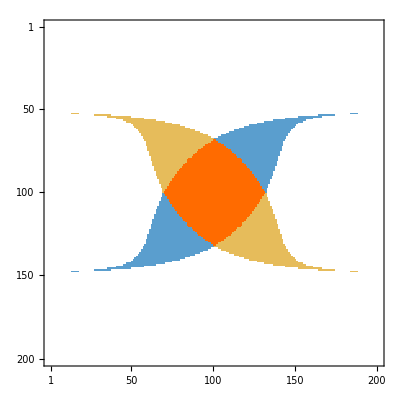

```mathematica
Transpose@Partition[edgeCountResults[[All,3]],Length[varYVals]]//MatrixPlot
```

## (Not truly correct on analytical sheet tracking but works)- M-Riemann surface winding

## Module and M-variable definitions

### M_branch and M_deg definitions

GBZ HELPER FUNCTIONS: dzFunc = (epsilonA-epsilonB)/2 + i*Gamma is the complex detuning. MbrFunc[p,s1,s2] returns branching point beta_br with denominator 2*t1 (not 4*t1). MdegFunc[p,s1,s2] returns degeneracy point beta_deg using discriminant Sqrt[t2^2 - 4*m^2].

```mathematica
ClearAll[MjFunc,MdegFunc,MbrFunc,dzFunc]

(*d_z=(epsA-epsB)/2*)
ClearAll[dzFunc];
dzFunc[assoc_Association]:=(assoc["εA"]-assoc["εB"])/2+I assoc["Γ"];

(*---M-plane branch points,Eq.(Mbranch_selected_explicit)---*)
MbrFunc[assoc_,s1_,s2_]:=Module[{t,tp,dz,a},
t=assoc["t1"];
tp=assoc["t2"];
dz=dzFunc[assoc];
a=2 (dz+s1 I tp);
(-a+s2 Sqrt[a^2+4 t^2])/(2 t)]

(*---Bulk eigenvector degeneracy points,Eq.(Mdeg_selected_explicit)---*)
MdegFunc[assoc_Association,sig1_,sig2_]:=Module[{tp,m},
tp=assoc["t2"];
m=assoc["m"];
(sig1 tp+sig2 Sqrt[tp^2-4 m^2])/(2 m)];
```

```mathematica
ClearAll[getMdegPoints, getMbranchPoints];
getMbranchPoints[p_Association,wp_Integer:60]:=N[Flatten[Table[MbrFunc[p,s1,s2],{s1,{1,-1}},{s2,{1,-1}}]],wp];
getMdegPoints[p_Association,wp_Integer:60]:=N[{MdegFunc[p,1,1],MdegFunc[p,1,-1]},wp];
```

```mathematica
MdegFunc[symMap,s1,s2]
MbrFunc[symMap,s1,s2]
```

(s1 t2s+s2 √(-4 ms^2+t2s^2))/(2 ms)

(-2 ((eAs-eBs)/2+ⅈ Gs+ⅈ s1 t2s)+s2 √(4 t1s^2+4 ((eAs-eBs)/2+ⅈ Gs+ⅈ s1 t2s)^2))/(2 t1s)

```mathematica
getMdegPoints[defaultParams,60]
getMbranchPoints[defaultParams,60]
```

{3.73205080756887729352744634150587236694280525381038062805581,0.267949192431122706472553658494127633057194746189619371944193}

{-2.0667468864204397263509203391633850832078966127171459311048+5.16647866575756103074934177331902971837008682386607034233491 ⅈ,0.066746886420439726350920339163385083207896612717145931104751+0.166854667575772302583991560014303614963246509467262990998424 ⅈ,-2.41421356237309504880168872420969807856967187537694807317668,0.41421356237309504880168872420969807856967187537694807317668}

### Module utilities for tracking the curves and points through the Riemann sheets correctly

#### Utilities for correct M-loop tracking

GBZ M-TRACKS: analyticMTracks[zlist, p] traces the two M(z) Riemann sheets around the BZ using FoldList analytic continuation. Returns Associations Root1 and Root2 with the two beta(theta) loops.

```mathematica
(* ==========Optimised analyticMTracks (packed arrays)==========*)
ClearAll[analyticMTracks];
analyticMTracks[zlist_List,p_Association]:=Module[{t,tp,dz,discVals,sCont,denom,root1,root2,s0,z},
{t,tp}={p["t1"],p["t2"]};
dz=dzFunc[p];
z=Developer`ToPackedArray[N[zlist]];(*ensure packed array*)
discVals=dz^2+(t+tp/z)*(t+tp z);(*vectorised,packed*)
s0=Sqrt[First[discVals]];
sCont=FoldList[Function[{prev,d},
With[{cand=Sqrt[d]},If[Abs[cand-prev]<=Abs[-cand-prev],cand,-cand]]],s0,Rest[discVals]];
denom=(t+tp #)&/@z;
root1=(-dz+sCont)/denom;
root2=(-dz-sCont)/denom;
<|"Root1"->root1,"Root2"->root2|>  (*no need to return SqrtCont*)];
```

#### Utilities for correct sheet association

SHEET ASSOCIATION: sheetAssociationAnalytic bundles each M-loop with beta_deg and beta_br. Critical: Root1 uses MbrFunc[p,1,1], Root2 uses MbrFunc[p,-1,-1]. wp=60 digit working precision.

```mathematica
(* ==========Sheet‑association (analytic,no search)==========*)
ClearAll[sheetAssociationAnalytic];
sheetAssociationAnalytic[tracked_,p_,wp_:60]:=Module[{degPlus,degMinus,brPlus,brMinus},(*Degeneracy points*)
degPlus=N[MdegFunc[p,1,1],wp];
degMinus=N[MdegFunc[p,1,-1],wp];
(*Branch points:fixed by sheet label–no winding test*)
brPlus=N[MbrFunc[p,1,1],wp];(*Root1,eta=+1*)
brMinus=N[MbrFunc[p,-1,-1],wp];(*Root2,eta=-1*)
<|"Root1"-><|"Loop"->tracked["Root1"],"Degeneracy"->degPlus,"Branch"->brPlus|>,"Root2"-><|"Loop"->tracked["Root2"],"Degeneracy"->degMinus,"Branch"->brMinus|>|>];
```

#### Utilities for correct winding

WINDING NUMBER COMPUTATION: WindingNumberCrossing[loop,pt] counts winding around pt via ray-crossing. WjFuncFast gives Wj = Mod[1 + W(loop,deg) - W(loop,br), 2]. allWindingNumbersFast returns W1, W2, and Total = W1+W2 for both Riemann sheets.

```mathematica
(* ==========Winding utilities==========*)
ClearAll[unwrapPhase,WindingNumberCrossing];

unwrapPhase[phases_List]:=Module[{d},
d=Differences[phases];
d=d-2 Pi Round[d/(2 Pi)];
Accumulate[Prepend[d,First[phases]]]];

(*Ray‑crossing winding number–O(n)---> or "Sunday's winding-number-of-a-polygon test"*)
WindingNumberCrossing[loop_List,pt_?NumericQ]:=Module[{L,n,wn=0,x0,y0,x1,y1,px,py,isLeft},
L=N[loop];
If[First[L]=!=Last[L],
L=Append[L,First[L]]];
{px,py}=ReIm[pt];
n=Length[L]-1;
Do[{x0,y0}=ReIm[L[[i]]];
{x1,y1}=ReIm[L[[i+1]]];
isLeft=(x1-x0)*(py-y0)-(px-x0)*(y1-y0);
Which[y0<=py<y1,If[isLeft>0,wn++],y1<=py<y0,If[isLeft<0,wn--]],{i,n}];
wn];
```

#### Winding definition

```mathematica
(* ==========Single‑sheet winding (Eq.10)==========*)
ClearAll[WjFuncFast];
WjFuncFast[Mloop_List,Mdeg_?NumericQ,Mbr_?NumericQ]:=Module[{Wdeg,Wbr},
Wdeg=WindingNumberCrossing[Mloop,Mdeg];
Wbr=WindingNumberCrossing[Mloop,Mbr];
Mod[1+Wdeg-Wbr,2]];

(* ==========Combined winding for one parameter point==========*)
ClearAll[allWindingNumbersFast];
allWindingNumbersFast[zlist_List,p_Association,wp_:60]:=Module[{tracked,sa,W1,W2},
tracked=analyticMTracks[zlist,p];(*optimized analyticMTracks below*)
sa=sheetAssociationAnalytic[tracked,p,wp];
W1=WjFuncFast[sa["Root1","Loop"],sa["Root1","Degeneracy"],sa["Root1","Branch"]];
W2=WjFuncFast[sa["Root2","Loop"],sa["Root2","Degeneracy"],sa["Root2","Branch"]];
<|"W1"->W1,"W2"->W2,"Total"->W1+W2|>];
```

#### Winding computation module in a 2D sweep

```mathematica
(* ==========Grid computation (no AppendTo,fully parallel)==========*)
ClearAll[computeWindingGrid];
computeWindingGrid[xVals_List,yVals_List,zlist_List]:=Module[{dims={Length[xVals],Length[yVals]},results},LaunchKernels[];
DistributeDefinitions[dzFunc,MdegFunc,MbrFunc,analyticMTracks,WindingNumberCrossing,sheetAssociationAnalytic,WjFuncFast,allWindingNumbersFast,resolveParams,zlist];
results=ParallelTable[Module[{p,res,x=xVals[[ix]],y=yVals[[iy]]},Quiet@Check[p=resolveParams[x,y];
res=allWindingNumbersFast[zlist,p,60];
{x,y,res["Total"],res},{x,y,Missing["NonNumeric"],$Failed}]],{ix,dims[[1]]},{iy,dims[[2]]}];
<|"Wmat"->results[[All,All,3]],"Winfo"->results[[All,All,4]]|>];
```

## Compute winding

### Winding computation in a 2D sweep

```mathematica
grid=computeWindingGrid[varXVals,varYVals,zlist];
Wmat=grid["Wmat"];
Winfo=grid["Winfo"];
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

## Eigenstates

## Eigenstates profiles with edge count color modules

```mathematica
(*ISSUE WHEN USING NON-NUMERIC VALUES LIKE 
-2->RGBColor[0.017,0.180,0.500],
-1->RGBColor[0.400,0.600,0.850]...
IS THAT ArrayPlot applies special implicit handling to arrays with a 
small number of distinct exact-integer values---> WE NEED NUMERICAL VALUES with INFINITE PRECISSION!*)
Clear[edgeColorFunction]
color3=RGBColor[0.700,0.550,0.850];(*purple,both edges simultaneously*);
color2=RGBColor[0.545,0.000,0.000](*dark red*);
color1=RGBColor[0.860,0.080,0.080](*red*);
color0=White(*no edge state*);
colorm1=RGBColor[0.300,0.500,0.900](*blue*);
colorm2=RGBColor[0.017,0.180,0.500](*dark blue*);


Clear[edgeColorFunctionStates]
edgeColorFunctionStates[n_]:=n/. {
x_/;x==3.->Blend[{color3,Purple},0.56],
x_/;x==2.->color2,
x_/;x==1.->color1,
x_/;x==0.->color0,
x_/;x==-1.->colorm1,
x_/;x==-2.->colorm2,

_->Gray};
```

```mathematica
(* ================================================================§4B—EIGENSTATE PROFILE SNAPSHOTS (DUAL-EDGE AWARE,DISCRETE PALETTE) Tick labels now use the notebook-global tickStyle directive (FontFamily->CommonFontFamStyle,FontSize->TF,FontColor->Black),identical to xTicks/yTicks/FrameTicksStyle in commonOpts,so these profile panels are visually indistinguishable in typography from the dIPR/CondNum/EdgeNum phase-diagram plots.
================================================================*)
ClearAll[makeStateAssoc,EigenstateProfileData,PlotEigenstateProfile,dIPRSnapshotPlots];

(*---Package one eigenvector's diagnostics into an Association---*)
makeStateAssoc[k_Integer,vals_,vecs_,dvals_]:=<|"psi"->vecs[[k]],"energy"->vals[[k]],"dIPR"->dvals[[k]],"IPR"->IPR[vecs[[k]]]|>;

(*---Build full diagnostic data for one (x,y) point---*)
EigenstateProfileData[x_?NumericQ,y_?NumericQ]:=Module[{p,H,vals,vecs,iprs,bulkMedian,thresh,edgeIdx,dvals,sides,leftIdx,rightIdx,states,kL,kR,k,nL,nR,panelClass},
p=resolveParams[x,y];
H=N@Normal@HOBCgen[p];
{vals,vecs}=Eigensystem[H];
iprs=IPR/@vecs;
dvals=dIPRBaiStyle[#,δIPRshift]&/@vecs;
bulkMedian=Median[iprs];
thresh=iprMedianMultiplyingFactor*bulkMedian;
edgeIdx=Flatten@Position[iprs,v_/;v>thresh];
sides=DSignBaiStyle[#,δIPRshift]&/@vecs[[edgeIdx]];
leftIdx=Pick[edgeIdx,sides,-1];
rightIdx=Pick[edgeIdx,sides,1];
nL=Length[leftIdx];
nR=Length[rightIdx];
panelClass=edgeCountLabel[{nL,nR}];
states={};
If[nL>0,kL=leftIdx[[First@Ordering[iprs[[leftIdx]],-1]]];
AppendTo[states,Append[makeStateAssoc[kL,vals,vecs,dvals],"side"->"L"]]];
If[nR>0,kR=rightIdx[[First@Ordering[iprs[[rightIdx]],-1]]];
AppendTo[states,Append[makeStateAssoc[kR,vals,vecs,dvals],"side"->"R"]]];
If[states==={},k=First@Ordering[Abs[dvals],-1];
states={Append[makeStateAssoc[k,vals,vecs,dvals],"side"->"bulk"]}];
<|"x"->x,"y"->y,"p"->p,"states"->states,"nL"->nL,"nR"->nR,"panelClass"->panelClass|>];
```

# Fig 4. properties plotting

## Final Panels parameters

```mathematica
(* ================================================================*)(*COMPACT,JOINED 7-PANEL FIGURE:GEOMETRY*)(* ================================================================*)ClearAll[removeGeometryRules,joinedMapOpts,joinedProfileOpts,makeMapPanel,makeSwatchCompact,PlotEigenstateProfileJoined,mapInnerW,mapInnerH,mapLeftPad,mapRightPad,mapBottomPad,profileInnerW,profileInnerH,profileLeftPad,profileRightPad,profileBottomPad];
```

```mathematica
(*---------------------------------------------------------------*)
(*MAP PANELS:common physical plotting rectangle*)
(*---------------------------------------------------------------*)

(*Every map has a true 280 x 280 coordinate frame.*)
mapInnerW=280;
mapInnerH=280;

(*External space for labels/ticks.*)
mapLeftPad=72;
mapRightPad=18;
mapBottomPad=83;

(*---------------------------------------------------------------*)
(*PROFILE PANELS:exact total-height match with map block*)
(*---------------------------------------------------------------*)

(*Map block total height:2 mapInnerH+mapBottomPad=2*280+83=643 Profile-column total height:3 profileInnerH+profileBottomPad=3*187+82=643*)
profileInnerW=300;
profileInnerH=187;

profileLeftPad=76;
profileRightPad=24;
profileBottomPad=82;

(*Extra exterior room for the topmost labels of (a),(b),and (e).*)
mapTopPad=16;
profileTopPad=16;

(* ================================================================*)
(*GEOMETRY*)
(* ================================================================*)

mapInnerW=280;
mapInnerH=280;

mapLeftPad=72;
mapRightPad=18;
mapBottomPad=80;
mapTopPad=18;

profileInnerW=300;
profileInnerH=187;

profileLeftPad=78;
profileRightPad=24;
profileBottomPad=82;
profileTopPad=18;
```

## Plots arranged through a) K[U] b) dIPR c)EdgeC d) W

## A) Modules-Compact Final Panels modules

```mathematica
(* ================================================================*)
(*COMPACT,JOINED 7-PANEL FIGURE*)
(*2x2 map block+3 eigenstate-profile panels*)(*Standard external tick labels;only colliding labels are offset.*)
(* ================================================================*)
ClearAll[removeGeometryRules,joinedMapOpts,joinedProfileOpts,makeMapPanel,makeSwatchCompact,PlotEigenstateProfileJoined,tickPosition,blankTickLabel,blankNearestTickLabel,blankTickLabels,getFrameTicksFromCommonOpts,externalInset,moveTickLabel];

(* ================================================================*)
(*LAYOUT HELPERS*)
(* ================================================================*)

removeGeometryRules[opts___]:=DeleteCases[Flatten[{opts}],HoldPattern[(ImageSize|ImagePadding|AspectRatio|PlotRangePadding)->_]];

(*showBottom=True:panels (c),(d) showLeft=True:panels (a),(c) showTop=True:panels (a),(b)*)

ClearAll[joinedMapOpts];

joinedMapOpts[showBottom_,showLeft_,showTop_]:=Join[removeGeometryRules[commonOptsFor[showBottom,showLeft]],{ImagePadding->{{If[showLeft,mapLeftPad,0],If[showLeft,0,mapRightPad]},{If[showBottom,mapBottomPad,0],If[showTop,mapTopPad,0]}},ImageSize->{mapInnerW+If[showLeft,mapLeftPad,0]+If[showLeft,0,mapRightPad],mapInnerH+If[showBottom,mapBottomPad,0]+If[showTop,mapTopPad,0]},AspectRatio->mapInnerH/mapInnerW,PlotRangePadding->None}];

(*showBottom=True:panel (g) showTop=True:panel (e)*)

ClearAll[joinedProfileOpts];

joinedProfileOpts[showBottom_,showTop_]:={ImagePadding->{{profileLeftPad,profileRightPad},{If[showBottom,profileBottomPad,0],If[showTop,profileTopPad,0]}},ImageSize->{profileInnerW+profileLeftPad+profileRightPad,profileInnerH+If[showBottom,profileBottomPad,0]+If[showTop,profileTopPad,0]},AspectRatio->profileInnerH/profileInnerW,PlotRangePadding->None};

(* ================================================================*)
(*TICK HELPERS*)
(* ================================================================*)

tickPosition[tick_List]:=First[tick];

blankTickLabel[tick_List]:=ReplacePart[tick,2->""];

blankTickLabels[ticks_List]:=blankTickLabel/@ticks;

blankNearestTickLabel[ticks_List,x_?NumericQ]:=Module[{idx},If[Length[ticks]==0,Return[ticks]];
idx=First@Ordering[Abs[N[tickPosition[#]]-N[x]]&/@ticks,1];
ReplacePart[ticks,idx->blankTickLabel[ticks[[idx]]]]];

getFrameTicksFromCommonOpts[]:=Module[{rules,ticks},rules=Flatten[{commonOptsFor[True,True]}];
ticks=FirstCase[rules,HoldPattern[FrameTicks->ft_]:>ft,Missing["FrameTicksNotFound"]];
If[MissingQ[ticks],Print["Error: commonOptsFor[True, True] must include a FrameTicks rule."];
Abort[];];
ticks];

externalInset[label_,pos_,offset_,alignment_]:=Inset[label,Offset[offset,Scaled[pos]],alignment];

(* ================================================================*)
(*MAP TICKS*)
(* ================================================================*)

mapFrameTicksFull=getFrameTicksFromCommonOpts[];

(*FrameTicks order:{{left,right},{bottom,top}}*)
mapYTicksFull=mapFrameTicksFull[[1,1]];
mapXTicksFull=mapFrameTicksFull[[2,1]];

mapYMin=Min[tickPosition/@mapYTicksFull];
mapYMax=Max[tickPosition/@mapYTicksFull];

mapXMin=Min[tickPosition/@mapXTicksFull];
mapXMax=Max[tickPosition/@mapXTicksFull];

(*(a):blank lower-1.0;it is redrawn outside the frame.*)
mapYTicksForA=blankNearestTickLabel[mapYTicksFull,mapYMin];

(*Tick marks remain;labels are blank.*)
mapXTicksNoLabels=blankTickLabels[mapXTicksFull];

mapYTicksNoLabels=blankTickLabels[mapYTicksFull];

(* ================================================================*)
(*PANEL (c):SHIFT ONLY THE SHARED-BOUNDARY LABEL BOXES*)
(* ================================================================*)

ClearAll[moveTickLabel];

moveTickLabel[tick_List,direction_String,amount_:22]:=Module[{lab,shiftedLabel},lab=tick[[2]];
shiftedLabel=Switch[direction,(*Used only for m/gamma=+1.0 in panel (c).*)"Down",Pane[lab,ImageSize->{Automatic,amount+16},Alignment->{Center,Bottom}],(*t/gamma=+3 in panel (c):shift left and lift baseline.*)"Left",DisplayForm@AdjustmentBox[ToBoxes[lab],BoxMargins->{{0,amount},{0,0}},BoxBaselineShift->-0.35],(*t/gamma=-3 in panel (d):shift right and lift baseline.*)"Right",DisplayForm@AdjustmentBox[ToBoxes[lab],BoxMargins->{{amount,0},{0,0}},BoxBaselineShift->-0.35],_,lab];
ReplacePart[tick,2->shiftedLabel]];

cTopYTickIndex=First@Ordering[Abs[N[tickPosition[#]]-N[mapYMax]]&/@mapYTicksFull,1];

cRightXTickIndex=First@Ordering[Abs[N[tickPosition[#]]-N[mapXMax]]&/@mapXTicksFull,1];

(*+1.0:downward shift;adjust 30 upward if still partially clipped.*)
mapYTicksForC=ReplacePart[mapYTicksFull,cTopYTickIndex->moveTickLabel[mapYTicksFull[[cTopYTickIndex]],"Down",38]];

(*+3:left shift,normal vertical baseline.*)
mapXTicksForC=ReplacePart[mapXTicksFull,cRightXTickIndex->moveTickLabel[mapXTicksFull[[cRightXTickIndex]],"Left",1.2]];

(*(d):-3 is shifted right,with its regular baseline preserved.*)
dLeftXTickIndex=First@Ordering[Abs[N[tickPosition[#]]-N[mapXMin]]&/@mapXTicksFull,1];

mapXTicksForD=ReplacePart[mapXTicksFull,dLeftXTickIndex->moveTickLabel[mapXTicksFull[[dLeftXTickIndex]],"Right",1.2]];

(* ================================================================*)
(*COMMON MAP-PANEL FUNCTION*)
(* ================================================================*)

ClearAll[makeMapPanel];

makeMapPanel[plot_,tag_,markers_,extraEpilog_:{}]:=Show[plot,PlotRangeClipping->False,Epilog->Join[{Inset[tag,Scaled[{0.055,0.95}],{Left,Top}],markers},Flatten[{extraEpilog}]]];

(* ================================================================*)
(*(a) CONDITION-NUMBER MAP*)
(* ================================================================*)

minCond=Min[EPresultsCondNum[[All,3]]];
maxCond=Max[EPresultsCondNum[[All,3]]];

condRange=If[Chop[maxCond-minCond]==0,{minCond-1/2,maxCond+1/2},{Floor[minCond],Ceiling[maxCond]}];

CondNumMat=Partition[EPresultsCondNum[[All,3]],Length[varYVals]];

conditionNumberCore=makeMapPanel[ArrayPlot[Reverse@Transpose@CondNumMat,PlotRange->condRange,ColorFunction->"AvocadoColors",ColorFunctionScaling->True,FrameTicks->{{mapYTicksForA,None},{mapXTicksNoLabels,None}},FrameTicksStyle->White,Evaluate@joinedMapOpts[False,True,True]],Style["(a)",White,FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],snapMarkersWhite,{externalInset[Style[NumberForm[mapYMin,{3,1}],White,FontFamily->CommonFontFamStyle,FontSize->TF],{0,0},{-10,12},{Right,Bottom}]}];

(* ================================================================*)
(*(b) dIPR MAP*)
(* ================================================================*)

maxAbs=Max[Abs[dIPRresults[[All,3]]]];
dIPRRange={-maxAbs,maxAbs};

bioEdgeLegendLabel=Style[Row[{"dIPR ",Style["L",Blue],"|",Style["R",Red]}],FontFamily->CommonFontFamStyle,FontSize->LF,FontColor->Black];

dIPRColor[p_]:=Blend[{RGBColor[0.017,0.314,0.680],White,RGBColor[0.780,0.050,0.090]},p];

rescaleSigned[x_,xmax_]:=If[xmax<=10^-14,0.5,0.5 (1+x/xmax)];

ClearAll[dIPRColorFunction];

dIPRColorFunction[x_]:=dIPRColor[rescaleSigned[x,maxAbs]];

dIPRCore=makeMapPanel[ArrayPlot[Reverse@Transpose@dIPRMat,PlotRange->dIPRRange,ColorFunction->dIPRColorFunction,ColorFunctionScaling->False,FrameTicks->{{mapYTicksNoLabels,None},{mapXTicksNoLabels,None}},FrameTicksStyle->Black,Evaluate@joinedMapOpts[False,False,True]],Style["(b)",FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],snapMarkers];

(* ================================================================*)
(*(c) EDGE-COUNT MAP*)
(* ================================================================*)

color3=RGBColor[0.700,0.550,0.850];
color2=RGBColor[0.545,0.000,0.000];
color1=RGBColor[0.860,0.080,0.080];
color0=White;
colorm1=RGBColor[0.300,0.500,0.900];
colorm2=RGBColor[0.017,0.180,0.500];

ClearAll[edgeColorFunction];

edgeColorFunction[n_]:=n/. {x_/;x==3.->color3,x_/;x==2.->color2,x_/;x==1.->color1,x_/;x==0.->color0,x_/;x==-1.->colorm1,x_/;x==-2.->colorm2,_->GrayLevel[0.7]};

edgeCountMat=Partition[edgeCountResults[[All,3]],Length[varYVals]];

edgeCountCore=makeMapPanel[MatrixPlot[Reverse@Transpose@edgeCountMat,ColorFunction->edgeColorFunction,ColorFunctionScaling->False,PlotRangeClipping->False,FrameTicks->{{mapYTicksForC,None},{mapXTicksForC,None}},FrameTicksStyle->Black,Evaluate@joinedMapOpts[True,True,False]],Style["(c)",FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],snapMarkers];

(* ================================================================*)
(*(d) WINDING-NUMBER MAP*)
(* ================================================================*)

ClearAll[wCF];

wCF[w_]:=Switch[w,0,White,1,RGBColor[0.00,0.45,0.55],2,RGBColor[0.90,0.45,0.10],_,GrayLevel[0.8]];

windingCore=makeMapPanel[ArrayPlot[Reverse@Transpose@Wmat,ColorFunction->wCF,ColorFunctionScaling->False,FrameTicks->{{mapYTicksNoLabels,None},{mapXTicksForD,None}},FrameTicksStyle->Black,Evaluate@joinedMapOpts[True,False,False]],Style["(d)",FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],snapMarkers];

(* ================================================================*)(*LEGENDS:CENTERED OVER/UNDER THEIR MAP PLOTTING RECTANGLES*)(* ================================================================*)
ClearAll[makeSwatchCompact];

makeSwatchCompact[color_,edgeQ_:True]:=Graphics[{If[edgeQ,EdgeForm[{Black,AbsoluteThickness[0.9]}],EdgeForm[]],color,Rectangle[]},PlotRange->{{0,1},{0,1}},ImageSize->{15,15},AspectRatio->1];

legendStyle=Directive[FontFamily->CommonFontFamStyle,FontSize->TF-2,FontColor->Black];

dIPRRange={-maxAbs,maxAbs};
(*----------------------------*)
(*Top legends:(a) and (b)*)
(*----------------------------*)

condLegendTop=BarLegend[{"AvocadoColors",condRange},LegendLayout->"Row",LegendMarkerSize->{205,15},LabelStyle->legendStyle,LegendLabel->Style["ln 𝒦(U)",FontFamily->CommonFontFamStyle,FontSize->TF-1]];

(* ================================================================*)(*LEGENDS:COMPACT AND CENTERED OVER/UNDER MAP PANELS*)(* ================================================================*)(*----------------------------*)(*Top legends:panels (a),(b)*)(*----------------------------*)condLegendTop=BarLegend[{"AvocadoColors",condRange},LegendLayout->"Row",LegendMarkerSize->{205,15},LabelStyle->legendStyle,LegendLabel->Style["ln 𝒦(U)",FontFamily->CommonFontFamStyle,FontSize->TF-1]];

(*Three equally spaced labels:-maxAbs,0,+maxAbs.Thus 0 is exactly in the center and labels cannot overlap.*)

(*dIPRLegendTop=BarLegend[{dIPRColorFunction,dIPRRange},LegendLayout->"Row",LegendMarkerSize->{240,15},LabelStyle->Directive[FontFamily->CommonFontFamStyle,FontSize->TF-3,FontColor->Black],LegendLabel->bioEdgeLegendLabel];
*)
(*dIPRLegendTop=DisplayForm@ReplaceAll[ToBoxes@BarLegend[{dIPRColorFunction,dIPRRange},LegendLayout->"Row",LegendMarkerSize->{240,15},LabelStyle->Directive[FontFamily->CommonFontFamStyle,FontSize->TF-3,FontColor->Black],LegendLabel->bioEdgeLegendLabel],"0."->"0.0"];*)
dIPRLegendTop=BarLegend[{dIPRColorFunction,dIPRRange},LegendLayout->"Row",LegendMarkerSize->{240,15},LabelStyle->Directive[FontFamily->CommonFontFamStyle,FontSize->TF-3,FontColor->Black],LegendLabel->bioEdgeLegendLabel]



(*These Pane widths match the physical 280-point map rectangles.mapLeftPad aligns the first legend with panel (a)/(c).*)
topMapLegends=Grid[{{Spacer[{mapLeftPad,1}],Pane[condLegendTop,ImageSize->{mapInnerW,Automatic},Alignment->Center],Pane[dIPRLegendTop,ImageSize->{mapInnerW,Automatic},Alignment->Center],Spacer[{mapRightPad,1}]}},Alignment->{Center,Center},Spacings->{0,0}];
```

```mathematica
(*----------------------------*)
(*Bottom legend:panel (c)*)
(*----------------------------*)

edgeCountLegendHeader=Style[Row[{"(",Subscript["n","L"],", ",Subscript["n","R"],")"}],FontFamily->CommonFontFamStyle,FontSize->TF-3,FontColor->Black];

edgeCountLegendEntry[color_,values_]:=Row[{makeSwatchCompact[color],Spacer[4],Style[values,FontFamily->CommonFontFamStyle,FontSize->TF-3,FontColor->Black]}];

(*Two compact rows:header defines the ordering (nL,nR);
entries contain only the corresponding integer pair.*)
edgeCountLegendBottom=Column[{edgeCountLegendHeader,Grid[{{edgeCountLegendEntry[color3,"(1, 1)"],edgeCountLegendEntry[color1,"(0, 1)"]},{edgeCountLegendEntry[color0,"(0, 0)"],edgeCountLegendEntry[colorm1,"(1, 0)"]}},Alignment->Center,Spacings->{1.0,0.25}]},Alignment->Center,Spacings->0.10];

(*----------------------------*)
(*Bottom legend:panel (d)*)
(*----------------------------*)

windingLegendBottom=Grid[{{makeSwatchCompact[White],Style["W = 0",legendStyle],Spacer[6],makeSwatchCompact[RGBColor[0.00,0.45,0.55]],Style["W = 1",legendStyle],Spacer[6],makeSwatchCompact[RGBColor[0.90,0.45,0.10]],Style["W = 2",legendStyle]}},Alignment->Center,Spacings->{0.25,0}];

(*Map-aligned lower legends.*)
bottomMapLegends=Grid[{{Spacer[{mapLeftPad,1}],Pane[edgeCountLegendBottom,ImageSize->{mapInnerW,Automatic},Alignment->Center],Pane[windingLegendBottom,ImageSize->{mapInnerW,Automatic},Alignment->Center],Spacer[{mapRightPad,1}]}},Alignment->{Center,Top},Spacings->{0,0}]
```

| (n_L, n_R)
-Graphics-(1, 1) | -Graphics-(0, 1)
-Graphics-(0, 0) | -Graphics-(1, 0) | -Graphics- | W = 0 |  | -Graphics- | W = 1 |  | -Graphics- | W = 2 |

```mathematica
(* ================================================================*)
(*EIGENSTATE DATA*)
(* ================================================================*)

profileEntries=Table[<|"x"->snappedSnapList[[i,1]],"y"->snappedSnapList[[i,2]],"data"->EigenstateProfileData[snappedSnapList[[i,1]],snappedSnapList[[i,2]]]|>,{i,Length[snappedSnapList]}];

If[Length[profileEntries]!=3,Print["Warning: this layout requires exactly three selected snapshots."]];

profileDataList=profileEntries[[All,"data"]];

allProfileStates=Flatten[profileDataList[[All,"states"]],1];

profileLengths=Length/@allProfileStates[[All,"psi"]];

If[!SameQ@@profileLengths,Print["Error: selected profiles have different lattice lengths."];
Abort[];];

(* ================================================================*)
(*SHARED EIGENSTATE AXES*)
(* ================================================================*)

profileL=First[profileLengths];

(*Visual margin only:sites remain j=1,...,profileL.*)
profileXRange={1-1,profileL+1};

allProfileProbabilities=(Abs[#["psi"]]^2/Total[Abs[#["psi"]]^2])&/@allProfileStates;

profileYMax=Max[Flatten[allProfileProbabilities]];

profileYRange={0,1.05 profileYMax};

profileXTickPositions=DeleteDuplicates@Round@{1,0.25 profileL,0.50 profileL,0.75 profileL,profileL};

profileXTicks=({#,Style[ToString[#],FontFamily->CommonFontFamStyle,FontSize->TF]}&)/@profileXTickPositions;

profileYTickPositions=N[{0,profileYMax/2,profileYMax}];

profileYTicks=({#,Style[NumberForm[#,{3,1}],FontFamily->CommonFontFamStyle,FontSize->TF]}&)/@profileYTickPositions;

(*(e),(f):blank regular 0.0,redraw it upward outside the frame.*)
profileYTicksForE=blankNearestTickLabel[profileYTicks,Min[profileYTickPositions]];

profileYTicksForF=blankNearestTickLabel[profileYTicks,Min[profileYTickPositions]];

(*(g):completely standard ticks and labels.*)
profileYTicksForG=profileYTicks;

(* ================================================================*)
(*JOINED EIGENSTATE PROFILE FUNCTION*)
(* ================================================================*)

ClearAll[PlotEigenstateProfileJoined];

PlotEigenstateProfileJoined[data_Association,panelTag_String,yTicks_List,showBottom_:False]:=Module[{statesList,panelClass,panelColor,sites,curves,colors,subLabelRows,parameterLabel,isTopProfile,shiftZeroLabel},statesList=data["states"];
panelClass=data["panelClass"];
panelColor=edgeColorFunctionStates[N[panelClass]];
sites=Range[profileL];
isTopProfile=panelTag==="(i)";
shiftZeroLabel=MemberQ[{"(i)","(ii)"},panelTag];
curves=Table[With[{psi=statesList[[i,"psi"]]},Transpose[{sites,Abs[psi]^2/Total[Abs[psi]^2]}]],{i,Length[statesList]}];
colors=ConstantArray[panelColor,Length[curves]];
subLabelRows=Table[With[{state=statesList[[i]]},Row[{Subscript["dIPR",If[state["dIPR"]>=0,"→","←"]]," = ",NumberForm[state["dIPR"],{4,2}]}]],{i,Length[statesList]}];
parameterLabel=Style[Column[Flatten@{Row[{varXFullLabel," = ",NumberForm[data["x"],{3,2}],"   ",varYFullLabel," = ",NumberForm[data["y"],{3,2}]}],subLabelRows},Alignment->Right],FontFamily->CommonFontFamStyle,FontSize->TF-5,FontColor->Black];
ListPlot[curves,PlotRange->{profileXRange,profileYRange},PlotRangeClipping->False,Joined->False,(*A vertical stem from zero for every physical site j.*)Filling->Axis,FillingStyle->(Directive[Opacity[0.55,#],AbsoluteThickness[1.8]]&)/@colors,PlotStyle->(Directive[#,AbsoluteThickness[1.8],PointSize[0.007]]&)/@colors,PlotMarkers->{Graphics[{EdgeForm[None],Disk[]},ImageSize->5],5},Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[0.8]],FrameTicks->{{yTicks,None},{If[showBottom,profileXTicks,blankTickLabels[profileXTicks]],None}},FrameLabel->{{Style["|\!\(\*SubscriptBox[\(ψ\), \(j\)]\)\!\(\*SuperscriptBox[\(|\), \(2\)]\)",FontFamily->CommonFontFamStyle,FontSize->LF],None},{If[showBottom,Style["Site index j",FontFamily->CommonFontFamStyle,FontSize->LF],None],None}},FrameTicksStyle->Black,LabelStyle->paperStyle,GridLines->{None,profileYTickPositions},GridLinesStyle->Directive[LightGray,Dashed],Epilog->Join[{Inset[Style[panelTag,FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],Scaled[{0.07,0.93}],{Left,Top}],Inset[parameterLabel,Scaled[{0.93,0.93}],{Right,Top}]},If[shiftZeroLabel,{externalInset[Style[NumberForm[0.,{3,1}],FontFamily->CommonFontFamStyle,FontSize->TF,FontColor->Black],{0,0},(*Horizontal:standard external y-label position.Vertical:0.0 shifted downward toward the shared boundary.*){-4,-5},{Right,Bottom}]},{}]],Evaluate@joinedProfileOpts[showBottom,isTopProfile]]
];
```

## A) Plots-Compact Final Panels plots

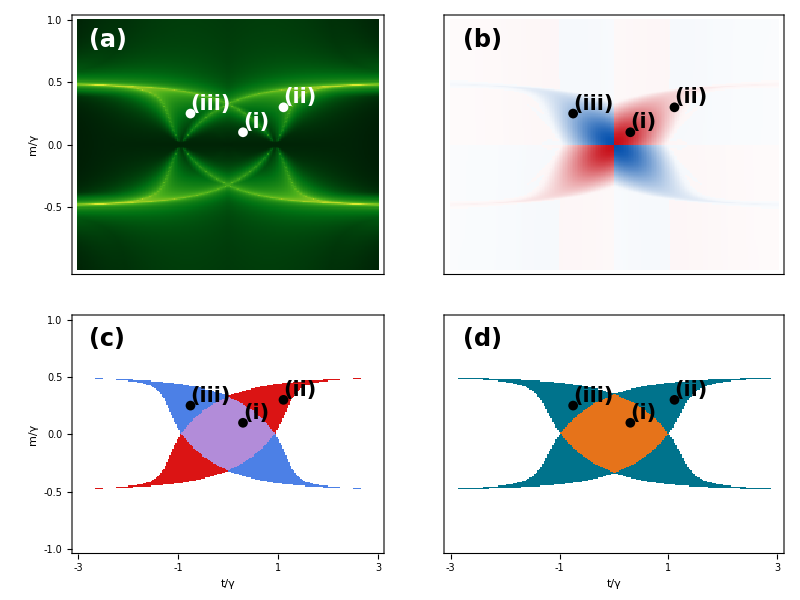
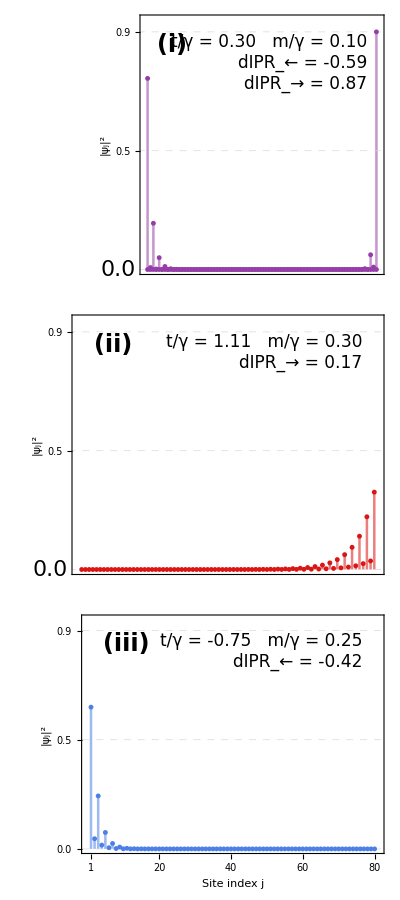
|  |  | 
-Graphics-
 | (n_L, n_R)
-Graphics-(1, 1) | -Graphics-(0, 1)
-Graphics-(0, 0) | -Graphics-(1, 0) | -Graphics- | W = 0 |  | -Graphics- | W = 1 |  | -Graphics- | W = 2 |  | 
-Graphics-

```mathematica
(* ================================================================*)
(*BUILD PROFILE COLUMN*)
(* ================================================================*)

profilePlots={PlotEigenstateProfileJoined[profileEntries[[1,"data"]],"(i)",profileYTicksForE,False],PlotEigenstateProfileJoined[profileEntries[[2,"data"]],"(ii)",profileYTicksForF,False],PlotEigenstateProfileJoined[profileEntries[[3,"data"]],"(iii)",profileYTicksForG,True]};

profileColumn=Grid[Partition[profilePlots,1],Alignment->{Left,Top},Spacings->{0,0}];

(* ================================================================*)
(*BUILD MAP BLOCK*)
(* ================================================================*)

spectraBlock=Grid[{{conditionNumberCore,dIPRCore},{edgeCountCore,windingCore}},Alignment->{Left,Top},Spacings->{0,0}];
(* ================================================================*)(*FINAL ARRANGEMENT*)(* ================================================================*)mapsWithLegends=Column[{topMapLegends,spectraBlock,bottomMapLegends},Alignment->Center,Spacings->0.40];

profileColumnAligned=Column[{Spacer[{1,95}],profileColumn,Spacer[{1,29}]},Alignment->Center,Spacings->0];

sevenPanelFigure=Grid[{{mapsWithLegends,profileColumnAligned}},Alignment->{Left,Top},Spacings->{0.42,0}];

sevenPanelFigure
```

```mathematica
$Version
```

14.2.1 for Mac OS X x86 (64-bit) (March 16, 2025)

## Plots reorganized as a) K[U] b)W c)dIPR d)EdgeC

## B) Modules-Rearranging Compact Final Panels

```mathematica
(* ================================================================*)(*COMPACT,JOINED 7-PANEL FIGURE*)(*Rearranged map block:*)(**)(*(a) condition number (b) winding number*)(*(c) dIPR (d) edge count*)(* ================================================================*)ClearAll[removeGeometryRules,joinedMapOpts,joinedProfileOpts,makeMapPanel,makeSwatchCompact,tickPosition,blankTickLabel,blankNearestTickLabel,blankTickLabels,getFrameTicksFromCommonOpts,externalInset,moveTickLabel];

(* ================================================================*)
(*LAYOUT HELPERS*)
(* ================================================================*)

removeGeometryRules[opts___]:=DeleteCases[Flatten[{opts}],HoldPattern[(ImageSize|ImagePadding|AspectRatio|PlotRangePadding)->_]];

(*showBottom=True:bottom-row panels (c),(d) showLeft=True:left-column panels (a),(c) showTop=True:top-row panels (a),(b)*)

ClearAll[joinedMapOpts];

joinedMapOpts[showBottom_,showLeft_,showTop_]:=Join[removeGeometryRules[commonOptsFor[showBottom,showLeft]],{ImagePadding->{{If[showLeft,mapLeftPad,0],If[showLeft,0,mapRightPad]},{If[showBottom,mapBottomPad,0],If[showTop,mapTopPad,0]}},ImageSize->{mapInnerW+If[showLeft,mapLeftPad,0]+If[showLeft,0,mapRightPad],mapInnerH+If[showBottom,mapBottomPad,0]+If[showTop,mapTopPad,0]},AspectRatio->mapInnerH/mapInnerW,PlotRangePadding->None}];

(*showBottom=True:panel (g) showTop=True:panel (e)*)

ClearAll[joinedProfileOpts];

joinedProfileOpts[showBottom_,showTop_]:={ImagePadding->{{profileLeftPad,profileRightPad},{If[showBottom,profileBottomPad,0],If[showTop,profileTopPad,0]}},ImageSize->{profileInnerW+profileLeftPad+profileRightPad,profileInnerH+If[showBottom,profileBottomPad,0]+If[showTop,profileTopPad,0]},AspectRatio->profileInnerH/profileInnerW,PlotRangePadding->None};

(* ================================================================*)
(*TICK HELPERS*)
(* ================================================================*)

tickPosition[tick_List]:=First[tick];

blankTickLabel[tick_List]:=ReplacePart[tick,2->""];

blankTickLabels[ticks_List]:=blankTickLabel/@ticks;

blankNearestTickLabel[ticks_List,x_?NumericQ]:=Module[{idx},If[Length[ticks]==0,Return[ticks]];
idx=First@Ordering[Abs[N[tickPosition[#]]-N[x]]&/@ticks,1];
ReplacePart[ticks,idx->blankTickLabel[ticks[[idx]]]]];

getFrameTicksFromCommonOpts[]:=Module[{rules,ticks},rules=Flatten[{commonOptsFor[True,True]}];
ticks=FirstCase[rules,HoldPattern[FrameTicks->ft_]:>ft,Missing["FrameTicksNotFound"]];
If[MissingQ[ticks],Print["Error: commonOptsFor[True, True] must include a FrameTicks rule."];
Abort[];];
ticks];

externalInset[label_,pos_,offset_,alignment_]:=Inset[label,Offset[offset,Scaled[pos]],alignment];

(* ================================================================*)
(*MAP TICKS*)
(* ================================================================*)

mapFrameTicksFull=getFrameTicksFromCommonOpts[];

(*FrameTicks convention:{{left,right},{bottom,top}}*)

mapYTicksFull=mapFrameTicksFull[[1,1]];

mapXTicksFull=mapFrameTicksFull[[2,1]];

mapYMin=Min[tickPosition/@mapYTicksFull];

mapYMax=Max[tickPosition/@mapYTicksFull];

mapXMin=Min[tickPosition/@mapXTicksFull];

mapXMax=Max[tickPosition/@mapXTicksFull];

(*(a):suppress the lower left y tick label and redraw externally.*)

(*mapYTicksForA=blankNearestTickLabel[mapYTicksFull,mapYMin];*)
aBottomYTickIndex=First@Ordering[Abs[N[tickPosition[#]]-N[mapYMin]]&/@mapYTicksFull,1];

mapYTicksForA=ReplacePart[mapYTicksFull,aBottomYTickIndex->moveTickLabel[mapYTicksFull[[aBottomYTickIndex]],"Up",38]];

(*Top-row panels have tick marks but no numerical x labels.*)

mapXTicksNoLabels=blankTickLabels[mapXTicksFull];

(*Top-right panel has no numerical y labels.*)

mapYTicksNoLabels=blankTickLabels[mapYTicksFull];

(* ================================================================*)
(*POSITION-DEPENDENT BOTTOM-ROW TICK OFFSETS*)
(* ================================================================*)

ClearAll[moveTickLabel];

(*moveTickLabel[tick_List,direction_String,amount_:22]:=Module[{lab,shiftedLabel},lab=tick[[2]];
shiftedLabel=Switch[direction,"Down",Pane[lab,ImageSize->{Automatic,amount+16},Alignment->{Center,Bottom}],"Left",DisplayForm@AdjustmentBox[ToBoxes[lab],BoxMargins->{{0,amount},{0,0}},BoxBaselineShift->-0.35],"Right",DisplayForm@AdjustmentBox[ToBoxes[lab],BoxMargins->{{amount,0},{0,0}},BoxBaselineShift->-0.35],_,lab];
ReplacePart[tick,2->shiftedLabel]];
*)
moveTickLabel[tick_List,direction_String,amount_:22]:=Module[{lab,shiftedLabel},lab=tick[[2]];
shiftedLabel=Switch[direction,"Down",Pane[lab,ImageSize->{Automatic,amount+16},Alignment->{Center,Bottom}],"Up",Pane[lab,ImageSize->{Automatic,amount+16},Alignment->{Center,Top}],"Left",DisplayForm@AdjustmentBox[ToBoxes[lab],BoxMargins->{{0,amount},{0,0}},BoxBaselineShift->-0.35],"Right",DisplayForm@AdjustmentBox[ToBoxes[lab],BoxMargins->{{amount,0},{0,0}},BoxBaselineShift->-0.35],_,lab];
ReplacePart[tick,2->shiftedLabel]];

(*New panel (c):dIPR is now bottom-left.It therefore owns the y labels and the left-side x endpoint.*)

cTopYTickIndex=First@Ordering[Abs[N[tickPosition[#]]-N[mapYMax]]&/@mapYTicksFull,1];

cRightXTickIndex=First@Ordering[Abs[N[tickPosition[#]]-N[mapXMax]]&/@mapXTicksFull,1];

mapYTicksForC=ReplacePart[mapYTicksFull,cTopYTickIndex->moveTickLabel[mapYTicksFull[[cTopYTickIndex]],"Down",38]];

mapXTicksForC=ReplacePart[mapXTicksFull,cRightXTickIndex->moveTickLabel[mapXTicksFull[[cRightXTickIndex]],"Left",1.2]];

(*New panel (d):edge-count map is now bottom-right.Shift its left x endpoint rightwards to avoid overlap with panel (c).*)

dLeftXTickIndex=First@Ordering[Abs[N[tickPosition[#]]-N[mapXMin]]&/@mapXTicksFull,1];

mapXTicksForD=ReplacePart[mapXTicksFull,dLeftXTickIndex->moveTickLabel[mapXTicksFull[[dLeftXTickIndex]],"Right",1.2]];

(* ================================================================*)
(*COMMON MAP-PANEL FUNCTION*)
(* ================================================================*)

ClearAll[makeMapPanel];

makeMapPanel[plot_,tag_,markers_,extraEpilog_:{}]:=Show[plot,PlotRangeClipping->False,Epilog->Join[{Inset[tag,Scaled[{0.055,0.95}],{Left,Top}],markers},Flatten[{extraEpilog}]]];

(* ================================================================*)
(*PANEL (a):CONDITION-NUMBER MAP*)
(*Top-left:y labels,no x labels*)
(* ================================================================*)

minCond=Min[EPresultsCondNum[[All,3]]];

maxCond=Max[EPresultsCondNum[[All,3]]];

condRange=If[Chop[maxCond-minCond]==0,{minCond-1/2,maxCond+1/2},{Floor[minCond],Ceiling[maxCond]}];

CondNumMat=Partition[EPresultsCondNum[[All,3]],Length[varYVals]];

(*conditionNumberCore=makeMapPanel[ArrayPlot[Reverse@Transpose@CondNumMat,PlotRange->condRange,ColorFunction->"AvocadoColors",ColorFunctionScaling->True,FrameTicks->{{mapYTicksForA,None},{mapXTicksNoLabels,None}},FrameTicksStyle->White,Evaluate@joinedMapOpts[False,(*no bottom labels*)True,(*left y labels*)True     (*top row*)]],Style["(a)",White,FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],snapMarkersWhite,{externalInset[Style[NumberForm[mapYMin,{3,1}],White,FontFamily->CommonFontFamStyle,FontSize->TF],{0,0},{-10,12},{Right,Bottom}]}];
*)

conditionNumberCore=makeMapPanel[ArrayPlot[Reverse@Transpose@CondNumMat,PlotRange->condRange,ColorFunction->"AvocadoColors",ColorFunctionScaling->True,FrameTicks->{{mapYTicksForA,None},{mapXTicksNoLabels,None}},FrameTicksStyle->White,Evaluate@joinedMapOpts[False,True,True]],Style["(a)",White,FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],snapMarkersWhite];

(* ================================================================*)
(*COMMON dIPR COLOUR MAP*)
(* ================================================================*)

maxAbs=Max[Abs[dIPRresults[[All,3]]]];

dIPRRange={-maxAbs,maxAbs};

bioEdgeLegendLabel=Style[Row[{"dIPR ",Style["L",Blue],"|",Style["R",Red]}],FontFamily->CommonFontFamStyle,FontSize->LF,FontColor->Black];

dIPRColor[p_]:=Blend[{RGBColor[0.017,0.314,0.680],White,RGBColor[0.780,0.050,0.090]},p];

rescaleSigned[x_,xmax_]:=If[xmax<=10^-14,0.5,0.5 (1+x/xmax)];

ClearAll[dIPRColorFunction];

dIPRColorFunction[x_]:=dIPRColor[rescaleSigned[x,maxAbs]];

(* ================================================================*)
(*PANEL (b):WINDING-NUMBER MAP*)
(*Top-right:no external x/y numerical labels*)
(* ================================================================*)

ClearAll[wCF];

wCF[w_]:=Switch[w,0,White,1,RGBColor[0.00,0.45,0.55],2,RGBColor[0.90,0.45,0.10],_,GrayLevel[0.8]];

windingCore=makeMapPanel[ArrayPlot[Reverse@Transpose@Wmat,ColorFunction->wCF,ColorFunctionScaling->False,FrameTicks->{{mapYTicksNoLabels,None},{mapXTicksNoLabels,None}},FrameTicksStyle->Black,Evaluate@joinedMapOpts[False,(*no bottom labels*)False,(*no left y labels*)True     (*top row*)]],Style["(b)",FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],snapMarkers];

(* ================================================================*)
(*PANEL (c):dIPR MAP*)
(*Bottom-left:external y labels and x labels*)
(* ================================================================*)

dIPRCore=makeMapPanel[ArrayPlot[Reverse@Transpose@dIPRMat,PlotRange->dIPRRange,ColorFunction->dIPRColorFunction,ColorFunctionScaling->False,FrameTicks->{{mapYTicksForC,None},{mapXTicksForC,None}},FrameTicksStyle->Black,Evaluate@joinedMapOpts[True,(*bottom x labels*)True,(*left y labels*)False    (*lower row*)]],Style["(c)",FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],snapMarkers];

(* ================================================================*)
(*PANEL (d):EDGE-COUNT MAP*)
(*Bottom-right:x labels only*)
(* ================================================================*)

color3=RGBColor[0.700,0.550,0.850];

color2=RGBColor[0.545,0.000,0.000];

color1=RGBColor[0.860,0.080,0.080];

color0=White;

colorm1=RGBColor[0.300,0.500,0.900];

colorm2=RGBColor[0.017,0.180,0.500];

ClearAll[edgeColorFunction];

edgeColorFunction[n_]:=n/. {x_/;x==3.->color3,x_/;x==2.->color2,x_/;x==1.->color1,x_/;x==0.->color0,x_/;x==-1.->colorm1,x_/;x==-2.->colorm2,_->GrayLevel[0.7]};

edgeCountMat=Partition[edgeCountResults[[All,3]],Length[varYVals]];

edgeCountCore=makeMapPanel[MatrixPlot[Reverse@Transpose@edgeCountMat,ColorFunction->edgeColorFunction,ColorFunctionScaling->False,PlotRangeClipping->False,FrameTicks->{{mapYTicksNoLabels,None},{mapXTicksForD,None}},FrameTicksStyle->Black,Evaluate@joinedMapOpts[True,(*bottom x labels*)False,(*no y labels*)False    (*lower row*)]],Style["(d)",FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],snapMarkers];

(* ================================================================*)
(*LEGENDS*)
(*Top row:condition number above (a),winding legend above (b).*)
(*dIPR legend should now be placed below/near panel (c),not top.*)
(* ================================================================*)

ClearAll[makeSwatchCompact];

makeSwatchCompact[color_,edgeQ_:True]:=Graphics[{If[edgeQ,EdgeForm[{Black,AbsoluteThickness[0.9]}],EdgeForm[]],color,Rectangle[]},PlotRange->{{0,1},{0,1}},ImageSize->{15,15},AspectRatio->1];

legendStyle=Directive[FontFamily->CommonFontFamStyle,FontSize->TF-2,FontColor->Black];

condLegendTop=BarLegend[{"AvocadoColors",condRange},LegendLayout->"Row",LegendMarkerSize->{205,15},LabelStyle->legendStyle,LegendLabel->Style["ln 𝒦(U)",FontFamily->CommonFontFamStyle,FontSize->TF-1]];

(*Winding-number swatches;modify labels only if your Wmat actually contains values beyond 0,1,2.*)

windingLegendTop=Row[{makeSwatchCompact[wCF[0]],Style["0",legendStyle],Spacer[8],makeSwatchCompact[wCF[1]],Style["1",legendStyle],Spacer[8],makeSwatchCompact[wCF[2]],Style["2",legendStyle]}];

(*dIPR legend follows its new panel (c).*)

dIPRLegendBottom=BarLegend[{dIPRColorFunction,dIPRRange},LegendLayout->"Row",LegendMarkerSize->{240,15},LabelStyle->Directive[FontFamily->CommonFontFamStyle,FontSize->TF-3,FontColor->Black],LegendLabel->bioEdgeLegendLabel];

(*Top legends must follow the new top row:condition number and winding number,not condition number and dIPR.*)

topMapLegends=Grid[{{Spacer[{mapLeftPad,1}],Pane[condLegendTop,ImageSize->{mapInnerW,Automatic},Alignment->Center],Pane[windingLegendTop,ImageSize->{mapInnerW,Automatic},Alignment->Center],Spacer[{mapRightPad,1}]}},Alignment->{Center,Center},Spacings->{0,0}];

(* ================================================================*)
(*MAP BLOCK:USE THIS ORDER*)
(* ================================================================*)

spectraBlockChanged=Grid[{{conditionNumberCore,windingCore},{dIPRCore,edgeCountCore}},Alignment->{Left,Top},Spacings->{0,0}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ArrayPlot::mat: Argument Symbol at position 1 is not a list of lists.

Show::gtype: ArrayPlot is not a type of graphics.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ArrayPlot::mat: Argument Wmat at position 1 is not a list of lists.

Show::gtype: ArrayPlot is not a type of graphics.

ArrayPlot::mat: Argument dIPRMat at position 1 is not a list of lists.

Show::gtype: ArrayPlot is not a type of graphics.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

MatrixPlot::mat0: Argument Symbol at position 1 is not a matrix.

Show::gtype: MatrixPlot is not a type of graphics.

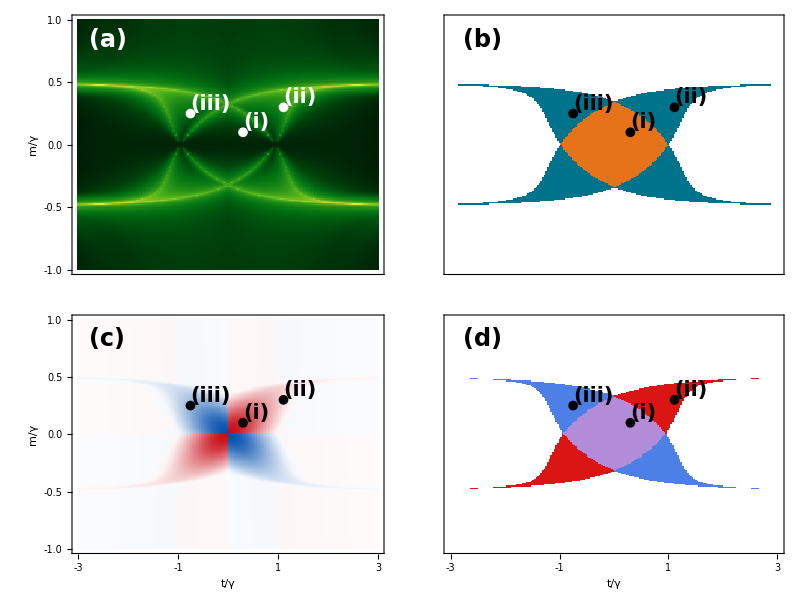

```mathematica
spectraBlockChanged
```

## B) Plots-Rearranged Compact Final Panels plots

```mathematica
(*These Pane widths match the physical 280-point map rectangles.mapLeftPad aligns the first legend with panel (a)/(c).*)
topMapLegendsChanged=Grid[{{Spacer[{mapLeftPad,1}],
Pane[condLegendTop,ImageSize->{mapInnerW,Automatic},Alignment->Center],Pane[windingLegendBottom,ImageSize->{mapInnerW,Automatic},Alignment->Center],
Spacer[{mapRightPad,1}]}},Alignment->{Center,Center},Spacings->{0,0}]
```

|  | -Graphics- | W = 0 |  | -Graphics- | W = 1 |  | -Graphics- | W = 2 |

```mathematica
bottomMapLegendsChanged=Grid[{{Spacer[{mapLeftPad,1}],
Pane[dIPRLegendTop,ImageSize->{mapInnerW,Automatic},Alignment->Center],Pane[edgeCountLegendBottom,ImageSize->{mapInnerW,Automatic},Alignment->Center],
Spacer[{mapRightPad,1}]}},Alignment->{Center,Top},Spacings->{0,0}]
```

|  | (n_L, n_R)
-Graphics-(1, 1) | -Graphics-(0, 1)
-Graphics-(0, 0) | -Graphics-(1, 0) |

```mathematica
(* ================================================================*)
(*BUILD PROFILE COLUMN*)
(* ================================================================*)

profilePlots={PlotEigenstateProfileJoined[profileEntries[[1,"data"]],"(i)",profileYTicksForE,False],PlotEigenstateProfileJoined[profileEntries[[2,"data"]],"(ii)",profileYTicksForF,False],PlotEigenstateProfileJoined[profileEntries[[3,"data"]],"(iii)",profileYTicksForG,True]};

profileColumn=Grid[Partition[profilePlots,1],Alignment->{Left,Top},Spacings->{0,0}];

(* ================================================================*)
(*FINAL ARRANGEMENT*)
(* ================================================================*)mapsWithLegends=Column[{topMapLegendsChanged,spectraBlockChanged,bottomMapLegendsChanged},Alignment->Center,Spacings->0.40];

profileColumnAligned=Column[{Spacer[{1,95}],profileColumn,Spacer[{1,29}]},Alignment->Center,Spacings->0];

sevenPanelFigure=Grid[{{mapsWithLegends,profileColumnAligned}},Alignment->{Left,Top},Spacings->{0.42,0}];

sevenPanelFigure
```

|  | -Graphics- | W = 0 |  | -Graphics- | W = 1 |  | -Graphics- | W = 2 | 
-Graphics-
 |  | (n_L, n_R)
-Graphics-(1, 1) | -Graphics-(0, 1)
-Graphics-(0, 0) | -Graphics-(1, 0) |  | 
-Graphics-

## Export---Final Panels plots

```mathematica
(* ================================================================*)(*EXPORT:CLEAN 7-PANEL FIGURE+SHORT PARAMETER README*)(* ================================================================*)ClearAll[exportNumber,exportModelName,exportFigureTag,exportScanTag];

(*Fixed three-decimal formatting,retaining ordinary decimal points.*)
exportNumber[x_]:=ToString[NumberForm[N[x],{Infinity,3},NumberPadding->{"","0"}],OutputForm];

(*Change this only if you want a different model prefix.*)
exportModelName=If[ValueQ[SystemName]&&StringQ[SystemName]&&SystemName=!="",SystemName,"NH_NNN_Rice_Mele"];

(*Change this to your desired figure identifier.*)
exportFigureTag="dIPRWindingFigure4";

(*Gives t1Scan,mScan,epsilonAScan,etc.*)
exportScanTag=varXSymbol<>"Scan";

If[TrueQ[ExportOption],If[!ValueQ[sevenPanelFigure],Print["Export aborted: evaluate sevenPanelFigure first."];
Abort[];];
(*--------------------------------------------------------------*)(*Output folder.*)(*--------------------------------------------------------------*)If[!ValueQ[ThisDir]||!StringQ[ThisDir]||ThisDir==="",ThisDir=NotebookDirectory[];];
dirPathFigure=FileNameJoin[{ThisDir,"Figures"}];
If[!DirectoryQ[dirPathFigure],CreateDirectory[dirPathFigure,CreateIntermediateDirectories->True];];
exportDateTag=DateString[{"Year","_","Month","_","Day","_","Hour24","h","Minute","m","Second","s"}];
(*--------------------------------------------------------------*)(*Short,readable,explicit parameter tag.*)(*Uses current parameter values,including sweep defaults.*)(*--------------------------------------------------------------*)parameterFileTag="_eA"<>exportNumber[εA]<>"_eB"<>exportNumber[εB]<>"_Gamma"<>exportNumber[Γ]<>"_m"<>exportNumber[m]<>"_t1"<>exportNumber[t1]<>"_t2"<>exportNumber[t2]<>"_nn"<>ToString[nn]<>"_dIPRshift"<>exportNumber[δIPRshift];
figBaseName=exportModelName<>parameterFileTag<>"_"<>exportFigureTag<>"_"<>exportScanTag<>"__"<>exportDateTag;
pdfPath=FileNameJoin[{dirPathFigure,figBaseName<>"_figure.pdf"}];
pngPath=FileNameJoin[{dirPathFigure,figBaseName<>"_figure.png"}];
readmePath=FileNameJoin[{dirPathFigure,figBaseName<>"_README.txt"}];
(*--------------------------------------------------------------*)(*Complete record:ranges,resolution,and selected snapshots.*)(*--------------------------------------------------------------*)exportReadme=StringRiffle[Join[{"Model: "<>exportModelName,"Figure: "<>exportFigureTag,"Date: "<>DateString[{"ISODate"," ","Time"}],"","Fixed/default model parameters:","  epsilonA = "<>exportNumber[εA],"  epsilonB = "<>exportNumber[εB],"  Gamma = "<>exportNumber[Γ],"  m = "<>exportNumber[m],"  t1 = "<>exportNumber[t1],"  t2 = "<>exportNumber[t2],"","System and numerical parameters:","  nn = "<>ToString[nn]<>" OBC unit cells","  Total sites = "<>ToString[profileL],"  dIPR shift = "<>exportNumber[δIPRshift],"  tol = "<>ToString[tol],"  nEdgeCandidates = "<>ToString[nEdgeCandidates],"  iprThresh = "<>ToString[iprThresh],"  nTheta = "<>ToString[nθ],"","Parameter scan:","  x variable = "<>varXSymbol,"  x range = {"<>exportNumber[xRange[[1]]]<>", "<>exportNumber[xRange[[2]]]<>"}","  y variable = "<>varYSymbol,"  y range = {"<>exportNumber[yRange[[1]]]<>", "<>exportNumber[yRange[[2]]]<>"}","  grid = "<>ToString[Length[varXVals]]<>" x "<>ToString[Length[varYVals]],"","Selected snapshots:"},("  "<>#[[3]]<>": ("<>varXSymbol<>", "<>varYSymbol<>") = ("<>exportNumber[#[[1]]]<>", "<>exportNumber[#[[2]]]<>")")&/@snapList],"\n"];
(*--------------------------------------------------------------*)(*Export figure and sidecar README.*)(*--------------------------------------------------------------*)Export[pdfPath,sevenPanelFigure,"PDF"];
Export[pngPath,sevenPanelFigure,"PNG",ImageResolution->600];
Export[readmePath,exportReadme,"Text"];
Print["PDF exported to: ",pdfPath];
Print["PNG exported to: ",pngPath];
Print["README exported to: ",readmePath];];
```

PDF exported to: /Users/carolinamstrasser/Library/CloudStorage/OneDrive-UPVEHU(2)/PhD/FourthYear_phD/Project_Nico/Figures/NH_NNN_Rice_Mele_eA0.000_eB1.500_Gamma1.000_m0.300_t11.100_t21.000_nn40_dIPRshift0.500_dIPRWindingFigure4_t1Scan__2026_07_29_16h50m29s_figure.pdf

PNG exported to: /Users/carolinamstrasser/Library/CloudStorage/OneDrive-UPVEHU(2)/PhD/FourthYear_phD/Project_Nico/Figures/NH_NNN_Rice_Mele_eA0.000_eB1.500_Gamma1.000_m0.300_t11.100_t21.000_nn40_dIPRshift0.500_dIPRWindingFigure4_t1Scan__2026_07_29_16h50m29s_figure.png

README exported to: /Users/carolinamstrasser/Library/CloudStorage/OneDrive-UPVEHU(2)/PhD/FourthYear_phD/Project_Nico/Figures/NH_NNN_Rice_Mele_eA0.000_eB1.500_Gamma1.000_m0.300_t11.100_t21.000_nn40_dIPRshift0.500_dIPRWindingFigure4_t1Scan__2026_07_29_16h50m29s_README.txt

# Fig 5. Phase transition computation and plotting

## Data ----Phase transition spectra with dIPR colouring

## Parameters for running the phase transition with dIPR

```mathematica
(* ================================================================
BRIDGE 0—items Notebook 1 never defines but Notebook 2 needs
================================================================*)
Clear[SitesPerCell,EdgeUcellsDef]
SitesPerCell=2;  (*A,B sublattice->2 dof per unit cell*)
EdgeUcellsDef=1; (*number of unit cells defining "the edge"*)

(* ================================================================
BRIDGE 1—1-parameter Hamiltonian wrappers built from HOBCgen/HPBCgen Holds every OTHER key in fixedParams fixed at its §1 global value,sweeps ONLY varXSymbol (default "t1").This replaces the old HOBCx[varXparam_]/HPBCx[varXparam_] built on TBHam/applyvaluesNoX.
================================================================*)
Clear[HOBCx,HPBCx]
HOBCx[xval_]:=Normal@HOBCgen[Association[defaultParams,varXSymbol->xval]];
HPBCx[xval_]:=Normal@HPBCgen[Association[defaultParams,varXSymbol->xval]];
(* ================================================================
BRIDGE 2—scan range for the EDGE-MODE figure (separate from the phase-diagram xmax/nX in §1c of Notebook 1,which serve a different purpose—the 2D m-vs-t1 sweep grid).
================================================================*)
Clear[xScanMax,nXEdge,pxEdge,xVals]
xScanMax=xmax;      (*reuse the §1c phase-diagram bound on varXSymbol*)
nXEdge=200;          (*coarser than nX=200—eigOBC+matching is expensive*)
pxEdge=1.;
uxEdge=Subdivide[-1,1,nXEdge];
xVals=N[xScanMax*Sign[#]*Abs[#]^pxEdge&/@uxEdge]
varXVals
(* ================================================================BRIDGE 3—energy-axis window for the Re[E]/Im[E] plots.Notebook 1's ymax/ymin are the m-AXIS bounds of the phase diagram—NOT an energy window.These are new,independent symbols.
================================================================*)
Clear[EYmin,EYmax]
EYmax=5;
EYmin=-EYmax;
```

{-3.,-2.97,-2.94,-2.91,-2.88,-2.85,-2.82,-2.79,-2.76,-2.73,-2.7,-2.67,-2.64,-2.61,-2.58,-2.55,-2.52,-2.49,-2.46,-2.43,-2.4,-2.37,-2.34,-2.31,-2.28,-2.25,-2.22,-2.19,-2.16,-2.13,-2.1,-2.07,-2.04,-2.01,-1.98,-1.95,-1.92,-1.89,-1.86,-1.83,-1.8,-1.77,-1.74,-1.71,-1.68,-1.65,-1.62,-1.59,-1.56,-1.53,-1.5,-1.47,-1.44,-1.41,-1.38,-1.35,-1.32,-1.29,-1.26,-1.23,-1.2,-1.17,-1.14,-1.11,-1.08,-1.05,-1.02,-0.99,-0.96,-0.93,-0.9,-0.87,-0.84,-0.81,-0.78,-0.75,-0.72,-0.69,-0.66,-0.63,-0.6,-0.57,-0.54,-0.51,-0.48,-0.45,-0.42,-0.39,-0.36,-0.33,-0.3,-0.27,-0.24,-0.21,-0.18,-0.15,-0.12,-0.09,-0.06,-0.03,0.,0.03,0.06,0.09,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.42,0.45,0.48,0.51,0.54,0.57,0.6,0.63,0.66,0.69,0.72,0.75,0.78,0.81,0.84,0.87,0.9,0.93,0.96,0.99,1.02,1.05,1.08,1.11,1.14,1.17,1.2,1.23,1.26,1.29,1.32,1.35,1.38,1.41,1.44,1.47,1.5,1.53,1.56,1.59,1.62,1.65,1.68,1.71,1.74,1.77,1.8,1.83,1.86,1.89,1.92,1.95,1.98,2.01,2.04,2.07,2.1,2.13,2.16,2.19,2.22,2.25,2.28,2.31,2.34,2.37,2.4,2.43,2.46,2.49,2.52,2.55,2.58,2.61,2.64,2.67,2.7,2.73,2.76,2.79,2.82,2.85,2.88,2.91,2.94,2.97,3.}

{-3.,-2.97,-2.94,-2.91,-2.88,-2.85,-2.82,-2.79,-2.76,-2.73,-2.7,-2.67,-2.64,-2.61,-2.58,-2.55,-2.52,-2.49,-2.46,-2.43,-2.4,-2.37,-2.34,-2.31,-2.28,-2.25,-2.22,-2.19,-2.16,-2.13,-2.1,-2.07,-2.04,-2.01,-1.98,-1.95,-1.92,-1.89,-1.86,-1.83,-1.8,-1.77,-1.74,-1.71,-1.68,-1.65,-1.62,-1.59,-1.56,-1.53,-1.5,-1.47,-1.44,-1.41,-1.38,-1.35,-1.32,-1.29,-1.26,-1.23,-1.2,-1.17,-1.14,-1.11,-1.08,-1.05,-1.02,-0.99,-0.96,-0.93,-0.9,-0.87,-0.84,-0.81,-0.78,-0.75,-0.72,-0.69,-0.66,-0.63,-0.6,-0.57,-0.54,-0.51,-0.48,-0.45,-0.42,-0.39,-0.36,-0.33,-0.3,-0.27,-0.24,-0.21,-0.18,-0.15,-0.12,-0.09,-0.06,-0.03,0.03,0.06,0.09,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.42,0.45,0.48,0.51,0.54,0.57,0.6,0.63,0.66,0.69,0.72,0.75,0.78,0.81,0.84,0.87,0.9,0.93,0.96,0.99,1.02,1.05,1.08,1.11,1.14,1.17,1.2,1.23,1.26,1.29,1.32,1.35,1.38,1.41,1.44,1.47,1.5,1.53,1.56,1.59,1.62,1.65,1.68,1.71,1.74,1.77,1.8,1.83,1.86,1.89,1.92,1.95,1.98,2.01,2.04,2.07,2.1,2.13,2.16,2.19,2.22,2.25,2.28,2.31,2.34,2.37,2.4,2.43,2.46,2.49,2.52,2.55,2.58,2.61,2.64,2.67,2.7,2.73,2.76,2.79,2.82,2.85,2.88,2.91,2.94,2.97,3.}

```mathematica
(* ================================================================
PLOT PARAMETERS—edit to match your model/scan results
================================================================*)Clear[ReImtogether,individualplotsize,commonLegendSize,pointsizeImReplots,pointsizeImReplotsInset,pointsizeCPlot,insetReRange,insetImRange,insetPosition,insetRelSize,insetOpacity,yoffsetUpRe,yoffsetUpIm]

ReImtogether=False;
individualplotsize=400;(*400*)
plotSz=320;(*320*)

commonLegendSize={20,180};
pointsizeImReplots=0.009;(*0.011*)
pointsizeImReplotsInset=0.028;(*0.018*)
pointsizeCPlot=0.02;
commonPadding={{70,15},{55,20}};
complexPadding={{70,30},{75,30}};

(*Ranges go like {{-x,+x},{-y,+y}}*)
insetReRange={{-1.5,0.5},{-0.75,0.1}};   (*tune to edge band*)
insetImRange={{-1.5,0.5},{0.1,1.3}};   (*tune to edge band*)

insetPosition=Scaled[{0.32,0.29}];(*Scaled[{0.32,0.29}]*)
insetRelSize=Scaled[{0.56,0.56}];(*Scaled[{0.63,0.63}]*)
insetOpacity=0.6;

(* ================================================================
ADDITIONAL OPACITY PARAMETERS for bulk-state fading in inset plots
================================================================*)
Clear[OpacityEffectBulkRe,OpacityEffectBulkReThres]
OpacityEffectBulkRe=0.005;
OpacityEffectBulkReThres=0.005;
(*BRIDGE:shift by EYmax (energy window),not by the phase-diagram ymax*)
yoffsetUpRe=EYmax/3;
yoffsetUpIm=EYmax/3+EYmax/8;
```

```mathematica
(* ================================================================EP LINES/SNAPSHOT LINE CONTROLS================================================================*)
Clear[showEPLines,showSnapshotLine,snapshotLineT1,flatBandManifold,showBranchPointLines]
showEPLines=True;
showSnapshotLine=True;
Clear[snapshotLineT1]
snapshotLineT1=defaultParams[varXSymbol](*Notebook 1's §1 GLOBAL fixed value,replaces t1val*)
flatBandManifold=False;
showBranchPointLines=False;

snapshotLineT1//N
```

-3/4

-0.75

## (Not used in paper) Modules for plotting also EPs and Branch point energy lines

### Symbolic Branch-Point / EP Cache

```mathematica
(* ================================================================BRIDGE 4—EdgeParamRules rebuilt on symMap/fixedParams instead of bare varX/varY.Produces a numeric substitution list with every key at its §1 global value EXCEPT the two swept symbols (x,y),which are overridden to the scan point being evaluated.
================================================================*)
ClearAll[EdgeParamRules];
EdgeParamRules[x_?NumericQ,y_?NumericQ]:=Module[{baseNumeric},baseNumeric=Association[MapThread[Rule,{Values[symMap],Values[fixedParams]}]];
baseNumeric=Association[baseNumeric,symMap[varXSymbol]->x,symMap[varYSymbol]->y];
Normal[baseNumeric]];
```

```mathematica
(* ================================================================1. Build symbolic cache—uses BHamKsym[k,symMap] (aliased symbols eAs,eBs,Gs,ms,t1s,t2s) instead of the old bare-symbol BHam.This is exactly what Notebook 1 already builds for MatrixForm display.
================================================================*)
(* ================================================================FIX—BuildModelCacheFast must receive a Hamiltonian ALREADY expressed in terms of z (Notebook 1's BHamGBZ),not one expressed in Cos[k]/Sin[k].The old Cos/Sin->z substitution step is now a no-op and must be removed.
================================================================*)ClearAll[z,En,M,BuildModelCacheFast,BHamZ,taaBP,tabBP,tbaBP,tbbBP,fEZ,gMZ,MBranches,zBranchEq,zBranchPoints,EnAtzBranch,EBranchEq,EBranchPoints,ZAtEBranch,MBranchEq,MBranchPoints,ZAtMBranch,BranchData,EPs,LocalBranchExpansion];

BuildModelCacheFast[hamZ_]:=Module[{LocalBranchExpansion,bhamzLocal,taaExpr,tabExpr,tbaExpr,tbbExpr,fezRaw,polyEZ,gmzRaw,polyGMZ,zBranchEqLocal,zBranchPointsLocal,enAtzBranchLocal,eBranchEqLocal,eBranchPointsLocal,zAtEBranchLocal,mBranchEqLocal,mBranchPointsLocal,zAtMBranchLocal,mBranchesLocal,epSystemLocal,epsLocal,degZ,degE},Print["Building symbolic model cache..."];
(*hamZ is ALREADY a function of z—no Cos/Sin substitution needed*)bhamzLocal=Expand[hamZ];
taaExpr=bhamzLocal[[1,1]];
tabExpr=bhamzLocal[[1,2]];
tbaExpr=bhamzLocal[[2,1]];
tbbExpr=bhamzLocal[[2,2]];
fezRaw=Expand[Det[bhamzLocal-En IdentityMatrix[Length[bhamzLocal]]]];
polyEZ=Expand[Numerator[Together[fezRaw]]];
degZ=Exponent[polyEZ,z];
degE=Exponent[polyEZ,En];
Print["Polynomial degree in z  = ",degZ];
Print["Polynomial degree in En = ",degE];
gmzRaw=Expand[Resultant[(taaExpr-En)+tabExpr M,tbaExpr+(tbbExpr-En) M,En]];
polyGMZ=Expand[Numerator[Together[gmzRaw]]];
mBranchesLocal=Quiet[Solve[polyGMZ==0,M]];
zBranchEqLocal=Expand[Discriminant[polyEZ,En]];
zBranchPointsLocal=Quiet[z/. Solve[zBranchEqLocal==0,z]];
enAtzBranchLocal=Association/@Table[With[{z0=zb,evals=Quiet[En/. Solve[(polyEZ/. z->zb)==0,En]]},{"zBranch"->z0,"Energy"->evals}],{zb,zBranchPointsLocal}];
eBranchEqLocal=Expand[Discriminant[polyEZ,z]];
eBranchPointsLocal=Quiet[En/. Solve[eBranchEqLocal==0,En]];
zAtEBranchLocal=Association/@Table[With[{e0=eb,zvals=Quiet[z/. Solve[(polyEZ/. En->eb)==0,z]]},{"EBranch"->e0,"zValues"->zvals}],{eb,eBranchPointsLocal}];
mBranchEqLocal=Expand[Discriminant[polyGMZ,z]];
mBranchPointsLocal=Quiet[M/. Solve[mBranchEqLocal==0,M]];
zAtMBranchLocal=Association/@Table[With[{m0=mb,zvals=Quiet[z/. Solve[(polyGMZ/. M->mb)==0,z]]},{"MBranch"->m0,"zValues"->zvals}],{mb,mBranchPointsLocal}];
epSystemLocal={polyEZ==0,D[polyEZ,En]==0};
epsLocal=Quiet[Solve[epSystemLocal,{En,z}]];
BHamZ=bhamzLocal;
taaBP[zparam_]:=taaExpr/. z->zparam;
tabBP[zparam_]:=tabExpr/. z->zparam;
tbaBP[zparam_]:=tbaExpr/. z->zparam;
tbbBP[zparam_]:=tbbExpr/. z->zparam;
fEZ=polyEZ;
gMZ=polyGMZ;
MBranches=mBranchesLocal;
zBranchEq=zBranchEqLocal;
zBranchPoints=zBranchPointsLocal;
EnAtzBranch=enAtzBranchLocal;
EBranchEq=eBranchEqLocal;
EBranchPoints=eBranchPointsLocal;
ZAtEBranch=zAtEBranchLocal;
MBranchEq=mBranchEqLocal;
MBranchPoints=mBranchPointsLocal;
ZAtMBranch=zAtMBranchLocal;
BranchData=<|"zPlane"->EnAtzBranch,"EPlane"->ZAtEBranch,"MPlane"->ZAtMBranch|>;
EPs=epsLocal;
LocalBranchExpansion[z0_]:=Module[{sol},sol=Quiet[Solve[fEZ==0,En]];
Normal[Series[sol,{z,z0,2}]]];
Print["z-plane branch points found: ",Length[zBranchPointsLocal]];
Print["E-plane branch points found: ",Length[eBranchPointsLocal]];
Print["M-plane branch points found: ",Length[mBranchPointsLocal]];
Print["Model cache complete."];
<|"BHamZ"->BHamZ,"fEZ"->fEZ,"gMZ"->gMZ,"MBranches"->MBranches,"zBranchEq"->zBranchEq,"zBranchPoints"->zBranchPoints,"EnAtzBranch"->EnAtzBranch,"EBranchEq"->EBranchEq,"EBranchPoints"->EBranchPoints,"ZAtEBranch"->ZAtEBranch,"MBranchEq"->MBranchEq,"MBranchPoints"->MBranchPoints,"ZAtMBranch"->ZAtMBranch,"BranchData"->BranchData,"EPs"->EPs|>]

Clear[modelcache]
(*KEY CHANGE:feed BHamGBZ[z,symMap] directly—NOT BHamKsym[k,symMap]*)
modelcache=BuildModelCacheFast[BHamGBZ[z,symMap]];
```

Building symbolic model cache...

Polynomial degree in z  = 4

Polynomial degree in En = 2

z-plane branch points found: 5

E-plane branch points found: 6

M-plane branch points found: 4

Model cache complete.

```mathematica
MBranchPoints
```

{(eAs-eBs+2 ⅈ Gs-√(4 t1s^2+(-eAs+eBs-2 ⅈ Gs+2 ⅈ t2s)^2)-2 ⅈ t2s)/(2 t1s),(eAs-eBs+2 ⅈ Gs+√(4 t1s^2+(-eAs+eBs-2 ⅈ Gs+2 ⅈ t2s)^2)-2 ⅈ t2s)/(2 t1s),(eAs-eBs+2 ⅈ Gs-√(4 t1s^2+(-eAs+eBs-2 ⅈ Gs-2 ⅈ t2s)^2)+2 ⅈ t2s)/(2 t1s),(eAs-eBs+2 ⅈ Gs+√(4 t1s^2+(-eAs+eBs-2 ⅈ Gs-2 ⅈ t2s)^2)+2 ⅈ t2s)/(2 t1s)}

### EP-Line and Snapshot-Line Controls

-3/4

```mathematica
ClearAll[autoParseEPTolerances];
autoParseEPTolerances[Ham_,xmin_?NumericQ,xmax_?NumericQ,nscan_Integer:250,samplePts_Integer:41,zeroGapTol_:10^-10,flatnessThreshold_:10^-3]:=Module[{xs,sampleXs,mats,dims,evalsList,svSpectra,allSV,smallSV,bigSV,svMedian,svThreshold,rankTolAuto,candidateXs,diffs,manifoldGapTolAuto,sortedBandsRe,nBands,flatnessScore,flatBandIndex,flatBandEnergyAuto,flatBandBranch,H,evals,allGaps,bestFlatness,zeroGapPts,zeroGapXs,minGap},
xs=Subdivide[xmin,xmax,nscan];
sampleXs=Subdivide[xmin,xmax,Max[10,samplePts-1]];
mats=N/@(Ham/@sampleXs);
dims=Length@First[mats];
svSpectra=Table[SingularValueList[m],{m,mats}];
allSV=Flatten[svSpectra];
svMedian=Median[Select[allSV,#>0&]];
svThreshold=svMedian*0.1;
bigSV=Select[allSV,#>=svThreshold&];
smallSV=Select[allSV,0<#<svThreshold&];
rankTolAuto=If[smallSV==={},Max[10^-12,Quantile[Select[allSV,#>0&],0.02]*0.1],Max[10^-12,Quantile[smallSV,0.02]*0.1]];
allGaps=Table[H=N@Ham[x];
evals=Eigenvalues[H];
{x,Min@Abs@Flatten@Table[If[i<j,evals[[i]]-evals[[j]],Nothing],{i,Length[evals]},{j,Length[evals]}]},{x,xs}];
candidateXs=Cases[allGaps,{xv_?NumericQ,g_?NumericQ}/;NumericQ[g]&&g<Infinity:>xv];
diffs=Differences@Sort@DeleteDuplicates@candidateXs;
manifoldGapTolAuto=If[diffs==={},3 (xmax-xmin)/nscan,Max[Median[diffs]*1.5,2 (xmax-xmin)/nscan]];
zeroGapPts=Select[allGaps,#[[2]]<=zeroGapTol&];
zeroGapXs=zeroGapPts[[All,1]];
minGap=Min[allGaps[[All,2]]];
evalsList=Chop@Table[SortBy[Eigenvalues[N@Ham[x]],Re],{x,sampleXs}];
nBands=Length@First[evalsList];
sortedBandsRe=Table[Re/@evalsList[[All,k]],{k,1,nBands}];
flatnessScore=StandardDeviation/@sortedBandsRe;
flatBandIndex=First@Ordering[flatnessScore,1];
flatBandBranch=evalsList[[All,flatBandIndex]];
bestFlatness=Min[flatnessScore];
flatBandEnergyAuto=If[bestFlatness<flatnessThreshold,Mean[Re/@flatBandBranch],Missing["NoFlatBand"]];
<|"rankTol"->N@rankTolAuto,"manifoldGapTol"->N@manifoldGapTolAuto,"flatBandEnergy"->flatBandEnergyAuto,"hasFlatBand"->(bestFlatness<flatnessThreshold),"bestFlatness"->N@bestFlatness,"flatnessThreshold"->N@flatnessThreshold,"flatBandIndex"->flatBandIndex,"flatnessScore"->flatnessScore,"sampleXs"->sampleXs,"flatBandBranch"->flatBandBranch,"allGaps"->allGaps,"minGap"->N@minGap,"zeroGapTol"->N@zeroGapTol,"zeroGapPts"->zeroGapPts,"zeroGapXs"->zeroGapXs|>];

Clear[autoPars,rankTol,manifoldGapTol,flatBandEnergy];

(*BRIDGE:use xVals' own bounds instead of an undefined global xmin/xmax*)
If[showEPLines==True,autoPars=autoParseEPTolerances[HOBCx,-xScanMax,xScanMax];,Null];

If[showEPLines==True,rankTol=autoPars["rankTol"];,Null];
If[showEPLines==True,manifoldGapTol=autoPars["manifoldGapTol"];,Null];
If[showEPLines==True,flatBandEnergy=autoPars["flatBandEnergy"];,Null];

Print["Auto rankTol = ",rankTol];
Print["Auto manifoldGapTol = ",manifoldGapTol];
Print["Auto flatBandEnergy = ",flatBandEnergy];
```

Auto rankTol = 0.0519895

Auto manifoldGapTol = 0.048

Auto flatBandEnergy = Missing[NoFlatBand]

### FindEPs module

```mathematica
ClearAll[findEPs];
findEPs[Ham_,xmin_?NumericQ,xmax_?NumericQ,nscan_Integer:250,flatBandManifold_:False,rankTol_:10^-8,manifoldGapTol_:0.05,flatBandEnergy_:0.]:=Module[{xs,scan,gaps,rconds,epTol,rcondTol,svTol,seeds,dimH,step,H,evals,evecs,V,sv,refineEP,jordanTestAt,clusterSeeds,verifyCandidate,verifiedEPs,falseEPs,refinedBoundaries={},isolatedEPpositions={},manifoldGroups={},manifoldBoundaries={},sorted,groups,current,flatBandEnergyLoc,jordanHits,epClustered},xs=Subdivide[xmin,xmax,nscan];
step=(xmax-xmin)/nscan;
dimH=Length@N@Ham[xmin];
scan=Table[H=N@Ham[x];
evals=Chop@Eigenvalues[H];
evecs=Chop@Eigenvectors[H];
V=Transpose[evecs];
sv=SingularValueList[V];
{x,Min@Abs@Flatten@Table[evals[[i]]-evals[[j]],{i,Length[evals]},{j,i+1,Length[evals]}],If[Max[sv]==0,0.,Min[sv]/Max[sv]]},{x,xs}];
gaps=scan[[All,2]];
rconds=scan[[All,3]];
epTol=Quantile[gaps,0.08];
rcondTol=Quantile[rconds,0.12];
svTol=Max[10^-12,0.5 epTol];
refineEP[t1seed_?NumericQ,Estar_]:=Module[{objLocal,resLocal},objLocal[t_?NumericQ]:=SingularValueList[N@Ham[t]-Estar IdentityMatrix[dimH],2][[2]];
resLocal=Quiet@FindMinimum[objLocal[t],{t,t1seed},Method->"QuasiNewton",AccuracyGoal->6,PrecisionGoal->6];
If[MatchQ[resLocal,{_?NumericQ,{t->_?NumericQ}}],{t/. resLocal[[2]],resLocal[[1]]},{t1seed,objLocal[t1seed]}]];
jordanTestAt[t1cand_?NumericQ]:=Module[{Hc,evalsC,clustersC,epFoundLocal={},geo,cl},Hc=N@Ham[t1cand];
evalsC=Eigenvalues[Hc];
clustersC=Split[SortBy[evalsC,{Re,Im}],Abs[#1-#2]<epTol&];
Do[If[Length[cl]>=2,geo=Length@NullSpace[Hc-Mean[cl] IdentityMatrix[dimH],Tolerance->rankTol];
If[geo<Length[cl],AppendTo[epFoundLocal,<|"t1"->t1cand,"E*"->Mean[cl],"AlgMult"->Length[cl],"GeoMult"->geo,"EPorder"->Length[cl]-geo+1|>]]],{cl,clustersC}];
epFoundLocal];
verifyCandidate[hit_Association]:=Module[{pair,t1r,svr,Hc,evalsC,clustersC,best,geo,alg,est},pair=refineEP[hit["t1"],hit["E*"]];
{t1r,svr}=pair;
If[svr>=svTol,Return[Nothing]];
Hc=N@Ham[t1r];
evalsC=Eigenvalues[Hc];
clustersC=Split[SortBy[evalsC,{Re,Im}],Abs[#1-#2]<epTol&];
best=First@MaximalBy[clustersC,Length];
alg=Length[best];
est=Mean[best];
geo=Length@NullSpace[Hc-est IdentityMatrix[dimH],Tolerance->rankTol];
<|"t1"->N@t1r,"E*"->N@est,"AlgMult"->alg,"GeoMult"->geo,"EPorder"->alg-geo+1,"SV2"->svr|>];
If[!flatBandManifold,seeds=Select[scan,#[[2]]<epTol&&#[[3]]<rcondTol&][[All,1]];
seeds=Sort@DeleteDuplicatesBy[seeds,Round[#,3 step]&];
jordanHits=Flatten[jordanTestAt/@seeds,1];
verifiedEPs=DeleteCases[Table[Module[{cand=verifyCandidate[hit]},If[AssociationQ[cand]&&cand["AlgMult"]>=2&&cand["GeoMult"]<cand["AlgMult"],cand,Nothing]],{hit,jordanHits}],Nothing];
verifiedEPs=SortBy[verifiedEPs,#["t1"]&];
verifiedEPs=DeleteDuplicatesBy[verifiedEPs,Round[#["t1"],3 step]&];
falseEPs=DeleteCases[Table[Module[{cand=verifyCandidate[hit]},If[AssociationQ[cand]&&!(cand["AlgMult"]>=2&&cand["GeoMult"]<cand["AlgMult"]),cand,Nothing]],{hit,jordanHits}],Nothing];
clusterSeeds=verifiedEPs[[All,"t1"]];
epClustered=If[clusterSeeds==={},{},Mean/@Split[Sort[clusterSeeds],Abs[#1-#2]<5 step&]];
<|"scanData"->scan,"epTol"->epTol,"rcondTol"->rcondTol,"svTol"->svTol,"jordanHits"->jordanHits,"refinedEPs"->verifiedEPs,"falseEPs"->falseEPs,"epClustered"->epClustered,"refinedBoundaries"->refinedBoundaries,"isolatedEPpositions"->epClustered|>,sorted=Sort@Select[scan,#[[2]]<epTol&][[All,1]];
groups={};
current=If[sorted==={},{},{First[sorted]}];
If[sorted=!={},Do[If[Abs[sorted[[i]]-Last[current]]<manifoldGapTol,AppendTo[current,sorted[[i]]],AppendTo[groups,current];current={sorted[[i]]}],{i,2,Length[sorted]}];
AppendTo[groups,current];];
manifoldGroups=Select[groups,Length[#]>2&];
isolatedEPpositions=Mean/@Select[groups,Length[#]<=2&];
manifoldBoundaries={Min[#],Max[#]}&/@manifoldGroups;
verifiedEPs={};
falseEPs={};
flatBandEnergyLoc=flatBandEnergy;
refinedBoundaries=Table[Module[{group=manifoldGroups[[k]],bounds=manifoldBoundaries[[k]],Estar},Estar=First@MinimalBy[Eigenvalues[N@Ham[Mean[group]]],Abs[#-flatBandEnergyLoc]&];
{refineEP[Max[xmin,bounds[[1]]-3 step],Estar][[1]],refineEP[Min[xmax,bounds[[2]]+3 step],Estar][[1]]}],{k,Length[manifoldGroups]}];
epClustered=isolatedEPpositions;
<|"scanData"->scan,"epTol"->epTol,"rcondTol"->rcondTol,"svTol"->svTol,"jordanHits"->{},"refinedEPs"->{},"falseEPs"->{},"epClustered"->epClustered,"refinedBoundaries"->refinedBoundaries,"isolatedEPpositions"->isolatedEPpositions|>]];

(*BRIDGE:uses-xScanMax/xScanMax instead of undefined global xmin/xmax*)
If[showEPLines==True,resEP=findEPs[HOBCx,-xScanMax,xScanMax,250,False];,Null]

If[showEPLines==True,scanData=resEP["scanData"];,Null]
If[showEPLines==True,epTol=resEP["epTol"];,Null]
If[showEPLines==True,rcondTol=resEP["rcondTol"];,Null]
If[showEPLines==True,svTol=resEP["svTol"];,Null]
If[showEPLines==True,refinedEPs=resEP["refinedEPs"];,Null]
If[showEPLines==True,falseEPs=resEP["falseEPs"];,Null]
If[showEPLines==True,epClustered=N@Flatten@resEP["epClustered"];,Null]

If[showEPLines==True,verifiedXs=If[refinedEPs==={},{},refinedEPs[[All,"t1"]]];,Null]
If[showEPLines==True,falseXs=If[falseEPs==={},{},falseEPs[[All,"t1"]]];,Null]
```

### Branch-Point Overlay, EP Lines, Snapshot Line

```mathematica
If[showBranchPointLines==True,branchPtsRe=Flatten[Table[({x,Re[#]}&/@DeleteDuplicates[Select[Chop[N[EBranchPoints/. EdgeParamRules[x,m]],10^-8],NumericQ]]),{x,xVals}],1];,Null]

If[showBranchPointLines==True,branchPtsIm=Flatten[Table[({x,Im[#]}&/@DeleteDuplicates[Select[Chop[N[EBranchPoints/. EdgeParamRules[x,m]],10^-8],NumericQ]]),{x,xVals}],1];,Null]

If[showBranchPointLines==True,branchPointsRe=If[showBranchPointLines&&branchPtsRe=!={},{{Purple,PointSize[0.012],Point[branchPtsRe]}},{}];,branchPointsRe={}]

If[showBranchPointLines==True,branchPointsIm=If[showBranchPointLines&&branchPtsIm=!={},{{Purple,PointSize[0.012],Point[branchPtsIm]}},{}];,branchPointsIm={}]

Clear[epLines,snapshotLine,graphicsLinesAndPointsinEdgeEnergyRe,graphicsLinesAndPointsinEdgeEnergyIm]

If[showEPLines==True,epLines=If[showEPLines&&verifiedXs=!={},Table[{Black,Dashed,Thickness[0.0006],Line[{{x,EYmin-2},{x,EYmax+2}}]},{x,verifiedXs}],{}];,epLines={}]

If[showSnapshotLine==True,snapshotLine=If[showSnapshotLine,{{RGBColor[0.85,0.33,0.10],Dashed,Thickness[0.005],Line[{{snapshotLineT1,EYmin-2},{snapshotLineT1,EYmax+2}}]}},{}];,snapshotLine={}]
```

{}

{}

```mathematica
graphicsLinesAndPointsinEdgeEnergyRe=Join[epLines,snapshotLine,branchPointsRe];
graphicsLinesAndPointsinEdgeEnergyIm=Join[epLines,snapshotLine,branchPointsIm];
```

## Module for the dIPR data

### Eigensystem computation module-----Biorthogonal Decomposition

```mathematica
(* ================================================================eigOBC—TRUE biorthogonal decomposition.Returns {valsR,vecsR,valsHd,vecsHd} where vecsR=right eigenvectors of H (columns of V),vecsHd=left eigenvectors of H=rows of (V^{-1})^†,i.e. <ϕ_i|such that<ϕ_i|ψ_j>=δ_{ij}.For H=H^† this reduces to the standard conjugate transpose.
================================================================*)
ClearAll[eigOBC];
eigOBC[H_?MatrixQ]:=Module[{valsR,vecsR,Vinv,vecsLmat,valsHd,vecsHd,n},
n=Length[H];
{valsR,vecsR}=Eigensystem[N@H];
Vinv=Quiet[Check[LinearSolve[Transpose[vecsR],IdentityMatrix[n]],PseudoInverse[Transpose[vecsR]],{LinearSolve::sing,LinearSolve::luc}]];
vecsLmat=Conjugate/@Vinv;
valsHd=Conjugate[valsR];
vecsHd=vecsLmat;
Chop@{valsR,vecsR,valsHd,vecsHd}];
```

### Modules for IPR and dIPR

```mathematica
(* ================================================================
§4—LOCALISATION MEASURES 
(parameter-independent,unchanged)
================================================================*)
ClearAll[IPR,DSign,dIPR];
(*------------------------ORIGINAL CODE:-----------------------
IPR[ψ_]:=Total[Abs[ψ]^4]/Total[Abs[ψ]^2]^2; (*=same as a “normalized probability” version BUT here there is no guard against norm~0 !!*)

DSign[ψ_]:=Sign[Sum[(j-Length[ψ]/2-δIPRshift) Abs[ψ[[j]]],{j,Length[ψ]}]](*HERE its magnitude scales with the overall norm ∑𝑗∣𝜓𝑗∣;the sign is mostly robust,but very small amplitudes can be more sensitive to numerical noise

dIPR[ψ_]:=DSign[ψ] IPR[ψ];*);
---------------------------------------------------------------*)
```

```mathematica
IPR[psiR_List]:=Module[{prob,norm2},prob=Abs[psiR]^2;
norm2=Total[prob];
If[norm2<10^-14,Return[0.]];
prob=prob/norm2;
Total[prob^2]];

DSignBaiStyle[psiR_List,δ_:δIPRshift]:=Module[{amp,norm1,L,moment},
amp=Abs[psiR];
norm1=Total[amp];
If[norm1<10^-14,Return[0.]];
amp=amp/norm1;(*normalize so Σ|ψ_j| =1*)
L=Length[psiR];
moment=Sum[(j-L/2-δ) amp[[j]],{j,1,L}];
Sign[moment]
];(*HERE the eigenvector is normalized:the sign depends only on the shape of the amplitude profile,not its overall scale.*)

dIPRBaiStyle[psiR_List,δ_:δIPRshift]:=Module[{ipr,s},
ipr=IPR[psiR];
If[ipr<10^-14,Return[0.]];
s=DSignBaiStyle[psiR,δ];
s ipr];
```

```mathematica
δIPRshift
```

0.5

### Scan through VarX module

```mathematica
(* ================================================================BOUNDARY-CONDITION HELPERS NOTE:these must exist BEFORE scanT1 is called if you re-run the scan cells above—already satisfied here since scanOBCDIPR etc.were computed earlier using the properly-ordered definitions.
================================================================*)
ClearAll[getBCLabel,isOBCQ];
getBCLabel[ham_]:=Which[ham===HOBCx,"OBC",ham===HPBCx,"PBC",True,"BC"];
isOBCQ[ham_]:=ham===HOBCx;
```

```mathematica
ClearAll[scanT1];
scanT1[Ham_,tList_List,locMethod_:"dIPR",δdir_:δIPRshift]:=Module[{data={},H,valsR,vecsR,valsHd,vecsHd,n,w,bcLabel,obcQ},
bcLabel=getBCLabel[Ham];
obcQ=isOBCQ[Ham];
Do[H=Ham[t];
{valsR,vecsR,valsHd,vecsHd}=eigOBC[H];
n=Length[valsR];
w=If[obcQ,Switch[locMethod,"IPR",IPR/@vecsR,"dIPR",dIPRBaiStyle[#,δdir]&/@vecsR,_,dIPRBaiStyle[#,δdir]&/@vecsR],ConstantArray[0.5,n]];
data=Join[data,Transpose@{ConstantArray[t,n],Re[valsR],Im[valsR],w}],{t,tList}];
<|"Data"->data,"BCLabel"->bcLabel,"IsOBC"->obcQ|>];
```

## RUN — Three OBC Scans + One PBC Scan

```mathematica
defaultParams
```

<|εA→0,εB→3/2,Γ→1,m→1/4,t1→-3/4,t2→1|>

```mathematica
HOBCx[X][[1;;4,1;;4]]//MatrixForm
```

(ⅈ | -X | -1/4 | 0
-X | 3/2-ⅈ | -1 | -1/4
-1/4 | -1 | ⅈ | -X
0 | -1/4 | -X | 3/2-ⅈ)

```mathematica
scanOBCRaw=scanT1[HOBCx,xVals,"IPR"];
scanOBCIPR=scanT1[HOBCx,xVals,"IPR"];
scanOBCDIPR=scanT1[HOBCx,xVals,"dIPR",δIPRshift];
scanOBCDIPR=Append[scanOBCDIPR,"ForceSymmetric"->True];
scanPBC=scanT1[HPBCx,xVals,"IPR"];

dataEV=scanOBCRaw["Data"];
dataIPR=scanOBCIPR;
dataDIPR=scanOBCDIPR;
```

```mathematica
dataDIPR//Short
```

<|«1»|>

## Plots ----Phase trans. spectra with dIPR colouring

## Parameters for plotting the phase transition with dIPR

### dIPR Range

```mathematica
(* =============================================================*)
(*One fixed colour calibration for every OBC plot in figure 2.*)
(*Re-evaluate this cell whenever scanOBCDIPR or the dIPR colour*)
(*thresholds in makeColorData are changed.*)
(* =============================================================*)
Clear[globalDIPRColorData]
globalDIPRColorData=makeColorData[scanOBCDIPR["Data"][[All,4]],"Diverging",True];
```

```mathematica
Clear[maxAbs,dIPRRange,globalDIPRInnerBulkEdge,globalDIPRTransition,globalDIPRStrongEdge]
(*-------------------------------------------------------------*)
(*Fixed physical calibration from the complete OBC scan*)
(*-------------------------------------------------------------*)
maxAbs=Max[Abs[scanOBCDIPR["Data"][[All,4]]]]
dIPRRange={-maxAbs,maxAbs}

globalDIPREdgeThreshold=0.30;
globalDIPRInnerBulkEdge=Mean[Abs[scanOBCDIPR["Data"][[All,4]]]]+(maxAbs-Mean[Abs[scanOBCDIPR["Data"][[All,4]]]])/7
```

0.528176

{-0.528176,0.528176}

0.097384

```mathematica
Mean[Abs[scanOBCDIPR["Data"][[All,4]]]]
```

0.0255853

### dIPR BarLegend properties and range colour setting

```mathematica
(* =============================================================*)
(*dIPR BARLEGEND TITLE *)
(* =============================================================*)

bioEdgeLegendLabel=Style[Row[{"dIPR ",Style["L",Blue],"|",Style["R",Red]}],TF,FontFamily->CommonFontFamStyle,Black];
```

```mathematica
(* =============================================================*)
(*dIPR DISCRETE PHYSICAL COLOUR PIPELINE*)
(*Eight signed regions;zero is a white separator only.*)
(* =============================================================*)ClearAll[dIPRLeft,dIPRRight,dIPRZero,dIPRBinBoundaries,dIPRBinColors,dIPRColorFunction,makeColorData,makeSpectrumColors,makeBarLegend];

(*-------------------------------------------------------------*)
(*Signed endpoint colours*)
(*-------------------------------------------------------------*)

dIPRLeft=RGBColor[0.017,0.314,0.680];
dIPRRight=RGBColor[0.780,0.050,0.090];
dIPRZero=White;

(* =============================================================*)
(*Six-region dIPR classification*)
(*Zero is a white separator,not a finite color interval.*)(* =============================================================*)ClearAll[dIPRBinBoundaries,dIPRBinColors,dIPRColorFunction,makeColorData,makeBarLegend];


(*Seven boundaries create six physical colour intervals.*)
dIPRBinBoundaries[maxAbs_?Positive,bulkEdge_?Positive,edgeThreshold_?Positive]:={
-maxAbs,
-edgeThreshold,
-bulkEdge,
0.,
bulkEdge,
edgeThreshold,
maxAbs};


(*Bottom-to-top legend order:dark blue->medium blue->light blue->light red->medium red->dark red.The inner bulk colours are deliberately not too close to white,ensuring|dIPR| ~0.017 remains visible in the spectrum.*)
dIPRBinColors[]:={
dIPRLeft,
Blend[{White,dIPRLeft},0.68],
Blend[{White,dIPRLeft},0.42],
Blend[{White,dIPRRight},0.42],
Blend[{White,dIPRRight},0.68],
dIPRRight};


(* =============================================================*)
(*Identical classification used for every spectrum point.*)
(* =============================================================*)

dIPRColorFunction[maxAbs_?Positive,bulkEdge_?Positive,edgeThreshold_?Positive]:=Module[{bnds,cols,zeroTolerance=10^-14},
bnds=dIPRBinBoundaries[maxAbs,bulkEdge,edgeThreshold];
cols=dIPRBinColors[];
Function[x,Which[!NumericQ[x],GrayLevel[0.5],
(*Only exact/numerical zero is white.*)
Abs[N[x]]<=zeroTolerance,White,
(*Negative dIPR:blue.*)
x<bnds[[2]],cols[[1]],
x<bnds[[3]],cols[[2]],
x<0.,cols[[3]],
(*Positive dIPR:red.*)
x<bnds[[5]],cols[[4]],
x<bnds[[6]],cols[[5]],
True,cols[[6]]]]];


(* =============================================================*)
(*Global,shared physical calibration*)
(* =============================================================*)

makeColorData[w_List,colorScheme_:"Diverging",forceSymm_:False,maxAbsOverride_:maxAbs,bulkEdgeOverride_:globalDIPRInnerBulkEdge,edgeThresholdOverride_:globalDIPREdgeThreshold]:=Module[{maxAbs,bulkEdge,edgeThreshold,boundaries,colors,colorFunc},
maxAbs=N[maxAbsOverride];
bulkEdge=N[bulkEdgeOverride];
edgeThreshold=N[edgeThresholdOverride];
(*Physical and numerical safety checks.*)
If[maxAbs<=0.,maxAbs=1.];
If[bulkEdge<=0.,bulkEdge=0.025];
If[edgeThreshold<=bulkEdge,edgeThreshold=0.10];
If[edgeThreshold>=maxAbs,edgeThreshold=maxAbs/2.];
boundaries=dIPRBinBoundaries[maxAbs,bulkEdge,edgeThreshold];
colors=dIPRBinColors[];
colorFunc=dIPRColorFunction[maxAbs,bulkEdge,edgeThreshold];
<|"MaxAbs"->maxAbs,"BulkEdge"->bulkEdge,
"EdgeThreshold"->edgeThreshold,
(*Seven tick/boundary values.*)
"Boundaries"->boundaries,
(*Six colours,exactly one per interval.*)
"BinColors"->colors,
(*The only colour function used by the plot points.*)
"ColorFunc"->colorFunc|>];


(* =============================================================*)
(*Custom six-region legend*)
(* =============================================================*)
makeBarLegend[cd_Association,label_,sz_:plotSz,fontsize_:TF]:=Module[{boundaries,colors,nBins,barX0,barX1,yMin,yMax,dy,tickLength,labelX,blocks,ticks,zeroLine,legendTitle},boundaries=cd["Boundaries"];
colors=cd["BinColors"];
nBins=Length[colors];
barX0=0.;
barX1=0.14;
yMin=0.;
yMax=1.;
dy=(yMax-yMin)/nBins;
tickLength=0.028;
labelX=barX1+tickLength+0.012;
(*Six equally high colour regions.*)
blocks=Table[{colors[[i]],
EdgeForm[Directive[GrayLevel[0.78],AbsoluteThickness[0.4]]],
Rectangle[{barX0,yMin+(i-1) dy},{barX1,yMin+i dy}]},{i,1,nBins}];
(*Seven boundaries/tick labels,ordered-maxAbs at bottom and+maxAbs at the top.*)
ticks=Table[With[{y=yMin+(i-1) dy,value=boundaries[[i]]},
{Black,AbsoluteThickness[0.75],Line[{{barX1,y},{barX1+tickLength,y}}],
Text[Style[NumberForm[value,If[Abs[value]>=0.1,{5,2},{4,2}]],
FontFamily->CommonFontFamStyle,FontSize->fontsize,Black],{labelX,y},{-1,0}]}],{i,1,nBins+1}];
(*Emphasize zero as a white separator.*)
zeroLine={White,AbsoluteThickness[1.8],Line[{{barX0,3 dy},{barX1,3 dy}}]};
legendTitle=Text[Style[label,FontFamily->CommonFontFamStyle,FontSize->fontsize,Black],{0.34,1.14},{0,0}];
Graphics[{blocks,zeroLine,ticks,legendTitle},PlotRange->{{-0.02,1.10},{-0.055,1.22}},PlotRangePadding->None,PlotRangeClipping->False,ImagePadding->{{0,0},{18,-18}},Background->White,ImageSize->{168,sz},AspectRatio->Full]];
```

### dIPR Eigenvalue colouring according to range values defined above

```mathematica
(*-------------------------------------------------------------*)
(*Spectrum-point colours*)
(*-------------------------------------------------------------*)

makeSpectrumColors[w_List,obcQ_,forceSymm_:False,colorScheme_:"Diverging"]:=Module[{cd},
cd=makeColorData[w,colorScheme,forceSymm];
If[TrueQ[obcQ],cd["ColorFunc"]/@N[w],ConstantArray[GrayLevel[0.65],Length[w]]]];

testCD=makeColorData[scanOBCDIPR["Data"][[All,4]]];
testCD["Boundaries"]
(*{-0.528176,-0.25,-0.018,0.,0.018,0.25,0.528176}*)
```

{-0.528176,-0.3,-0.097384,0.,0.097384,0.3,0.528176}

## Phase transition with dIPR plot modules

```mathematica
(* ================================================================*)(*BRIDGE 5-- SPECTRAL FIGURE PIPELINE*)(*No titles above panels.*)(*Internal tags:(a)--(f).*)(*Complex panels display selected t/t' inside their frames.*)(* ================================================================*)ClearAll[panelTagStyle,complexSnapshotStyle,spectrumPlotRe,spectrumPlotIm,spectrumPlotComplex];

(*---------------------------------------------------------------*)
(*Shared annotation styles*)
(*---------------------------------------------------------------*)

panelTagStyle[tag_]:=Style[tag,FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold,Black];

complexSnapshotStyle[t0_]:=Style[Row[{makeAxisLabel[varXLabel,varXNorm]," = ",NumberForm[N[t0],{4,2},NumberPadding->{"","0"}]}],FontFamily->CommonFontFamStyle,FontSize->TF,Black];

(* ================================================================*)
(*REAL-PART PARAMETER SWEEP*)
(* ================================================================*)

ClearAll[spectrumPlotRe];

spectrumPlotRe[scanAssoc_,{xmn_,xmx_},{ymn_,ymx_},panelTag_,individualplotsize_:individualplotsize,axisLabelBase_:varXLabel,axisNorm_:varXNorm,graphicsLines_:{},insetPlotRange_:Automatic]:=Module[{data,obcQ,forceSymm,pts,w,cols,cd,frameLblX,frameLblY,gMain,gInset,insetRange,insetPos,xminInset,xmaxInset,xticksInset,yticksInset},data=N[scanAssoc["Data"]];
obcQ=TrueQ[scanAssoc["IsOBC"]];
forceSymm=Lookup[scanAssoc,"ForceSymmetric",False];
If[data==={}||Length[data[[1]]]<4,Return[$Failed]];
pts=data[[All,{1,2}]];
w=data[[All,4]];
(*cd and cols use the same global physical calibration.*)
cd=makeColorData[w,"Diverging",forceSymm];
cols=makeSpectrumColors[w,obcQ,forceSymm,"Diverging"];
frameLblX=makeAxisLabel[axisLabelBase,axisNorm];
frameLblY=Row[{"Re[Ε(",frameLblX,")]"}];
gMain=Graphics[{PointSize[pointsizeImReplots],MapThread[{#2,Point[#1]}&,{pts,cols}],graphicsLines},Frame->True,Axes->False,PlotRange->{{xmn,xmx},{ymn,ymx}},PlotRangePadding->Scaled[0.005],PlotRangeClipping->True,ImageSize->individualplotsize,AspectRatio->1,(*No PlotLabel.*)FrameLabel->{{frameLblY,None},{frameLblX,None}},FrameStyle->Directive[Black,FontColor->Black,FontFamily->CommonFontFamStyle,Thickness[0.003]],LabelStyle->paperStyle,Epilog->{Inset[panelTagStyle[panelTag],Scaled[{0.055,0.995}],{Left,Top}]}];
insetRange=If[insetPlotRange===Automatic,{{0.8 xmx,xmx},{0.8 ymn,0.8 ymx}},insetPlotRange];
xminInset=insetRange[[1,1]];
xmaxInset=insetRange[[1,2]];
xticksInset=({#,NumberForm[#,{3,1}]}&)/@Subdivide[xminInset,xmaxInset,2];
yticksInset=({#,NumberForm[#,{3,1}]}&)/@Subdivide[insetRange[[2,1]],insetRange[[2,2]],2];
gInset=Graphics[{MapThread[{Opacity[If[obcQ&&Max[Abs[w]]>10^-14&&Abs[#3]<OpacityEffectBulkReThres Max[Abs[w]],OpacityEffectBulkRe,1.]],#2,PointSize[pointsizeImReplotsInset],Point[#1]}&,{pts,cols,w}],graphicsLines},Frame->True,Axes->False,Background->Directive[White,Opacity[insetOpacity]],PlotRange->insetRange,PlotRangeClipping->True,PlotRangePadding->Scaled[0.02],ImageSize->plotSz,AspectRatio->1,FrameTicks->{{yticksInset,None},{xticksInset,None}},FrameStyle->Directive[Black,FontColor->Black,FontFamily->CommonFontFamStyle,Thickness[0.002]],LabelStyle->Directive[FontSize->LF-2,FontFamily->CommonFontFamStyle,Black]];
insetPos=insetPosition;
gMain=Show[gMain,Graphics[{Inset[gInset,insetPos,Center,insetRelSize]}]];
If[obcQ&&ReImtogether==False,gMain
(*Labeled[gMain,makeBarLegend[cd,bioEdgeLegendLabel,commonLegendSize,LF],Right]*),gMain]];

(* ================================================================*)
(*IMAGINARY-PART PARAMETER SWEEP*)
(* ================================================================*)

ClearAll[spectrumPlotIm];

spectrumPlotIm[scanAssoc_,{xmn_,xmx_},{ymn_,ymx_},panelTag_,individualplotsize_:individualplotsize,axisLabelBase_:varXLabel,axisNorm_:varXNorm,graphicsLines_:{},insetPlotRange_:Automatic]:=Module[{data,obcQ,forceSymm,pts,w,cols,cd,frameLblX,frameLblY,gMain,gInset,insetRange,insetPos,xminInset,xmaxInset,xticksInset,yticksInset},data=N[scanAssoc["Data"]];
obcQ=TrueQ[scanAssoc["IsOBC"]];
forceSymm=Lookup[scanAssoc,"ForceSymmetric",False];
If[data==={}||Length[data[[1]]]<4,Return[$Failed]];
pts=data[[All,{1,3}]];
w=data[[All,4]];
cd=makeColorData[w,"Diverging",forceSymm];
cols=makeSpectrumColors[w,obcQ,forceSymm,"Diverging"];
frameLblX=makeAxisLabel[axisLabelBase,axisNorm];
frameLblY=Row[{"Im[Ε(",frameLblX,")]"}];
gMain=Graphics[{PointSize[pointsizeImReplots],MapThread[{#2,Point[#1]}&,{pts,cols}],graphicsLines},Frame->True,Axes->False,PlotRange->{{xmn,xmx},{ymn,ymx}},PlotRangePadding->Scaled[0.005],PlotRangeClipping->True,ImageSize->individualplotsize,AspectRatio->1,(*No PlotLabel.*)FrameLabel->{{frameLblY,None},{frameLblX,None}},FrameStyle->Directive[Black,FontColor->Black,FontFamily->CommonFontFamStyle,Thickness[0.003]],LabelStyle->paperStyle,Epilog->{Inset[panelTagStyle[panelTag],Scaled[{0.055,0.995}],{Left,Top}]}];
insetRange=If[insetPlotRange===Automatic,{{0.8 xmx,xmx},{0.8 ymn,0.8 ymx}},insetPlotRange];
xminInset=insetRange[[1,1]];
xmaxInset=insetRange[[1,2]];
xticksInset=({#,NumberForm[#,{3,1}]}&)/@Subdivide[xminInset,xmaxInset,2];
yticksInset=({#,NumberForm[#,{3,1}]}&)/@Subdivide[insetRange[[2,1]],insetRange[[2,2]],2];
gInset=Graphics[{MapThread[{Opacity[If[obcQ&&Max[Abs[w]]>10^-14&&Abs[#3]<OpacityEffectBulkReThres Max[Abs[w]],OpacityEffectBulkRe,1.]],#2,PointSize[pointsizeImReplotsInset],Point[#1]}&,{pts,cols,w}],graphicsLines},Frame->True,Axes->False,Background->Directive[White,Opacity[insetOpacity]],PlotRange->insetRange,PlotRangeClipping->True,PlotRangePadding->Scaled[0.02],ImageSize->plotSz,AspectRatio->1,FrameTicks->{{yticksInset,None},{xticksInset,None}},FrameStyle->Directive[Black,FontColor->Black,FontFamily->CommonFontFamStyle,Thickness[0.002]],LabelStyle->Directive[FontSize->LF-2,FontFamily->CommonFontFamStyle,Black]];
insetPos=insetPosition;
gMain=Show[gMain,Graphics[{Inset[gInset,insetPos,Center,insetRelSize]}]];
If[obcQ&&ReImtogether==False,gMain
(*Labeled[gMain,makeBarLegend[cd,bioEdgeLegendLabel,commonLegendSize,LF],Right]*),gMain]];

(* ================================================================*)(*COMPLEX-ENERGY SNAPSHOT*)(*No title above frame.*)(*The sampled t/t' value is displayed inside the frame.*)(* ================================================================*)
ClearAll[spectrumPlotComplex];

spectrumPlotComplex[scanAssoc_,tPick_?NumericQ,panelTag_,individualplotsize_:individualplotsize,graphicsLines_:{},scheme_:"Diverging"]:=Module[{data,obcQ,forceSymm,tValsData,t0,tolerance,sel,pts,w,cols,cd,g,xRangeC,xticksComplex},data=N[scanAssoc["Data"]];
obcQ=TrueQ[scanAssoc["IsOBC"]];
forceSymm=Lookup[scanAssoc,"ForceSymmetric",False];
If[data==={}||Length[data[[1]]]<4,Return[$Failed]];
(*Pick the actual sampled parameter nearest tPick*)
tValsData=DeleteDuplicates[data[[All,1]]];
t0=First@Nearest[tValsData,N[tPick]];
tolerance=10^-10 Max[1.,Abs[t0]];
sel=Select[data,Abs[#[[1]]-t0]<=tolerance&];
If[sel==={},Return[$Failed]];
pts=sel[[All,{2,3}]];
w=sel[[All,4]];
cd=makeColorData[w,scheme,forceSymm];
cols=makeSpectrumColors[w,obcQ,forceSymm,scheme];
xRangeC=MinMax[pts[[All,1]]];
xticksComplex=Table[{x,Round[x]},{x,Subdivide[xRangeC[[1]],xRangeC[[2]],4]}];
g=Graphics[{PointSize[pointsizeCPlot],MapThread[{#2,Point[#1]}&,{pts,cols}],graphicsLines},Frame->True,Axes->False,PlotRange->All,PlotRangePadding->{{Scaled[0.05],Scaled[0.05]},{Scaled[0.15],Scaled[0.15]}},ImageSize->individualplotsize,AspectRatio->1,FrameTicks->{{Automatic,Automatic},{xticksComplex,None}},FrameLabel->{{"Im[ℰ]",None},{"Re[ℰ]",None}},FrameStyle->Directive[Black,FontColor->Black,FontFamily->CommonFontFamStyle,Thickness[0.003]],LabelStyle->paperStyle,Epilog->{(*panel tag*)Inset[panelTagStyle[panelTag],Scaled[{0.055,0.995}],{Left,Top}],(*selected parameter value*)Inset[complexSnapshotStyle[t0],Scaled[{0.945,0.995}],{Right,Top}]}];
If[obcQ,Labeled[g,makeBarLegend[cd,bioEdgeLegendLabel,commonLegendSize,LF],Right],g]]
```

## Phase transition with dIPR plots

```mathematica
{-xScanMax,xScanMax}
```

{-3,3}

```mathematica
(* ================================================================*)
(*BUILD PANELS*)
(*Order:PBC left column,OBC right column.*)
(* ================================================================*)

pRePBC=spectrumPlotRe[scanPBC,{-xScanMax,xScanMax},{EYmin-yoffsetUpRe,EYmax-yoffsetUpRe},"(a)",individualplotsize,varXLabel,varXNorm,graphicsLinesAndPointsinEdgeEnergyRe,insetReRange];

pReOBC=spectrumPlotRe[scanOBCDIPR,{-xScanMax,xScanMax},{EYmin-yoffsetUpRe,EYmax-yoffsetUpRe},"(b)",individualplotsize,varXLabel,varXNorm,graphicsLinesAndPointsinEdgeEnergyRe,insetReRange];

pImPBC=spectrumPlotIm[scanPBC,{-xScanMax,xScanMax},{EYmin+2-yoffsetUpIm,EYmax-1-yoffsetUpIm},"(c)",individualplotsize,varXLabel,varXNorm,graphicsLinesAndPointsinEdgeEnergyIm,insetImRange];

pImOBC=spectrumPlotIm[scanOBCDIPR,{-xScanMax,xScanMax},{EYmin+2-yoffsetUpIm,EYmax-1-yoffsetUpIm},"(d)",individualplotsize,varXLabel,varXNorm,graphicsLinesAndPointsinEdgeEnergyIm,insetImRange];

pCPBC=spectrumPlotComplex[scanPBC,snapshotLineT1,"(e)",individualplotsize,{}];

pCOBC=spectrumPlotComplex[scanOBCDIPR,snapshotLineT1,"(f)",individualplotsize,{}];
legendCD=makeColorData[scanOBCDIPR["Data"][[All,4]],"Diverging",Lookup[scanOBCDIPR,"ForceSymmetric",False]];

legend=makeBarLegend[legendCD,bioEdgeLegendLabel,{25,420},LF];
```

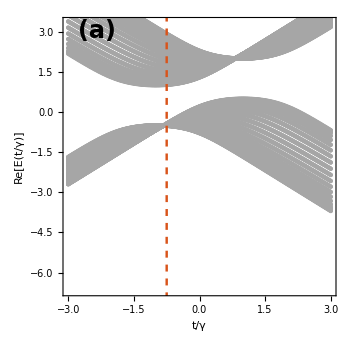
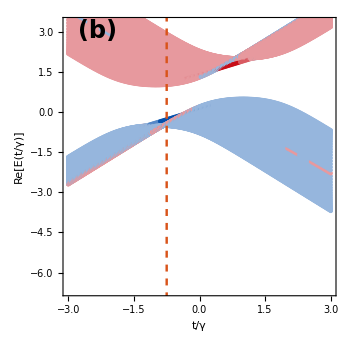
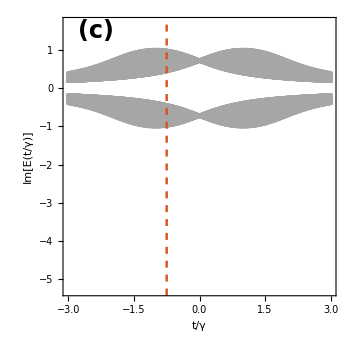
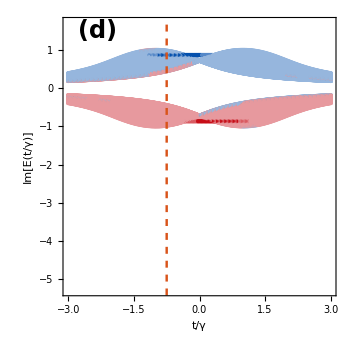
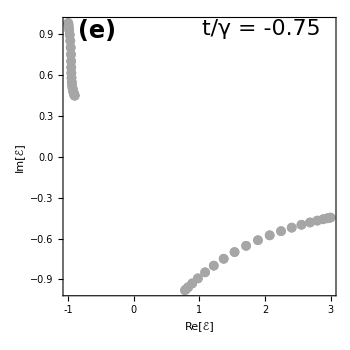
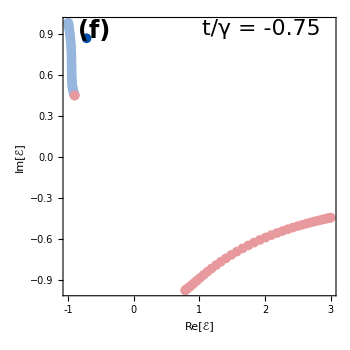
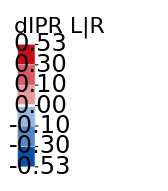
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics--Graphics-

```mathematica
(* ================================================================*)
(*FINAL 3 x 2 FIGURE*)
(* ================================================================*)

(*figure2=Grid[{{pRePBC,pReOBC},{pImPBC,pImOBC},{pCPBC,pCOBC}},Alignment->Center,(*First entry:between PBC/OBC columns.Second entry:between spectral rows.*)
Spacings->{0.1,1}];*)
figure2=Row[{Grid[{{pRePBC,pReOBC},{pImPBC,pImOBC},{pCPBC,pCOBC}},Spacings->{0.15,0.4}],Spacer[8],legend},Alignment->Top];

figure2
```

```mathematica
nn
```

40

## Export----Phase transition spectra with dIPR colouring

## Export

```mathematica
(* ================================================================EXPORT:Figure 2—Phase-transition spectrum grid (OBC/PBC,Re/Im/Complex) Run after pReOBC,pImOBC,pCOBC,pRePBC,pImPBC,pCPBC,figure2 have all been computed.Tags the fixed model parameters into the filename for quick identification,and writes a companion.txt "recipe" file with every setting needed to reproduce the figure exactly.
================================================================*)If[TrueQ[ExportOption],fileNameBaseDateStringFig2=DateString[{"Year","_","Month","_","Day","_","Hour24","h","Minute","m","Second","s"}];
If[!ValueQ[ThisDir]||!StringQ[ThisDir]||ThisDir==="",ThisDir=NotebookDirectory[]];
dirPathFigure=FileNameJoin[{ThisDir,"Figures"}];
If[!DirectoryQ[dirPathFigure],CreateDirectory[dirPathFigure]];
(*----tag fixed parameters into filename for identification----*)paramTagFig2="_eA"<>ToString[NumberForm[N[εA],{Infinity,3}]]<>"_eB"<>ToString[NumberForm[N[εB],{Infinity,3}]]<>"_Gamma"<>ToString[NumberForm[N[Γ],{Infinity,3}]]<>"_m"<>ToString[NumberForm[N[m],{Infinity,3}]]<>"_t1"<>ToString[NumberForm[N[t1],{Infinity,3}]]<>"_t2"<>ToString[NumberForm[N[t2],{Infinity,3}]]<>"_nn"<>ToString[nn]<>"_dIPRshift"<>ToString[NumberForm[N[δIPRshift],{Infinity,3}]];
figBaseNameFig2=SystemName<>paramTagFig2<>"_SpectrumFigure2_"<>varXSymbol<>"Scan__"<>fileNameBaseDateStringFig2;
Export[FileNameJoin[{dirPathFigure,figBaseNameFig2<>".pdf"}],figure2];
Export[FileNameJoin[{dirPathFigure,figBaseNameFig2<>".png"}],figure2,ImageResolution->300];
Export[FileNameJoin[{dirPathFigure,figBaseNameFig2<>".eps"}],figure2];
(*----companion readme with everything needed to reproduce----*)readmeLinesFig2={"FIGURE 2 REPRODUCTION RECIPE","Generated: "<>fileNameBaseDateStringFig2,"SystemName: "<>SystemName,"","--- Model dimensionality ---","SitesPerCell = "<>ToString[SitesPerCell]<>"  (* A,B sublattice -> 2 dof per unit cell *)","EdgeUcellsDef = "<>ToString[EdgeUcellsDef]<>"  (* number of unit cells defining \"the edge\" *)","nn (OBC unit cells) = "<>ToString[nn],"","--- Fixed global Hamiltonian parameters ---","CurlyEpsilonA = "<>ToString[N[εA]],"CurlyEpsilonB = "<>ToString[N[εB]],"CapitalGamma  = "<>ToString[N[Γ]],"m             = "<>ToString[N[m]],"t1            = "<>ToString[N[t1]],"t2            = "<>ToString[N[t2]],"tol (root-filtering tolerance) = "<>ToString[tol],"","--- Swept axis for Figure 2 (edge-mode / spectrum scan) ---","varXSymbol = "<>ToString[varXSymbol],"varXLabel  = "<>ToString[InputForm[varXLabel]],"varXNorm   = "<>ToString[InputForm[varXNorm]],"xScanMax   = "<>ToString[N[xScanMax]],"nXEdge     = "<>ToString[nXEdge],"pxEdge     = "<>ToString[pxEdge],"","--- Energy-axis window (Re/Im plots) ---","EYmin = "<>ToString[N[EYmin]],"EYmax = "<>ToString[N[EYmax]],"yoffsetUpRe = "<>ToString[N[yoffsetUpRe]],"yoffsetUpIm = "<>ToString[N[yoffsetUpIm]],"","--- Localization metric ---","locMethod = dIPR","DeltaIPRshift = "<>ToString[N[δIPRshift]],"","--- Plot styling / layout ---","individualplotsize = "<>ToString[individualplotsize],"insetReRange = "<>ToString[InputForm[insetReRange]],"insetImRange = "<>ToString[InputForm[insetImRange]],"insetPosition = "<>ToString[InputForm[insetPosition]],"insetRelSize  = "<>ToString[InputForm[insetRelSize]],"insetOpacity  = "<>ToString[insetOpacity],"pointsizeImReplots = "<>ToString[InputForm[pointsizeImReplots]],"pointsizeImReplotsInset = "<>ToString[InputForm[pointsizeImReplotsInset]],"pointsizeCPlot = "<>ToString[pointsizeCPlot],"","--- EP / snapshot line controls ---","showEPLines = "<>ToString[showEPLines],"showSnapshotLine = "<>ToString[showSnapshotLine],"snapshotLineT1 = "<>ToString[N[snapshotLineT1]],"showBranchPointLines = "<>ToString[showBranchPointLines],"flatBandManifold = "<>ToString[flatBandManifold],"","--- Grid layout ---","figure2 = Grid[{{pReOBC, pRePBC}, {pImOBC, pImPBC}, {pCOBC, pCPBC}}, Alignment -> Center, Spacings -> {2, 1}]"};
Export[FileNameJoin[{dirPathFigure,figBaseNameFig2<>"_README.txt"}],StringRiffle[readmeLinesFig2,"\n"],"Text"];
Print["Figure 2 exported to: ",FileNameJoin[{dirPathFigure,figBaseNameFig2<>".pdf"}]];
Print["Recipe README exported to: ",FileNameJoin[{dirPathFigure,figBaseNameFig2<>"_README.txt"}]];];
```

Figure 2 exported to: /Users/carolinamstrasser/Library/CloudStorage/OneDrive-UPVEHU(2)/PhD/FourthYear_phD/Project_Nico/Figures/NH_NNN_Rice_Mele_eA0.000_eB1.500_Gamma1.000_m0.300_t11.100_t21.000_nn40_dIPRshift0.500_SpectrumFigure2_t1Scan__2026_07_30_11h53m37s.pdf

Recipe README exported to: /Users/carolinamstrasser/Library/CloudStorage/OneDrive-UPVEHU(2)/PhD/FourthYear_phD/Project_Nico/Figures/NH_NNN_Rice_Mele_eA0.000_eB1.500_Gamma1.000_m0.300_t11.100_t21.000_nn40_dIPRshift0.500_SpectrumFigure2_t1Scan__2026_07_30_11h53m37s_README.txt

## CHECK — Diagnostic table of the dIPR and histogram

```mathematica
(* ================================================================DIAGNOSTIC—dIPR/IPR table at a chosen t1 (edge-state regime) Builds H=HOBCx[t1Check],diagonalizes it,and tabulates every eigenstate's Re[E],Im[E],IPR,and signed dIPR (Bai-style),sorted by|dIPR|descending so edge states float to the top and bulk states settle at the bottom with their true (small) values.
================================================================*)
ClearAll[dIPRDiagnosticTable];
dIPRDiagnosticTable[t1Check_?NumericQ,δ_:δIPRshift,nShow_Integer:10]:=Module[{H,valsR,vecsR,iprVals,dVals,tbl,sorted,topRows,botRows},H=HOBCx[t1Check];
{valsR,vecsR}=Eigensystem[N@H];
iprVals=IPR/@vecsR;
dVals=dIPRBaiStyle[#,δ]&/@vecsR;
tbl=Table[{i,Re[valsR[[i]]],Im[valsR[[i]]],iprVals[[i]],dVals[[i]]},{i,1,Length[valsR]}];
sorted=ReverseSortBy[tbl,Abs[#[[5]]]&];
Print["t1 = ",t1Check,"   (all other params at §1 global values)"];
Print["Total eigenstates: ",Length[valsR],"   |  Uniform-bulk reference IPR ≃ 1/N = ",N[1/Length[valsR]]];
topRows=Map[NumberForm[#,{6,4}]&,sorted[[1;;Min[nShow,Length[sorted]]]],{2}];
botRows=Map[NumberForm[#,{6,4}]&,sorted[[-Min[nShow,Length[sorted]];;-1]],{2}];
Print["--- Most EDGE-like states (largest |dIPR|) ---"];
Print[Grid[Prepend[topRows,{"idx","Re[E]","Im[E]","IPR","dIPR (signed)"}],Frame->All,Alignment->Center,Background->{None,{LightYellow,None}}]];
Print["--- Most BULK-like states (smallest |dIPR|) ---"];
Print[Grid[Prepend[botRows,{"idx","Re[E]","Im[E]","IPR","dIPR (signed)"}],Frame->All,Alignment->Center,Background->{None,{LightBlue,None}}]];
sorted];
(* ================================================================RUN—check t1≃0.3,an edge-state regime================================================================*)
diagOut=dIPRDiagnosticTable[0.3,δIPRshift,10];
```

t1 = 0.3   (all other params at §1 global values)

Total eigenstates: 40   |  Uniform-bulk reference IPR ≃ 1/N = 0.025

--- Most EDGE-like states (largest |dIPR|) ---

idx | Re[E] | Im[E] | IPR | dIPR (signed)
14 | 1.5495 | -0.8660 | 0.5085 | 0.5085
30 | 0.2515 | 0.8690 | 0.1077 | -0.1077
1 | 2.1273 | -0.8492 | 0.0637 | 0.0637
2 | 2.1155 | -0.8437 | 0.0631 | 0.0631
3 | 2.0961 | -0.8347 | 0.0621 | 0.0621
10 | 1.8176 | -0.7121 | 0.0617 | 0.0617
27 | 0.3604 | 0.8503 | 0.0611 | -0.0611
4 | 2.0698 | -0.8226 | 0.0607 | 0.0607
5 | 2.0374 | -0.8078 | 0.0591 | 0.0591
32 | 0.2160 | 0.8397 | 0.0586 | -0.0586

--- Most BULK-like states (smallest |dIPR|) ---

idx | Re[E] | Im[E] | IPR | dIPR (signed)
22 | -0.9837 | 0.5969 | 0.0497 | -0.0497
21 | -1.0081 | 0.5935 | 0.0496 | -0.0496
19 | 1.5306 | -0.5978 | 0.0495 | 0.0495
11 | 1.7697 | -0.6924 | 0.0490 | 0.0490
18 | 1.5483 | -0.6046 | 0.0488 | 0.0488
12 | 1.7232 | -0.6736 | 0.0484 | 0.0484
17 | 1.5726 | -0.6140 | 0.0482 | 0.0482
13 | 1.6792 | -0.6560 | 0.0479 | 0.0479
16 | 1.6030 | -0.6259 | 0.0478 | 0.0478
15 | 1.6388 | -0.6400 | 0.0477 | 0.0477

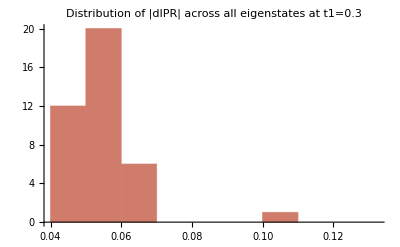

```mathematica
Histogram[Abs[diagOut[[All,5]]],40,FrameLabel->{"|dIPR|","count"},PlotLabel->"Distribution of |dIPR| across all eigenstates at t1=0.3",ChartStyle->ColorData["ThermometerColors"][0.8]]
```

# Fig Appendix.--- M-Riemann spheres

## M-Riemann sphere representation with correct analytic continuation

## Modules for computation of the sphere at snapList points

### Modules for Riemann sphere representation

```mathematica
Clear[NumberMLoops,SheetArrowsLabelling]
NumberMLoops=2;
SheetArrowsLabelling=False; (*Put True in case we want to see in the sphere labelling points if the points are corresponding to the upper or lower Riemann sheet*)
```

```mathematica
(*===================General plotting preferences for winding/dIPR/CondNum/EdgeNum matrices Plots=================*)
plotSz=380;
LF=54;
TF=52;
MemberQ[$FontFamilies,"LMRoman10"]
CommonFontFamStyle="LMRoman10";(*LMRoman10*)
snapListPtsMarkersSize=AbsolutePointSize[7];
Print@Style["The quick brown fox jumps over the lazy dog.\nABCDEFGHIJKLMNOPQRSTUVWXYZ\nabcdefghijklmnopqrstuvwxyz\n0123456789",FontFamily->CommonFontFamStyle,FontSize->24,FontColor->Black]
(*===================General plotting preferences for winding/dIPR/CondNum/EdgeNum matrices Plots=================*)
(*Define these BEFORE commonOpts,and make sure they reference CommonFontFamStyle*)paperStyle=Directive[FontFamily->CommonFontFamStyle,FontSize->LF,FontColor->Black];
tickStyle=Directive[FontFamily->CommonFontFamStyle,FontSize->TF,FontColor->Black];
```

True

The quick brown fox jumps over the lazy dog.
ABCDEFGHIJKLMNOPQRSTUVWXYZ
abcdefghijklmnopqrstuvwxyz
0123456789

```mathematica
snapList
```

{{3/10,1/10,(i)},{11/10,3/10,(ii)},{-3/4,1/4,(iii)}}

```mathematica
(*==============================================================*)
(*Colour map on arg(M)*)
(*==============================================================*)
ClearAll[ArgColourLoop,argColor,argColorLegend];

ArgColourLoop=Function[x,Hue[Mod[x/(2 Pi),1],0.85,0.90]];
argColor[M_?NumericQ]:=ArgColourLoop[Arg[N[M]]];

argColorLegend[]:=BarLegend[{Function[x,Hue[Mod[x/(2 Pi),1],0.85,0.90]],{-Pi,Pi}},LegendLabel->Style["arg(M)",FontFamily->CommonFontFamStyle,FontSize->LF-2,FontColor->Black],LegendMarkerSize->{20,plotSz-100},LabelStyle->Directive[FontFamily->CommonFontFamStyle,FontSize->TF-2,FontColor->Black]];


(*==============================================================*)
(*Riemann sphere geometry*)
(*==============================================================*)
ClearAll[riemannSphereXYZ,sphereGraphics,makeXYZAxes,makeEquator];

riemannSphereXYZ[M_?NumericQ]:=Module[{u,v,r2},
u=Re[N[M]];
v=Im[N[M]];
r2=u^2+v^2;
{2 u/(1+r2),2 v/(1+r2),(r2-1)/(r2+1)}];

sphereGraphics[opacity_:0.14]:={Directive[Opacity[opacity],LightGray,Specularity[White,20]],Sphere[{0,0,0},1]};

makeXYZAxes[axLen_:1.35,axColor_:GrayLevel[0.35]]:=Module[{arrow3D},arrow3D[dir_,lbl_]:={Directive[axColor,Thick],Arrowheads[0.025],Arrow[Tube[{{0,0,0},axLen dir},0.006]],Text[Style[lbl,FontFamily->CommonFontFamStyle,FontSize->TF-2,FontWeight->Bold,FontColor->axColor,Background->None],1.12 axLen dir]};
{arrow3D[{1,0,0},"X"],arrow3D[{0,1,0},"Y"],arrow3D[{0,0,1},"Z"]}];

makeEquator[n_:300]:=Module[{pts},
pts=Table[{Cos[t],Sin[t],0},{t,0,2 Pi,2 Pi/n}];
{Directive[GrayLevel[0.7],Dashed,Thin],Line[pts]}];

ClearAll[makeArgumentMeridians];

makeArgumentMeridians[phis_:Range[-Pi,Pi-Pi/6,Pi/6],rmax_:30,n_:250]:=Module[{pts},Flatten[Table[pts=Table[riemannSphereXYZ[r Exp[I phi]],{r,0,rmax,rmax/n}];
{Directive[GrayLevel[0.82],Thin,Dashed],Line[pts]},{phi,phis}],1]];

ClearAll[makeModulusCircles];

makeModulusCircles[mods_:{0.2,0.5,1,2,5},n_:300]:=Module[{pts},Flatten[Table[pts=Table[riemannSphereXYZ[mod Exp[I theta]],{theta,0,2 Pi,2 Pi/n}];
{Directive[GrayLevel[0.82],Thin],Line[pts]},{mod,mods}],1]];

(*==============================================================*)
(*Coloured loop on the sphere—now solid colour per loop*)
(*==============================================================*)
ClearAll[makeColoredSphereCurveWithXYZ];

makeColoredSphereCurveWithXYZ[mLoop_List,color_,closeQ_:True,thickness_:0.012]:=Module[{loop,xyz,segs},loop=N[mLoop];
If[closeQ&&First[loop]=!=Last[loop],loop=Append[loop,First[loop]]];
xyz=riemannSphereXYZ/@loop;
segs=Table[{color,Tube[{xyz[[i]],xyz[[i+1]]},thickness]},{i,Length[xyz]-1}];
<|"XYZ"->xyz,"Segments"->segs|>];

(*==============================================================*)
(*Utilities*)
(*==============================================================*)
ClearAll[findArgZeroIndex,prettyNumber];

findArgZeroIndex[zvals_List]:=Module[{args},
args=Arg[N[zvals]];
First@Ordering[Abs[args],1]];

prettyNumber[x_,digits_:3]:=Module[{xc,xr},
xc=Chop[x];
If[Head[xc]===Complex,
If[Chop[Im[xc]]==0,prettyNumber[Re[xc],digits],
Row[{prettyNumber[Re[xc],digits],
If[Im[xc]>=0," + "," - "],
prettyNumber[Abs[Im[xc]],digits]," ⅈ"}]],
xr=Round[xc];
If[Abs[xc-xr]<10^-8,xr,NumberForm[xc,digits]]]];
(*==============================================================*)
(*Global (cross-category) automatic label placement*)
(*==============================================================*)
ClearAll[globalAutomaticOffsets];

(*fixedObstacles:list of {xyz,offsetXYZ} pairs for STATIC labels (the poles) that repel dynamic markers but never move themselves.*)
globalAutomaticOffsets[xyz_List,scale_:0.24,minSep_:0.42,fixedObstacles_List:{}]:=Module[{n,offs,cross,i,j,pass,obsPos},n=Length[xyz];
If[n==0,Return[{}]];
obsPos=If[fixedObstacles==={},{},(#[[1]]+#[[2]])&/@fixedObstacles];
offs=Normalize/@xyz;
Do[If[Abs[xyz[[i,3]]]>0.65,cross=Normalize[Cross[{0,0,1},xyz[[i]]]+10^-10];
offs[[i]]=Normalize[offs[[i]]+0.65 cross];];,{i,n}];
Do[Do[If[i!=j&&Norm[(xyz[[i]]+scale offs[[i]])-(xyz[[j]]+scale offs[[j]])]<minSep,cross=Normalize[Cross[xyz[[i]],xyz[[j]]]+10^-10];
offs[[i]]=Normalize[offs[[i]]+0.7 cross];
offs[[j]]=Normalize[offs[[j]]-0.7 cross];];,{i,n-1},{j,i+1,n}];
(*Repel dynamic labels away from the FIXED pole label positions*)Do[If[Norm[(xyz[[i]]+scale offs[[i]])-obsPos[[o]]]<minSep,cross=Normalize[xyz[[i]]-obsPos[[o]]+10^-10];
offs[[i]]=Normalize[offs[[i]]+0.8 cross];];,{i,n},{o,Length[obsPos]}];,{pass,5}];
scale Normalize/@offs];

(*==============================================================*)(*Common loop colours*)(*==============================================================*)
ClearAll[loopPalette];

loopPalette={
RGBColor[0.20,0.70,0.20],(*green*)
RGBColor[0.90,0.45,0.00],(*orange*)
RGBColor[0.75,0.20,0.70],    (*purple*)
RGBColor[0.00,0.35,0.85](*blue*)};
(*==============================================================*)
(*Main sphere-plot assembler*)
(*==============================================================*)
(*==============================================================*)
(*Main sphere-plot assembler—fixed palette,no argColor*)
(*==============================================================*)
ClearAll[riemannSpherePlotM];

riemannSpherePlotM[mLoops_List,mDeg_List:{},mBranch_List:{},loopLabels_List:{},zvalsForLoops_List:{}]:=Module[{curveData,curves,markerXYZ,idx0,z0,labelsUsed,loopColors,loopTags,degNum,brNum,allXYZ,allTags,allColors,allOffs,nLoop,nDeg,nBr,loopMarkerRadius,specialMarkerRadius,poleMarkerRadius,degMarks,brMarks,loopChips,degChips,brChips,poleChips,legendRow,sphereFig,northMark,southMark,poleObstacles,fixedView={1.7,-2.1,1.2}},idx0=If[zvalsForLoops==={},1,findArgZeroIndex[zvalsForLoops]];
z0=If[zvalsForLoops==={},1,zvalsForLoops[[idx0]]];
(*==============================================================*)(*Marker sizes*)(*==============================================================*)
loopMarkerRadius=0.045;
specialMarkerRadius=0.055;
poleMarkerRadius=0.060;
(*==============================================================*)(*Fixed colour palette*)(*==============================================================*)
loopColors=Take[loopPalette,Length[mLoops]];
loopTags=Table["M"<>ToString[i],{i,Length[mLoops]}];

labelsUsed=If[loopLabels==={},{Row[{Subscript["M","+"]," (z=",prettyNumber[z0],")"}],Row[{Subscript["M","-"]," (z=",prettyNumber[z0],")"}]},loopLabels];
curveData=MapThread[makeColoredSphereCurveWithXYZ[#1,#2,True,0.015]&,{mLoops,loopColors}];
curves=Flatten[curveData[[All,"Segments"]],1];
markerXYZ=curveData[[All,"XYZ"]][[All,idx0]];
degNum=Select[N[mDeg],NumericQ];
brNum=Select[N[mBranch],NumericQ];
nLoop=Length[markerXYZ];
nDeg=Length[degNum];
nBr=Length[brNum];
poleObstacles={{{0,0,-1},{0,0,-0.22}},{{0,0,1},{0,0,0.22}}};
allXYZ=Join[markerXYZ,riemannSphereXYZ/@degNum,riemannSphereXYZ/@brNum];
allTags=Join[loopTags,Table["Mdeg"<>ToString[i],{i,nDeg}],Table["Mbr"<>ToString[i],{i,nBr}]];
allColors=Join[loopColors,ConstantArray[Blue,nDeg],ConstantArray[Red,nBr]];
allOffs=globalAutomaticOffsets[allXYZ,0.24,0.42,poleObstacles];

(*==============================================================*)
(*Degeneracy points*)(*==============================================================*)degMarks=Table[With[{k=nLoop+i},{Directive[Blue,Specularity[White,25]],Sphere[allXYZ[[k]],specialMarkerRadius],{Directive[Blue,Thin],Line[{allXYZ[[k]],allXYZ[[k]]+allOffs[[k]]}]},Text[Style[ToString[i],FontFamily->CommonFontFamStyle,FontSize->TF-5,FontWeight->Bold,FontColor->Blue,Background->None],allXYZ[[k]]+allOffs[[k]]]}],{i,nDeg}];
(*==============================================================*)(*Branch points*)(*==============================================================*)brMarks=Table[With[{k=nLoop+nDeg+i},{Directive[Red,Specularity[White,25]],Sphere[allXYZ[[k]],specialMarkerRadius],{Directive[Red,Thin],Line[{allXYZ[[k]],allXYZ[[k]]+allOffs[[k]]}]},Text[Style[ToString[i],FontFamily->CommonFontFamStyle,FontSize->TF-5,FontWeight->Bold,FontColor->Red,Background->None],allXYZ[[k]]+allOffs[[k]]]}],{i,nBr}];
(*==============================================================*)(*Poles*)(*==============================================================*)southMark={Black,Sphere[{0,0,-1},poleMarkerRadius],Text[Style["0",FontFamily->CommonFontFamStyle,FontSize->TF-3,FontWeight->Bold,Background->None],{0,0,-1.22}]};
northMark={Black,Sphere[{0,0,1},poleMarkerRadius],Text[Style["∞",FontFamily->CommonFontFamStyle,FontSize->TF-3,FontWeight->Bold,Background->None],{0,0,1.22}]};
(*Kept only for backwards compatibility*)loopChips={};
degChips={};
brChips={};
poleChips={};
legendRow="";
(*==============================================================*)(*Graphics*)(*==============================================================*)sphereFig=Graphics3D[{sphereGraphics[0.18],makeXYZAxes[],makeEquator[],curves,degMarks,brMarks,northMark,southMark},Boxed->False,Axes->False,SphericalRegion->True,Lighting->"Neutral",ViewPoint->fixedView,ImagePadding->40,PlotRangePadding->Scaled[0.08],ImageSize->plotSz,Background->White,LabelStyle->paperStyle];
<|"Sphere"->sphereFig,"Legend"->legendRow|>];
(*==============================================================*)
(*==============================================================*)
(*==============================================================*)
(*(*==============================================================*)
(*Panel tag:applied to the Graphics3D BEFORE wrapping into Column*)
(*==============================================================*)
ClearAll[addPanelTag];

addPanelTag[plotAssoc_Association,tag_]:=Module[{taggedSphere},taggedSphere=Show[plotAssoc["Sphere"],Epilog->Inset[Style[tag,FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],Scaled[{0.06,0.94}],{Left,Top}]];
Column[{Legended[taggedSphere,argColorLegend[]],Spacer[4],plotAssoc["Legend"]},Alignment->Center]];

(*Backward-compat:if a bare Graphics3D/Column is passed instead of the Association,fall back to plain Show (keeps old call sites safe).*)
addPanelTag[g_,tag_]:=Show[g,Epilog->Inset[Style[tag,FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],Scaled[{0.06,0.94}],{Left,Top}]];*)
ClearAll[addPanelTag];

(*Now returns ONLY the tagged sphere+arg(M) colorbar—the per-panel "Legend" (loopChips/degChips/brChips/poleChips) is dropped entirely,since makeCompactLegendCaption[] will serve as the single shared legend placed once below the whole figure grid.*)
(*==============================================================*)(*Panel tag—no colourbar anymore,loops are flat-coloured*)(*==============================================================*)
ClearAll[addPanelTag];

addPanelTag[plotAssoc_Association,tag_]:=Module[{taggedSphere},taggedSphere=Show[plotAssoc["Sphere"],Epilog->Inset[Style[tag,FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],Scaled[{0.06,0.94}],{Left,Top}]];
taggedSphere]

(*==============================================================*)(*Common legend*)(*==============================================================*)
ClearAll[chip,makeCompactLegendCaption];

chip[col_]:=Graphics[{EdgeForm[{Black,Thin}],col,Disk[]},ImageSize->41,PlotRange->1.1];

makeCompactLegendCaption[nLoops_Integer]:=Module[{loopEntries,loopLabels},loopLabels={Subscript["M","+"],Subscript["M","-"]};
loopEntries=Flatten@Table[{chip[loopPalette[[i]]]," ",Style[loopLabels[[i]],Bold],If[i<nLoops,Spacer[18],Nothing]},{i,Min[nLoops,Length[loopLabels]]}];
Row[Join[loopEntries,{Spacer[30],chip[Blue]," ",Style[Subscript["M","deg"],Bold],Spacer[30],chip[Red]," ",Style[Subscript["M","br"],Bold],Spacer[30],chip[Black]," ",Style["0",Bold],Spacer[30],chip[Black]," ",Style["∞",Bold]}],BaseStyle->Directive[FontFamily->CommonFontFamStyle,FontSize->TF-3,FontColor->Black]]]

(*
makeCompactLegendCaption[nLoops_Integer]:=Module[{loopEntries},loopEntries=Flatten@Table[{chip[loopPalette[[i]]]," ",Style[Subscript["M",i],Bold],If[i<nLoops,Spacer[18],Nothing]},{i,nLoops}];
Row[Join[loopEntries,{Spacer[30],chip[Blue]," ",Style[Subscript["M","deg"],Bold],Spacer[30],chip[Red]," ",Style[Subscript["M","br"],Bold],Spacer[30],chip[Black]," ",Style["0",Bold],Spacer[30],chip[Black]," ",Style["∞",Bold]}],BaseStyle->Directive[FontFamily->CommonFontFamStyle,FontSize->TF-3,FontColor->Black]]];*)(*(*Backward-compat fallback unchanged*)
addPanelTag[g_,tag_]:=Show[g,Epilog->Inset[Style[tag,FontFamily->CommonFontFamStyle,FontSize->LF,FontWeight->Bold],Scaled[{0.06,0.94}],{Left,Top}]];*)
```

### Mj loop tracking with analytic continuation through z

```mathematica
(*==============================================================*)
(*Continuous M_-(z) and M_+(z) branches on the ordinary BZ*)
(*==============================================================*)
ClearAll[analyticMTracks];

analyticMTracks[zlist_List,p_Association]:=Module[{t,tp,dz,znum,discVals,s0,sCont,denom,rootMinus,rootPlus,endCand,closureError,exchangedQ},
t=p["t1"];
tp=p["t2"];
dz=dzFunc[p];
znum=N[zlist];
discVals=dz^2+(t+tp/znum) (t+tp znum);
(*Fix a square-root value at the initial BZ point.*)
s0=Sqrt[First[discVals]];
(*Continue sqrt[Delta(z)] by nearest-neighbour continuity.*)sCont=FoldList[Function[{prev,d},With[{cand=Sqrt[d]},If[Abs[cand-prev]<=Abs[-cand-prev],cand,-cand]]],s0,Rest[discVals]];
denom=t+tp znum;
(*From (t+t'z) M+Gamma=sigma sqrt[Delta(z)]:sigma=+1 gives M_-;sigma=-1 gives M_+.*)
rootMinus=(-dz+sCont)/denom;
rootPlus=(-dz-sCont)/denom;
(*Diagnostic:continue one additional infinitesimal BZ step conceptually by comparing the last continued root to the initial choice.This only diagnoses the chosen sampled path.*)
endCand=Last[sCont];
closureError=Min[Abs[endCand-First[sCont]],Abs[endCand+First[sCont]]];
exchangedQ=Abs[endCand+First[sCont]]<Abs[endCand-First[sCont]];
<|"RootMinus"->rootMinus,"RootPlus"->rootPlus,(*Backward-compatible aliases used by your plotting call.*)
"Root1"->rootMinus,"Root2"->rootPlus,"SqrtCont"->sCont,"ClosureError"->closureError,"SheetsExchangedAlongSampledLoop"->exchangedQ|>];
```

### Raw algebraic landmarks (recap)

```mathematica
ClearAll[dzFunc,MdegFunc,MbrFunc]
```

```mathematica
(* ================================================================---------------------------------------------------------------- 
dzFunc extracts Gamma=p["Γ"] (confirmed consistent with your own analyticMTracks,which already does dz=dzFunc[p]).MdegFunc/MbrFunc are your closed-form generators,unchanged.If you already have these three defined earlier in the notebook,this cell is a harmless no-op recap-- keep only one copy.
================================================================*)
ClearAll[dzFunc,MdegFunc,MbrFunc]

dzFunc[assoc_Association]:=assoc["Γ"];

MdegFunc[assoc_Association,sig1_,sig2_]:=Module[{tp,m},tp=assoc["t2"];m=assoc["m"];
(sig1 tp+sig2 Sqrt[tp^2-4 m^2])/(2 m)];

MbrFunc[assoc_Association,s1_,s2_]:=Module[{t,tp,dz,delta},t=assoc["t1"];
tp=assoc["t2"];
dz=dzFunc[assoc];
delta=2 (dz+s1 I tp);
(-delta+s2 Sqrt[delta^2+4 t^2])/(2 t)];
```

### Momenta associated with each landmark

```mathematica
(* ================================================================---------------------------------------------------------------- g(M,z) as a quadratic in z:A z^2+B z+C=0 with A=t2 M^2,B=t1 M^2+2 Gamma M-t1,C=-t2.Branch points:the repeated root z* =-B/(2A).Degeneracy points:the two DISTINCT roots z1,z2 of the same quadratic,evaluated at M=M_deg.
================================================================*)
ClearAll[branchPointZStar,degPointZ1Z2]

branchPointZStar[M_,p_Association]:=Module[{t,tp,Gamma0},t=p["t1"];tp=p["t2"];
Gamma0=dzFunc[p];
-(t M^2+2 Gamma0 M-t)/(2 tp M^2)];

degPointZ1Z2[M_,p_Association]:=Module[{t,tp,Gamma0,A,B,C,sq},t=p["t1"];tp=p["t2"];
Gamma0=dzFunc[p];
A=tp M^2;B=t M^2+2 Gamma0 M-t;C=-tp;
sq=Sqrt[B^2-4 A C];
{(-B+sq)/(2 A),(-B-sq)/(2 A)}];
```

### Delta(z) and the unsquared Riemann-sheet test

```mathematica
(* ================================================================In[498]:=SUBSECTION—Delta(z) and the unsquared Riemann-sheet test---------------------------------------------------------------- Delta(z)=Gamma^2+(t+tp/z)(t+tp z) (same expression as the "discVals" line inside your analyticMTracks).A point (M,z) on g(M,z)=0 lies on branch M_sigma(z) iff (t+tp z) M+Gamma=sigma*Sqrt[Delta(z)],sigma=+-1. Convention (matches your analyticMTracks comment):sigma=+1->M_-,sigma=-1->M_+.This unsquared relation is the ONLY correct sheet test;squaring it just reproduces g(M,z)=0 and destroys sigma.
================================================================*)ClearAll[deltaOfZ,unsquaredSheetSigma,sigmaToSheetLabel]

deltaOfZ[z_,Gamma0_,t_,tp_]:=Gamma0^2+(t+tp/z) (t+tp z);

unsquaredSheetSigma[M_,z_,Gamma0_,t_,tp_,sqrtDeltaContinued_]:=Module[{lhs,ratio,sigma,residual},lhs=(t+tp z) M+Gamma0;
ratio=lhs/sqrtDeltaContinued;
sigma=Round[Re[ratio]];
residual=Abs[ratio-sigma];
<|"Sigma"->sigma,"Ratio"->ratio,"Residual"->residual|>];

sigmaToSheetLabel[1]:="M-";
sigmaToSheetLabel[-1]:="M+";
sigmaToSheetLabel[_]:="Ambiguous";
```

### Analytic continuation engine for Sqrt[Delta] off the ordinary BZ

```mathematica
(* ================================================================In[503]:=SUBSECTION—Analytic continuation engine for Sqrt[Delta] off the ordinary BZ---------------------------------------------------------------- Your analyticMTracks continues Sqrt[Delta(z)] point-to-point ONLY along the sampled unit-circle zlist (nearest-neighbour continuity,FoldList).M_br/M_deg live at z*or z1,z2 which are generically OFF that circle,so we need the same idea (nearest-branch continuity) along a NEW path from a BZ base point out to the target z.Path:geometric (log-linear) interpolation z(s)=z0^{1-s} z1^{s},s=0..1,using the minimal-angle representative of Arg[z1] relative to Arg[z0] (this is the explicit path convention-- see project notes:whenever the physics doesn't fix the path,one must be chosen and stated).At each step we predict the next value by linear extrapolation of the last two continued values and keep whichever of+-Sqrt[Delta(z(s_k))] is closer to the prediction.If the chosen branch jumps too far relative to the prediction (a sign a true branch point of Delta is nearby),the sub-step is adaptively bisected rather than accepted blindly.
================================================================*)
ClearAll[continueSqrtDelta]

Options[continueSqrtDelta]={"NSteps"->200,"MaxBisect"->6,"RelTol"->0.25};

continueSqrtDelta[z0_,sqrt0_,z1_,Gamma0_,t_,tp_,OptionsPattern[]]:=Module[{nSteps,r0,r1,th0,th1,path,sqrtPrev,sqrtPrevPrev,k,tol,maxBis,lowConf,dsq},nSteps=OptionValue["NSteps"];
tol=OptionValue["RelTol"];
maxBis=OptionValue["MaxBisect"];
lowConf=False;
r0=Abs[z0];r1=Abs[z1];
th0=Arg[z0];
th1=th0+Mod[Arg[z1]-th0+Pi,2 Pi]-Pi;
path=Table[(r0^(1-s) r1^s) Exp[I ((1-s) th0+s th1)],{s,0.,1.,1./nSteps}];
If[Last[path]!=z1,AppendTo[path,z1]];
sqrtPrevPrev=Missing[];
sqrtPrev=sqrt0;
Do[Module[{zCurr=path[[k]],pred,root1,root2,chosen,relJump},dsq=deltaOfZ[zCurr,Gamma0,t,tp];
root1=Sqrt[dsq];root2=-root1;
pred=If[MissingQ[sqrtPrevPrev],sqrtPrev,2 sqrtPrev-sqrtPrevPrev];
chosen=If[Abs[root1-pred]<=Abs[root2-pred],root1,root2];
relJump=Abs[chosen-pred]/(Abs[pred]+10^-12);
If[relJump>tol,Module[{nSub=4,zzPrev=path[[k-1]],zzNew,dsqSub,r1s,r2s,predSub,chosenSub,sqPrev=sqrtPrev,sqPrevPrev=sqrtPrevPrev,bisectCount=0,ok},While[bisectCount<maxBis,ok=True;
Module[{localPrev=sqPrev,localPrevPrev=sqPrevPrev,zzLocal=zzPrev,j},Do[zzNew=zzLocal+(zCurr-zzLocal)/(nSub-j+1);
dsqSub=deltaOfZ[zzNew,Gamma0,t,tp];
r1s=Sqrt[dsqSub];r2s=-r1s;
predSub=If[MissingQ[localPrevPrev],localPrev,2 localPrev-localPrevPrev];
chosenSub=If[Abs[r1s-predSub]<=Abs[r2s-predSub],r1s,r2s];
If[Abs[chosenSub-predSub]/(Abs[predSub]+10^-12)>tol,ok=False];
localPrevPrev=localPrev;localPrev=chosenSub;zzLocal=zzNew,{j,1,nSub}];
If[ok,sqPrevPrev=localPrevPrev;sqPrev=localPrev]];
If[ok,Break[],nSub*=2;bisectCount++]];
If[bisectCount>=maxBis,lowConf=True];
sqrtPrevPrev=sqPrevPrev;sqrtPrev=sqPrev],sqrtPrevPrev=sqrtPrev;sqrtPrev=chosen]],{k,2,Length[path]}];
<|"Value"->sqrtPrev,"LowConfidence"->lowConf|>];
```

### Bootstrapping the continuation base point

```mathematica
(* ================================================================In[512]:=SUBSECTION—Bootstrapping the continuation base point---------------------------------------------------------------- YOUR analyticMTracks ALREADY continues Sqrt[Delta(z)] along zlist and returns it as "SqrtCont".So the correctly-signed base value is simply SqrtCont at the same BZ index used everywhere else (findArgZeroIndex[zlist])-- no need to reconstruct it from RootMinus (both are algebraically identical,but this is direct and avoids a spurious division by t1+t2*z0).
================================================================*)
ClearAll[bootstrapBaseSqrtDelta]

bootstrapBaseSqrtDelta[p_Association]:=Module[{tracked,idx0,z0},
tracked=analyticMTracks[zlist,p];
idx0=findArgZeroIndex[zlist];
z0=zlist[[idx0]];
<|"z0"->z0,"Sqrt0"->tracked["SqrtCont"][[idx0]]|>];
```

### Sheet-tagged landmarks:getMbranchPoints,getMdegPoints

```mathematica
(* ================================================================In[515]:=SUBSECTION—Sheet-tagged landmarks:getMbranchPoints,getMdegPoints---------------------------------------------------------------- Same call signature as your original functions:getMbranchPoints[p]/getMdegPoints[p],with an optional second argument nSteps (path continuation resolution,default 60;NOT a precision spec).Returns an Association:"Values"->{M1,M2,M3,M4} (numbers,theoretical Index order,IDENTICAL to MbrFunc/MdegFunc-- see In[490]) "Sheets"->{"M+"|"M-"|"Ambiguous",...} "Details"->full per-point diagnostics (zStar/z1,z2,Sigma,Residual,LowConfidence) Index order:M_br:1=(-1,+1) 2=(-1,-1) 3=(+1,+1) 4=(+1,-1) M_deg:1=(+1,+1) 2=(+1,-1) 3=(-1,+1) 4=(-1,-1)================================================================*)


ClearAll[numericizeAssoc]

numericizeAssoc[p_Association]:=Association[KeyValueMap[#1->N[#2]&,p]];ClearAll[getMbranchPoints,getMdegPoints]

ClearAll[continueSqrtDeltaRobust]

continueSqrtDeltaRobust[z0_,sqrt0_,z1_,Gamma0_,t_,tp_,nStepsStart_:60,maxNSteps_:2000]:=Module[{nSteps=nStepsStart,result},
result=continueSqrtDelta[z0,sqrt0,z1,Gamma0,t,tp,"NSteps"->nSteps];
While[result["LowConfidence"]&&nSteps<maxNSteps,nSteps=Min[2 nSteps,maxNSteps];
result=continueSqrtDelta[z0,sqrt0,z1,Gamma0,t,tp,"NSteps"->nSteps];];
Append[result,"NStepsUsed"->nSteps]];

ClearAll[getMbranchPoints,getMdegPoints]

getMbranchPoints[pIn_Association,nSteps_Integer:60]:=Module[{p,t,tp,Gamma0,base,rawSpec,details},
p=numericizeAssoc[pIn];
t=p["t1"];tp=p["t2"];Gamma0=dzFunc[p];
base=bootstrapBaseSqrtDelta[p];
rawSpec={{1,-1,1},{2,1,1},{3,-1,-1},{4,1,-1}};(*CORRECTED*)details=Map[Module[{idx,s1,s2,M,zStar,cont,classify},{idx,s1,s2}=#;
M=MbrFunc[p,s1,s2];
zStar=branchPointZStar[M,p];
cont=continueSqrtDelta[base["z0"],base["Sqrt0"],zStar,Gamma0,t,tp,"NSteps"->nSteps];
classify=unsquaredSheetSigma[M,zStar,Gamma0,t,tp,cont["Value"]];
<|"Index"->idx,"s"->s1,"eta"->s2,"M"->M,"zStar"->zStar,"SqrtDeltaContinued"->cont["Value"],"LowConfidence"->cont["LowConfidence"],"Sigma"->classify["Sigma"],"Residual"->classify["Residual"],"Sheet"->sigmaToSheetLabel[classify["Sigma"]],(*Main-text closed-form prediction:eta=+1->M-,eta=-1->M+*)"SheetPredictedFromEta"->If[s2==1,"M-","M+"]|>]&,rawSpec];
<|"Values"->details[[All,"M"]],"Sheets"->details[[All,"Sheet"]],"Details"->details|>];

getMdegPoints[pIn_Association,nSteps_Integer:60]:=Module[{p,t,tp,Gamma0,base,rawSpec,details},p=numericizeAssoc[pIn];
t=p["t1"];tp=p["t2"];Gamma0=dzFunc[p];
base=bootstrapBaseSqrtDelta[p];
rawSpec={{1,1,1},{2,1,-1},{3,-1,1},{4,-1,-1}};
details=Map[Module[{idx,sig1,sig2,M,zRoots,z1,z2,cont1,cont2,cl1,cl2},{idx,sig1,sig2}=#;
M=MdegFunc[p,sig1,sig2];
zRoots=degPointZ1Z2[M,p];
z1=zRoots[[1]];z2=zRoots[[2]];
cont1=continueSqrtDeltaRobust[base["z0"],base["Sqrt0"],z1,Gamma0,t,tp,nSteps];
cont2=continueSqrtDeltaRobust[base["z0"],base["Sqrt0"],z2,Gamma0,t,tp,nSteps];
cl1=unsquaredSheetSigma[M,z1,Gamma0,t,tp,cont1["Value"]];
cl2=unsquaredSheetSigma[M,z2,Gamma0,t,tp,cont2["Value"]];
<|"Index"->idx,"s"->sig1,"eta"->sig2,"M"->M,"z1"->z1,"z2"->z2,"Sigma1"->cl1["Sigma"],"Sigma2"->cl2["Sigma"],"Sheet1"->sigmaToSheetLabel[cl1["Sigma"]],"Sheet2"->sigmaToSheetLabel[cl2["Sigma"]],"LowConfidence"->(cont1["LowConfidence"]||cont2["LowConfidence"]),"NStepsUsed"->Max[cont1["NStepsUsed"],cont2["NStepsUsed"]],"Sheet"->sigmaToSheetLabel[cl1["Sigma"]]|>]&,rawSpec];
<|"Values"->details[[All,"M"]],"Sheets"->details[[All,"Sheet"]],"Details"->details|>];
```

### Sheet-aware Riemann-sphere renderer

```mathematica
ClearAll[labelOffsetCorrection];

ClearAll[labelOffsetCorrection];

labelOffsetCorrection=<|"deg1"->{0,0,0},"deg2"->{0,0,0},"deg3"->{0.10,-0.06,0},"deg4"->{0,0,0},"br1"->{-0.08,0.06,0},"br2"->{0,0,0},"br3"->{0,0,0},"br4"->{0.05,0.02,0}|>;
```

```mathematica
(* ================================================================In[524]:=SUBSECTION—Sheet-aware Riemann-sphere renderer---------------------------------------------------------------- Reuses riemannSphereXYZ,sphereGraphics,makeXYZAxes,makeEquator,makeColoredSphereCurveWithXYZ,globalAutomaticOffsets,loopPalette,CommonFontFamStyle,TF,paperStyle,plotSz-- all already defined in your notebook.Colours each M_br/M_deg marker by the loop colour of the sheet it was classified onto:loopPalette[[1]]=M_+colour,loopPalette[[2]]=M_-colour (matching the {RootMinus,RootPlus} order you pass as mLoops elsewhere);Gray flags "Ambiguous" (needs re-check,e.g.increase nSteps).Labels show Index (1-4) plus an up/down arrow for the assigned sheet.Your ORIGINAL riemannSpherePlotM is untouched and still works if you feed it plain["Values"] lists.
================================================================*)
ClearAll[sheetColor,riemannSpherePlotMSheetAware]

sheetColor["M+"]:=loopPalette[[1]];
sheetColor["M-"]:=loopPalette[[2]];
sheetColor[_]:=Gray;


riemannSpherePlotMSheetAware[mLoops_List,degTagged_Association,brTagged_Association,zvalsForLoops_List:{},tag_:""]:=Module[{curveData,curves,markerXYZ,idx0,z0,loopColors,degVals,degSheets,brVals,brSheets,allXYZ,allOffs,nLoop,nDeg,nBr,specialMarkerRadius,poleMarkerRadius,degMarks,brMarks,sphereFig,northMark,southMark,poleObstacles,fixedView={1.7,-2.1,1.2}},idx0=If[zvalsForLoops==={},1,findArgZeroIndex[zvalsForLoops]];
z0=If[zvalsForLoops==={},1,zvalsForLoops[[idx0]]];
specialMarkerRadius=0.055;
poleMarkerRadius=0.060;
loopColors=Take[loopPalette,Length[mLoops]];
curveData=MapThread[makeColoredSphereCurveWithXYZ[#1,#2,True,0.015]&,{mLoops,loopColors}];
curves=Flatten[curveData[[All,"Segments"]],1];
markerXYZ=curveData[[All,"XYZ"]][[All,idx0]];
degVals=N[degTagged["Values"]];degSheets=degTagged["Sheets"];
brVals=N[brTagged["Values"]];brSheets=brTagged["Sheets"];
nLoop=Length[markerXYZ];nDeg=Length[degVals];nBr=Length[brVals];
poleObstacles={{{0,0,-1},{0,0,-0.22}},{{0,0,1},{0,0,0.22}}};
allXYZ=Join[markerXYZ,riemannSphereXYZ/@degVals,riemannSphereXYZ/@brVals];
allOffs=globalAutomaticOffsets[allXYZ,0.34,0.55,poleObstacles];
Switch[tag,
"(i)",(
(*red 3->right*)
allOffs[[nLoop+nDeg+3]]+={+0.22,0.00,+0.32};
(*red 2->left*)
allOffs[[nLoop+nDeg+2]]+={-0.42,-0.20,-0.12};
(*blue 4->left*)
allOffs[[nLoop+4]]+={-0.32,0.00,+0.32};
(*blue 2->right*)
allOffs[[nLoop+2]]+={+0.12,0.00,0.00};),
"(ii)",(
(*red 2->left*)
allOffs[[nLoop+nDeg+2]]+={-0.22,0.00,+0.32};
(*red 1->right*)
allOffs[[nLoop+nDeg+1]]+={+0.32,0.00,0.00};),
"(iii)",
((*red 2->right*)
allOffs[[nLoop+nDeg+2]]+={+0.10,0.00,+0.40};
(*blue 3->upwards*)
allOffs[[nLoop+3]]+={0.00,0.00,+0.20};),_,Null];
(*FAMILY colour=fill;SHEET=arrow suffix only*)degMarks=Table[With[{k=nLoop+i,fillCol=Blue,lbl=If[SheetArrowsLabelling,ToString[i]<>Which[degSheets[[i]]=="M+","↑",degSheets[[i]]=="M-","↓",True,"?"],ToString[i]]},{Directive[fillCol,Specularity[White,25]],Sphere[allXYZ[[k]],specialMarkerRadius],{Directive[fillCol,Thin],Line[{allXYZ[[k]],allXYZ[[k]]+allOffs[[k]]}]},Text[Style[lbl,FontFamily->CommonFontFamStyle,FontSize->TF-5,FontWeight->Bold,FontColor->fillCol,Background->None],allXYZ[[k]]+allOffs[[k]]+Lookup[labelOffsetCorrection,"deg"<>ToString[i],{0,0,0}]]}],{i,nDeg}];
brMarks=Table[With[{k=nLoop+nDeg+i,fillCol=Red,lbl=If[SheetArrowsLabelling,ToString[i]<>Which[brSheets[[i]]=="M+","↑",brSheets[[i]]=="M-","↓",True,"?"],ToString[i]]},{Directive[fillCol,Specularity[White,25]],Sphere[allXYZ[[k]],specialMarkerRadius],{Directive[fillCol,Thin],Line[{allXYZ[[k]],allXYZ[[k]]+allOffs[[k]]}]},Text[Style[lbl,FontFamily->CommonFontFamStyle,FontSize->TF-5,FontWeight->Bold,FontColor->fillCol,Background->None],allXYZ[[k]]+allOffs[[k]]+Lookup[labelOffsetCorrection,"br"<>ToString[i],{0,0,0}]]}],{i,nBr}];
southMark={Black,Sphere[{0,0,-1},poleMarkerRadius],Text[Style["0",FontFamily->CommonFontFamStyle,FontSize->TF-3,FontWeight->Bold,Background->None],{0,0,-1.22}]};
northMark={Black,Sphere[{0,0,1},poleMarkerRadius],Text[Style["∞",FontFamily->CommonFontFamStyle,FontSize->TF-3,FontWeight->Bold,Background->None],{0,0,1.22}]};
sphereFig=Graphics3D[{sphereGraphics[0.18],makeXYZAxes[],makeEquator[],curves,degMarks,brMarks,northMark,southMark},Boxed->False,Axes->False,SphericalRegion->True,Lighting->"Neutral",ViewPoint->fixedView,ImagePadding->40,PlotRangePadding->Scaled[0.08],ImageSize->plotSz,Background->White,LabelStyle->paperStyle];
<|"Sphere"->sphereFig,"Legend"->""|>];
```

### Sheet-aware snapshot assembly

```mathematica
(* ================================================================In[536]:=SUBSECTION—Sheet-aware snapshot assembly---------------------------------------------------------------- Drop-in sibling of your existing spherePlotAtSnap/panelPlots,built on your real snapList ("(i)","(ii)","(iii)") and axis label variables (varXFullLabel,varYFullLabel).Requires makeCompactLegendCaption[2] (already defined in your notebook).
================================================================*)
ClearAll[spherePlotAtSnapSheetAware]

spherePlotAtSnapSheetAware[{xv_,yv_,tag_}]:=Module[{p,tracked,degT,brT,plot,topRow},p=resolveParams[xv,yv];
tracked=analyticMTracks[zlist,p];
degT=getMdegPoints[p,60];
brT=getMbranchPoints[p,60];
plot=riemannSpherePlotMSheetAware[{tracked["RootMinus"],tracked["RootPlus"]},degT,brT,zlist,tag];
topRow=Grid[{{Style[tag,FontFamily->CommonFontFamStyle,FontSize->TF,FontWeight->Bold],Style[Grid[{{varXFullLabel,"=",N@NumberForm[xv,{3,2}]},{varYFullLabel,"=",N@NumberForm[yv,{3,2}]}},Alignment->Left,Spacings->{1,0.2}],FontFamily->CommonFontFamStyle,FontSize->TF]}},Alignment->{{Left,Left},Top},Spacings->{1.5,0}];
Column[{Item[topRow,ItemSize->Fit],Item[Show[plot["Sphere"],ImageSize->550,ImagePadding->{{50,10},{-10,5}}],Alignment->Top]},Alignment->Center,Spacings->0]];

spherePlotsSheetAware=spherePlotAtSnapSheetAware/@snapList;

panelPlotsSheetAware=Column[{Grid[{spherePlotsSheetAware},Alignment->Center,Spacings->{-3.4,0}],Spacer[1],makeCompactLegendCaption[2]},Alignment->Center]
```

(i) | t/γ | = | 0.30
m/γ | = | 0.10
-Graphics3D- | (ii) | t/γ | = | 1.10
m/γ | = | 0.01
-Graphics3D- | (iii) | t/γ | = | -0.75
m/γ | = | 0.25
-Graphics3D-

-Graphics- M_+-Graphics- M_--Graphics- M_deg-Graphics- M_br-Graphics- 0-Graphics- ∞

### Diagnostic sanity check of the continuation sheet

```mathematica
(* ================================================================
This checks whether the continuation-based sheet assignment matches a simple eta-based rule
================================================================*)
Do[Module[{p=resolveParams[snapList[[k,1]],snapList[[k,2]]],brT,degT},
brT=getMbranchPoints[p,60];
degT=getMdegPoints[p,60];
Print["Snapshot ",snapList[[k,3]]," — M_br:"];
Print[Grid[Prepend[Table[With[{d=brT["Details"][[i]]},{d["Index"],NumberForm[d["M"],{4,3}],NumberForm[Abs[d["zStar"]],{4,3}],d["Sheet"],d["SheetPredictedFromEta"],If[d["Sheet"]===d["SheetPredictedFromEta"],"OK","MISMATCH"],NumberForm[d["Residual"],2]}],{i,4}],{"Index","M","|z*|","Sheet(continuation)","Sheet(eta rule)","Agree?","Residual"}],Frame->All,Alignment->Center]];
Print["Snapshot ",snapList[[k,3]]," — M_deg:"];
Print[Grid[Prepend[Table[With[{d=degT["Details"][[i]]},{d["Index"],NumberForm[d["M"],{4,3}],NumberForm[Abs[d["z1"]],{4,3}],NumberForm[Abs[d["z2"]],{4,3}],d["Sheet1"],d["Sheet2"],d["LowConfidence"]}],{i,4}],{"Index","M","|z1|","|z2|","Sheet1","Sheet2","LowConf"}],Frame->All,Alignment->Center]];],{k,Length[snapList]}]
```

Snapshot (i) — M_br:

Index | M | |z*| | Sheet(continuation) | Sheet(eta rule) | Agree? | Residual
1 | 0.076+0.074 ⅈ | 9.430 | M- | M- | OK | 2.7×10^-15
2 | 0.076-0.074 ⅈ | 9.430 | M- | M- | OK | 2.8×10^-15
3 | -6.742+6.593 ⅈ | 0.106 | M+ | M+ | OK | 5.6×10^-17
4 | -6.742-6.593 ⅈ | 0.106 | M+ | M+ | OK | 5.6×10^-17

Snapshot (i) — M_deg:

Index | M | |z1| | |z2| | Sheet1 | Sheet2 | LowConf
1 | 9.899 | 0.020 | 0.519 | M- | M+ | False
2 | 0.101 | 15.590 | 6.287 | M- | M- | False
3 | -0.101 | 50.820 | 1.928 | M+ | M- | False
4 | -9.899 | 0.064 | 0.159 | M+ | M+ | False

Snapshot (ii) — M_br:

Index | M | |z*| | Sheet(continuation) | Sheet(eta rule) | Agree? | Residual
1 | 0.302+0.227 ⅈ | 2.651 | M- | M- | OK | 2.5×10^-16
2 | 0.302-0.227 ⅈ | 2.651 | M- | M- | OK | 2.5×10^-16
3 | -2.120+1.592 ⅈ | 0.377 | M+ | M+ | OK | 1.6×10^-16
4 | -2.120-1.592 ⅈ | 0.377 | M+ | M+ | OK | 1.6×10^-16

Snapshot (ii) — M_deg:

Index | M | |z1| | |z2| | Sheet1 | Sheet2 | LowConf
1 | 3.000 | 0.065 | 1.709 | M- | M+ | False
2 | 0.333 | 4.711 | 1.911 | M- | M- | False
3 | -0.333 | 15.380 | 0.585 | M+ | M- | False
4 | -3.000 | 0.212 | 0.523 | M+ | M+ | False

Snapshot (iii) — M_br:

Index | M | |z*| | Sheet(continuation) | Sheet(eta rule) | Agree? | Residual
1 | -0.199-0.173 ⅈ | 3.799 | M- | M- | OK | 4.7×10^-16
2 | -0.199+0.173 ⅈ | 3.799 | M- | M- | OK | 2.8×10^-16
3 | 2.865-2.494 ⅈ | 0.263 | M+ | M+ | OK | 3.1×10^-16
4 | 2.865+2.494 ⅈ | 0.263 | M+ | M+ | OK | 3.1×10^-16

Snapshot (iii) — M_deg:

Index | M | |z1| | |z2| | Sheet1 | Sheet2 | LowConf
1 | 3.732 | 0.360 | 0.200 | M+ | M+ | False
2 | 0.268 | 0.777 | 17.940 | M- | M+ | False
3 | -0.268 | 2.779 | 5.011 | M- | M- | False
4 | -3.732 | 1.288 | 0.056 | M+ | M- | False

### Comparison check with the theoretical definitions

```mathematica
(* ================================================================Rigorous theoretical prediction check for M_br and M_deg Avoids (zStar)notation which conflicts with Mathematica comments
   ================================================================*)

ClearAll[theoreticalSheetPredictionBr,theoreticalSheetPredictionDeg,runFullCoherenceCheck]

(*---Theoretical M_br sheet prediction---*)
(*At a branch point (M,zStar),we have a double root in z.The unsquared condition (t+t' zStar) M+Gamma=sigma Sqrt[Delta(zStar)] determines the sheet.We compute Sqrt[Delta(zStar)] directly from the discriminant formula WITHOUT continuation-just pick the principal square root and test the ratio.*)

theoreticalSheetPredictionBr[pIn_Association]:=Module[{t,tp,Gamma0,brDetails,p=numericizeAssoc[pIn]},t=p["t1"];tp=p["t2"];
Gamma0=dzFunc[p];
(*Get all four branch points with their double roots*)brDetails=Table[Module[{s,eta,M,zStar,DeltaVal,sqrtDelta,lhs,ratio},{s,eta}=Which[i==1,{-1,1},i==2,{1,1},i==3,{-1,-1},i==4,{1,-1}];
M=MbrFunc[p,s,eta];
zStar=branchPointZStar[M,p];
DeltaVal=deltaOfZ[zStar,Gamma0,t,tp];
sqrtDelta=Sqrt[DeltaVal];(*Principal square root*)lhs=(t+tp zStar) M+Gamma0;
ratio=lhs/sqrtDelta;
<|"Index"->i,"s"->s,"eta"->eta,"M"->M,"zStar"->zStar,"Delta"->DeltaVal,"sqrtDeltaPrincipal"->sqrtDelta,"lhs"->lhs,"ratio"->ratio,"ratioRounded"->Round[Re[ratio]],"isRatioOne"->Abs[ratio-1]<0.01,"isRatioMinusOne"->Abs[ratio+1]<0.01|>],{i,4}];
brDetails];


(*---Theoretical M_deg sheet prediction---*)
(*For degeneracy points,we have TWO distinct z roots z1,z2.The unsquared condition must give the SAME sigma for both,because M_deg belongs to a single sheet.Key:(t+t' z1) M+Gamma=sigma Sqrt[Delta(z1)] AND (t+t' z2) M+Gamma=sigma Sqrt[Delta(z2)] with the SAME sigma.*)

(*---Corrected Theoretical M_deg sheet prediction---*)(*For degeneracy points,we have TWO distinct z roots z1,z2.The unsquared condition must give the SAME sigma for both.KEY INSIGHT:We cannot use principal sqrt independently at z1 and z2 because they might lie on opposite sides of the branch cut.Instead,we compute the RELATIVE sign between sqrtDelta(z1) and sqrtDelta(z2) from the algebraic relation between z1 and z2.From the quadratic g(M,z)=A z^2+B z+C=0:z1+z2=-B/A,z1 z2=C/A=-tp/(tp M^2)=-1/M^2 Also:Delta(z)=Gamma^2+(t+tp/z)(t+tp z) The product sqrtDelta(z1)*sqrtDelta(z2) can be determined algebraically (up to a sign from the branch choice).But more simply:we use the CONTINUATION from the BZ to determine the correct branch at z1,and then use the algebraic relation between z1 and z2 to determine the branch at z2.THE CORRECT THEORETICAL PREDICTION:-Start from the BZ base point where sqrtDelta is known from analyticMTracks-Continue to z1 using the SAME algorithm as continueSqrtDelta-The unsquared condition at z1 gives sigma-This sigma IS the theoretical prediction for the sheet-z2 should give the same sigma IF we use the consistently continued sqrtDelta(z2),not the principal branch*)theoreticalSheetPredictionDeg[pIn_Association]:=Module[{t,tp,Gamma0,base,tracked,degDetails,p=numericizeAssoc[pIn]},t=p["t1"];tp=p["t2"];Gamma0=dzFunc[p];
(*Get the base sqrtDelta from the BZ continuation*)
base=bootstrapBaseSqrtDelta[p];
degDetails=Table[Module[{sig,eta,M,zRoots,z1,z2,cont1,cont2,sqrtDelta1Cont,sqrtDelta2Cont,lhs1,lhs2,ratio1,ratio2,sigma1,sigma2,principalSqrt1,principalSqrt2,ratio1Principal,ratio2Principal,delta1,delta2,argDelta1,argDelta2,argDiff,onOppositeSides},{sig,eta}=Which[i==1,{1,1},i==2,{1,-1},i==3,{-1,1},i==4,{-1,-1}];
M=MdegFunc[p,sig,eta];
zRoots=degPointZ1Z2[M,p];
z1=zRoots[[1]];z2=zRoots[[2]];
(*Compute Delta values*)delta1=deltaOfZ[z1,Gamma0,t,tp];
delta2=deltaOfZ[z2,Gamma0,t,tp];
(*Principal square roots (for diagnostic purposes)*)principalSqrt1=Sqrt[delta1];
principalSqrt2=Sqrt[delta2];
(*Left-hand sides of unsquared condition*)lhs1=(t+tp z1) M+Gamma0;
lhs2=(t+tp z2) M+Gamma0;
(*Ratios with principal sqrt (may be wrong due to branch cut)*)ratio1Principal=lhs1/principalSqrt1;
ratio2Principal=lhs2/principalSqrt2;
(*Diagnostic:are z1 and z2 on opposite sides of branch cut?*)argDelta1=Arg[delta1];
argDelta2=Arg[delta2];
argDiff=Mod[argDelta2-argDelta1+Pi,2 Pi]-Pi;
onOppositeSides=Abs[argDiff]>Pi/2;
(*THE CORRECT APPROACH:use numerical continuation from BZ to get consistently-branched sqrtDelta at z1 and z2*)cont1=continueSqrtDeltaRobust[base["z0"],base["Sqrt0"],z1,Gamma0,t,tp,60];
cont2=continueSqrtDeltaRobust[base["z0"],base["Sqrt0"],z2,Gamma0,t,tp,60];
sqrtDelta1Cont=cont1["Value"];
sqrtDelta2Cont=cont2["Value"];
(*Ratios with continued sqrtDelta*)ratio1=lhs1/sqrtDelta1Cont;
ratio2=lhs2/sqrtDelta2Cont;
(*Determine sigma from the ratios*)sigma1=Round[Re[ratio1]];
sigma2=Round[Re[ratio2]];
<|"Index"->i,"s"->sig,"eta"->eta,"M"->M,"z1"->z1,"z2"->z2,"delta1"->delta1,"delta2"->delta2,(*Principal sqrt diagnostics*)"principalSqrt1"->principalSqrt1,"principalSqrt2"->principalSqrt2,"ratio1Principal"->ratio1Principal,"ratio2Principal"->ratio2Principal,"argDelta1"->argDelta1,"argDelta2"->argDelta2,"argDiff"->argDiff,"onOppositeSidesOfBranchCut"->onOppositeSides,(*Continued sqrt results*)"sqrtDelta1Continued"->sqrtDelta1Cont,"sqrtDelta2Continued"->sqrtDelta2Cont,"ratio1Continued"->ratio1,"ratio2Continued"->ratio2,"sigma1"->sigma1,"sigma2"->sigma2,"sigmaAgree"->(sigma1==sigma2),"predictedSigma"->If[sigma1==sigma2,sigma1,0],"predictedSheet"->Which[sigma1==sigma2==1,"M-",sigma1==sigma2==-1,"M+",True,"INCONSISTENT"],(*Low confidence flags*)"lowConf1"->cont1["LowConfidence"],"lowConf2"->cont2["LowConfidence"]|>],{i,4}];
degDetails];

(*---Full coherence check with proper theoretical prediction---*)

runFullCoherenceCheck[]:=Module[{results={}},Do[Module[{p,brT,degT,brTheory,degTheory,snapshot},p=resolveParams[snapList[[k,1]],snapList[[k,2]]];
brT=getMbranchPoints[p,60];
degT=getMdegPoints[p,60];
snapshot=snapList[[k,3]];
(*Compute pure algebraic theoretical predictions*)brTheory=theoreticalSheetPredictionBr[p];
degTheory=theoreticalSheetPredictionDeg[p];
Print["\n========================================"];
Print["Snapshot ",snapshot];
Print["Parameters: ",varXFullLabel," = ",NumberForm[snapList[[k,1]],{3,2}],", ",varYFullLabel," = ",NumberForm[snapList[[k,2]],{3,2}]];
Print["========================================"];
(*----Branch Points----*)Print["\n----- M_br (Branch Points) -----"];
Print["Theoretical prediction from unsquared condition at zStar:"];
Print[Grid[Prepend[Table[With[{th=brTheory[[i]],cont=brT["Details"][[i]]},{th["Index"],th["s"],th["eta"],NumberForm[th["M"],{4,3}],NumberForm[Abs[th["zStar"]],{4,3}],NumberForm[th["ratio"],{4,2}],Which[th["isRatioOne"],"M- (sigma=+1)",th["isRatioMinusOne"],"M+ (sigma=-1)",True,"AMBIGUOUS"],cont["Sheet"],If[th["isRatioOne"]&&cont["Sheet"]=="M-","MATCH",If[th["isRatioMinusOne"]&&cont["Sheet"]=="M+","MATCH","MISMATCH"]],NumberForm[cont["Residual"],2]}],{i,4}],{"Idx","s","eta","M","|zStar|","ratio","Theory (from principal sqrt)","Continuation","Agree?","Residual"}],Frame->All,Alignment->Center]];
(*----Degeneracy Points----*)
(*----Degeneracy Points----*)Print["\n----- M_deg (Degeneracy Points) -----"];
Print["THEORETICAL PREDICTION: Use numerically continued"];
Print["sqrtDelta from BZ base point to z1 and z2 (same"];
Print["convention as M+/M- loops). Both should give SAME sigma."];
Print[""];
Print["Principal sqrt comparison shown for diagnostics:"];
Print["'Principal Agree?' shows if z1,z2 are on same side"];
Print["of the principal branch cut."];
Print[Grid[Prepend[Table[With[{th=degTheory[[i]],cont=degT["Details"][[i]]},{th["Index"],th["s"],th["eta"],NumberForm[th["M"],{4,3}],NumberForm[Abs[th["z1"]],{4,3}],NumberForm[Abs[th["z2"]],{4,3}],(*Principal sqrt diagnostics*)NumberForm[th["argDelta1"]/Pi,{3,2}],NumberForm[th["argDelta2"]/Pi,{3,2}],If[th["onOppositeSidesOfBranchCut"],"OPPOSITE","same"],(*Continued sqrt results-THIS IS THE THEORY*)NumberForm[th["ratio1Continued"],{4,2}],NumberForm[th["ratio2Continued"],{4,2}],If[th["sigmaAgree"],th["predictedSheet"],"DISAGREE"],(*Comparison with getMdegPoints continuation*)cont["Sheet1"],(*Agreement check*)Which[th["sigmaAgree"]&&th["predictedSheet"]==cont["Sheet1"],"MATCH",!th["sigmaAgree"],"SIGMA MISMATCH",True,"SHEET MISMATCH"],(*Confidence*)If[th["lowConf1"]||th["lowConf2"],"LOW CONF","OK"]}],{i,4}],{"Idx","s","eta","M","|z1|","|z2|","arg[Δ1]/π","arg[Δ2]/π","Branch?","ratio1(cont)","ratio2(cont)","Theory","getMdeg","Agree?","Conf"}],Frame->All,Alignment->Center]];

(*Detailed per-point analysis*)
Print["\nDetailed analysis of branch cut effects:"];
Do[With[{th=degTheory[[i]]},Print["  Index ",th["Index"]," (s=",th["s"],", eta=",th["eta"],"):"];
Print["    z1 = ",NumberForm[th["z1"],{4,3}]," (|z1| = ",NumberForm[Abs[th["z1"]],{4,3}],")"];
Print["    z2 = ",NumberForm[th["z2"],{4,3}]," (|z2| = ",NumberForm[Abs[th["z2"]],{4,3}],")"];
Print["    Arg[Delta(z1)] = ",NumberForm[th["argDelta1"]/Pi,{3,2}]," Pi"];
Print["    Arg[Delta(z2)] = ",NumberForm[th["argDelta2"]/Pi,{3,2}]," Pi"];
Print["    Arg difference = ",NumberForm[th["argDiff"]/Pi,{3,2}]," Pi"];
If[th["onOppositeSidesOfBranchCut"],Print["    -> z1,z2 on OPPOSITE sides of principal branch cut"];
Print["       Principal sqrt gives ratio1 = ",NumberForm[th["ratio1Principal"],{4,2}]];
Print["       Principal sqrt gives ratio2 = ",NumberForm[th["ratio2Principal"],{4,2}]];
Print["       (These disagree because of the branch cut)"];
Print["    -> Continued sqrt gives ratio1 = ",NumberForm[th["ratio1Continued"],{4,2}]];
Print["    -> Continued sqrt gives ratio2 = ",NumberForm[th["ratio2Continued"],{4,2}]];
Print["       (These agree because continuation tracks the branch correctly)"],Print["    -> z1,z2 on SAME side of principal branch cut"];
Print["       Principal sqrt should give correct relative sign"]];
Print["    Predicted sheet (from continued sqrt): ",th["predictedSheet"]];],{i,4}];
AppendTo[results,<|"Snapshot"->snapshot,"Params"->p,"BrTheory"->brTheory,"DegTheory"->degTheory,"BrCont"->brT,"DegCont"->degT|>];],{k,Length[snapList]}];
Print["\n========================================"];
Print["\n========================================"];
Print["SUMMARY"];
Print["========================================"];
Print["BRANCH POINTS (M_br):"];
Print["  - Theory uses principal sqrt at the double root zStar"];
Print["  - All should MATCH (branch points are fixed points of"];
Print["    the algebraic curve; the unsquared condition is"];
Print["    unambiguous at the double root)"];
Print["  - Empirical rule: eta=+1 -> M-, eta=-1 -> M+"];
Print[""];
Print["DEGENERACY POINTS (M_deg):"];
Print["  - Theory uses NUMERICALLY CONTINUED sqrtDelta from BZ"];
Print["    base point to z1 and z2 (same convention as M+/M- loops)"];
Print["  - This is the CORRECT theoretical prediction because it"];
Print["    uses the same branch convention as the BZ loops"];
Print["  - The 'Branch?' column shows whether z1,z2 are on opposite"];
Print["    sides of the principal branch cut of Delta(z)"];
Print["  - When OPPOSITE: principal sqrt gives wrong relative sign;"];
Print["    continued sqrt is necessary for correct prediction"];
Print["  - When 'same': principal sqrt would also work"];
Print["  - 'MATCH' between Theory and getMdeg confirms consistency"];
Print[""];
Print["IF YOU SEE 'SIGMA MISMATCH':"];
Print["  The continuation to z1 and z2 gave different sigma values."];
Print["  This should NOT happen for a valid degeneracy point."];
Print["  Check: (1) increase nSteps in continueSqrtDeltaRobust,"];
Print["        (2) check if Delta(z1) or Delta(z2) is near zero"];
Print["        (3) verify the algebraic derivation of z1,z2"];
Print[""];
Print["IF YOU SEE 'SHEET MISMATCH':"];
Print["  The theoretical prediction (from continued sqrtDelta)"];
Print["  disagrees with getMdegPoints. This means either:"];
Print["  - The base point or path differs between the two"];
Print["    calculations (they should be identical)"];
Print["  - There's a numerical precision issue"];
Print["  - There's a bug in one of the continuation implementations"];
results];

(*Run the check*)
checkResults=runFullCoherenceCheck[];
```

========================================

Snapshot (i)

Parameters: t/γ = 3/10, m/γ = 1/10

========================================

----- M_br (Branch Points) -----

Theoretical prediction from unsquared condition at zStar:

Idx | s | eta | M | |zStar| | ratio | Theory (from principal sqrt) | Continuation | Agree? | Residual
1 | -1 | 1 | 0.076+0.074 ⅈ | 9.430 | 1.00+(1.61×10^-15) ⅈ | M- (sigma=+1) | M- | MATCH | 2.7×10^-15
2 | 1 | 1 | 0.076-0.074 ⅈ | 9.430 | 1.00-(1.61×10^-15) ⅈ | M- (sigma=+1) | M- | MATCH | 2.8×10^-15
3 | -1 | -1 | -6.742+6.593 ⅈ | 0.106 | -1.00+(5.55×10^-17) ⅈ | M+ (sigma=-1) | M+ | MATCH | 5.6×10^-17
4 | 1 | -1 | -6.742-6.593 ⅈ | 0.106 | -1.00-(5.55×10^-17) ⅈ | M+ (sigma=-1) | M+ | MATCH | 5.6×10^-17

----- M_deg (Degeneracy Points) -----

THEORETICAL PREDICTION: Use numerically continued

sqrtDelta from BZ base point to z1 and z2 (same

convention as M+/M- loops). Both should give SAME sigma.

Principal sqrt comparison shown for diagnostics:

'Principal Agree?' shows if z1,z2 are on same side

of the principal branch cut.

Idx | s | eta | M | |z1| | |z2| | arg[Δ1]/π | arg[Δ2]/π | Branch? | ratio1(cont) | ratio2(cont) | Theory | getMdeg | Agree? | Conf
1 | 1 | 1 | 9.899 | 0.020 | 0.519 | 0 | 0 | same | 1.00+0.00 ⅈ | -1.00 | DISAGREE | M- | SIGMA MISMATCH | OK
2 | 1 | -1 | 0.101 | 15.590 | 6.287 | 0 | 0 | same | 1.00+0.00 ⅈ | 1.00 | M- | M- | MATCH | OK
3 | -1 | 1 | -0.101 | 50.820 | 1.928 | 0 | 0 | same | -1.00+0.00 ⅈ | 1.00 | DISAGREE | M+ | SIGMA MISMATCH | OK
4 | -1 | -1 | -9.899 | 0.064 | 0.159 | 0 | 0 | same | -1.00+0.00 ⅈ | -1.00 | M+ | M+ | MATCH | OK

Detailed analysis of branch cut effects:

Index 1 (s=1, eta=1):

z1 = 0.020 (|z1| = 0.020)

z2 = -0.519 (|z2| = 0.519)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): INCONSISTENT

Index 2 (s=1, eta=-1):

z1 = 15.590 (|z1| = 15.590)

z2 = -6.287 (|z2| = 6.287)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): M-

Index 3 (s=-1, eta=1):

z1 = 50.820 (|z1| = 50.820)

z2 = -1.928 (|z2| = 1.928)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): INCONSISTENT

Index 4 (s=-1, eta=-1):

z1 = 0.064 (|z1| = 0.064)

z2 = -0.159 (|z2| = 0.159)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): M+

========================================

Snapshot (ii)

Parameters: t/γ = 11/10, m/γ = 3/10

========================================

----- M_br (Branch Points) -----

Theoretical prediction from unsquared condition at zStar:

Idx | s | eta | M | |zStar| | ratio | Theory (from principal sqrt) | Continuation | Agree? | Residual
1 | -1 | 1 | 0.302+0.227 ⅈ | 2.651 | 1.00+(1.11×10^-16) ⅈ | M- (sigma=+1) | M- | MATCH | 2.5×10^-16
2 | 1 | 1 | 0.302-0.227 ⅈ | 2.651 | 1.00-(1.11×10^-16) ⅈ | M- (sigma=+1) | M- | MATCH | 2.5×10^-16
3 | -1 | -1 | -2.120+1.592 ⅈ | 0.377 | -1.00+(1.67×10^-16) ⅈ | M+ (sigma=-1) | M+ | MATCH | 1.6×10^-16
4 | 1 | -1 | -2.120-1.592 ⅈ | 0.377 | -1.00-(1.67×10^-16) ⅈ | M+ (sigma=-1) | M+ | MATCH | 1.6×10^-16

----- M_deg (Degeneracy Points) -----

THEORETICAL PREDICTION: Use numerically continued

sqrtDelta from BZ base point to z1 and z2 (same

convention as M+/M- loops). Both should give SAME sigma.

Principal sqrt comparison shown for diagnostics:

'Principal Agree?' shows if z1,z2 are on same side

of the principal branch cut.

Idx | s | eta | M | |z1| | |z2| | arg[Δ1]/π | arg[Δ2]/π | Branch? | ratio1(cont) | ratio2(cont) | Theory | getMdeg | Agree? | Conf
1 | 1 | 1 | 3.000 | 0.065 | 1.709 | 0 | 0 | same | 1.00+0.00 ⅈ | -1.00 | DISAGREE | M- | SIGMA MISMATCH | OK
2 | 1 | -1 | 0.333 | 4.711 | 1.911 | 0 | 0 | same | 1.00+0.00 ⅈ | 1.00 | M- | M- | MATCH | OK
3 | -1 | 1 | -0.333 | 15.380 | 0.585 | 0 | 0 | same | -1.00+0.00 ⅈ | 1.00 | DISAGREE | M+ | SIGMA MISMATCH | OK
4 | -1 | -1 | -3.000 | 0.212 | 0.523 | 0 | 0 | same | -1.00+0.00 ⅈ | -1.00 | M+ | M+ | MATCH | OK

Detailed analysis of branch cut effects:

Index 1 (s=1, eta=1):

z1 = 0.065 (|z1| = 0.065)

z2 = -1.709 (|z2| = 1.709)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): INCONSISTENT

Index 2 (s=1, eta=-1):

z1 = 4.711 (|z1| = 4.711)

z2 = -1.911 (|z2| = 1.911)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): M-

Index 3 (s=-1, eta=1):

z1 = 15.380 (|z1| = 15.380)

z2 = -0.585 (|z2| = 0.585)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): INCONSISTENT

Index 4 (s=-1, eta=-1):

z1 = 0.212 (|z1| = 0.212)

z2 = -0.523 (|z2| = 0.523)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): M+

========================================

Snapshot (iii)

Parameters: t/γ = -3/4, m/γ = 1/4

========================================

----- M_br (Branch Points) -----

Theoretical prediction from unsquared condition at zStar:

Idx | s | eta | M | |zStar| | ratio | Theory (from principal sqrt) | Continuation | Agree? | Residual
1 | -1 | 1 | -0.199-0.173 ⅈ | 3.799 | 1.00-(1.67×10^-16) ⅈ | M- (sigma=+1) | M- | MATCH | 4.7×10^-16
2 | 1 | 1 | -0.199+0.173 ⅈ | 3.799 | 1.00+(1.67×10^-16) ⅈ | M- (sigma=+1) | M- | MATCH | 2.8×10^-16
3 | -1 | -1 | 2.865-2.494 ⅈ | 0.263 | -1.00+0.00 ⅈ | M+ (sigma=-1) | M+ | MATCH | 3.1×10^-16
4 | 1 | -1 | 2.865+2.494 ⅈ | 0.263 | -1.00+0.00 ⅈ | M+ (sigma=-1) | M+ | MATCH | 3.1×10^-16

----- M_deg (Degeneracy Points) -----

THEORETICAL PREDICTION: Use numerically continued

sqrtDelta from BZ base point to z1 and z2 (same

convention as M+/M- loops). Both should give SAME sigma.

Principal sqrt comparison shown for diagnostics:

'Principal Agree?' shows if z1,z2 are on same side

of the principal branch cut.

Idx | s | eta | M | |z1| | |z2| | arg[Δ1]/π | arg[Δ2]/π | Branch? | ratio1(cont) | ratio2(cont) | Theory | getMdeg | Agree? | Conf
1 | 1 | 1 | 3.732 | 0.360 | 0.200 | 0 | 0 | same | -1.00+0.00 ⅈ | -1.00 | M+ | M+ | MATCH | OK
2 | 1 | -1 | 0.268 | 0.777 | 17.940 | 0 | 0 | same | 1.00+0.00 ⅈ | -1.00 | DISAGREE | M- | SIGMA MISMATCH | OK
3 | -1 | 1 | -0.268 | 2.779 | 5.011 | 0 | 0 | same | 1.00+0.00 ⅈ | 1.00 | M- | M- | MATCH | OK
4 | -1 | -1 | -3.732 | 1.288 | 0.056 | 0 | 0 | same | -1.00+0.00 ⅈ | 1.00 | DISAGREE | M+ | SIGMA MISMATCH | OK

Detailed analysis of branch cut effects:

Index 1 (s=1, eta=1):

z1 = 0.360 (|z1| = 0.360)

z2 = -0.200 (|z2| = 0.200)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): M+

Index 2 (s=1, eta=-1):

z1 = 0.777 (|z1| = 0.777)

z2 = -17.940 (|z2| = 17.940)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): INCONSISTENT

Index 3 (s=-1, eta=1):

z1 = 2.779 (|z1| = 2.779)

z2 = -5.011 (|z2| = 5.011)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): M-

Index 4 (s=-1, eta=-1):

z1 = 1.288 (|z1| = 1.288)

z2 = -0.056 (|z2| = 0.056)

Arg[Delta(z1)] = 0 Pi

Arg[Delta(z2)] = 0 Pi

Arg difference = 0 Pi

-> z1,z2 on SAME side of principal branch cut

Principal sqrt should give correct relative sign

Predicted sheet (from continued sqrt): INCONSISTENT

========================================

========================================

SUMMARY

========================================

BRANCH POINTS (M_br):

- Theory uses principal sqrt at the double root zStar

- All should MATCH (branch points are fixed points of

the algebraic curve; the unsquared condition is

unambiguous at the double root)

- Empirical rule: eta=+1 -> M-, eta=-1 -> M+

DEGENERACY POINTS (M_deg):

- Theory uses NUMERICALLY CONTINUED sqrtDelta from BZ

base point to z1 and z2 (same convention as M+/M- loops)

- This is the CORRECT theoretical prediction because it

uses the same branch convention as the BZ loops

- The 'Branch?' column shows whether z1,z2 are on opposite

sides of the principal branch cut of Delta(z)

- When OPPOSITE: principal sqrt gives wrong relative sign;

continued sqrt is necessary for correct prediction

- When 'same': principal sqrt would also work

- 'MATCH' between Theory and getMdeg confirms consistency

IF YOU SEE 'SIGMA MISMATCH':

The continuation to z1 and z2 gave different sigma values.

This should NOT happen for a valid degeneracy point.

Check: (1) increase nSteps in continueSqrtDeltaRobust,

(2) check if Delta(z1) or Delta(z2) is near zero

(3) verify the algebraic derivation of z1,z2

IF YOU SEE 'SHEET MISMATCH':

The theoretical prediction (from continued sqrtDelta)

disagrees with getMdegPoints. This means either:

- The base point or path differs between the two

calculations (they should be identical)

- There's a numerical precision issue

- There's a bug in one of the continuation implementations

## Export Winding Riemann Sphere visualization

```mathematica
(* ================================================================EXPORT FIGURES:Riemann-sphere plots (arg(M) colour-mapped M-loop panels) produced by spherePlotAtSnap/@snapList.Exports each sphere panel individually (for use in publications/figures with separate captions),the combined Grid layout with shared compact legend,and the compact legend itself as a standalone asset—in both publication-quality vector (PDF) and raster (PNG) formats.Records SystemName+the exact snapList/defaultParams used,so a given sphere figure file can always be traced back to the numeric tracked M-roots (and Hamiltonian variant) that produced it.
================================================================*)If[TrueQ[ExportOption],fileNameBaseDateStringSph=DateString[{"Year","_","Month","_","Day","_","Hour24","h","Minute","m","Second","s"}];
If[!ValueQ[ThisDir]||!StringQ[ThisDir]||ThisDir==="",ThisDir=NotebookDirectory[]];
systemVariantSph=If[StringContainsQ[SystemName,"Perturbed"],"Perturbed","Original"];
dirPathFiguresSph=FileNameJoin[{ThisDir,"RiemannSpheres",SystemName<>"_Figures_Sphere_"<>fileNameBaseDateStringSph}];
If[!DirectoryQ[FileNameJoin[{ThisDir,"RiemannSpheres"}]],CreateDirectory[FileNameJoin[{ThisDir,"RiemannSpheres"}]]];
If[!DirectoryQ[dirPathFiguresSph],CreateDirectory[dirPathFiguresSph]];

(*==============================================================*)(*Build the sheet-aware figure fresh*)(*==============================================================*)
spherePlotsExport=spherePlotAtSnapSheetAware/@snapList;

legendCaptionExport=makeCompactLegendCaption[2];

combinedSphereExport=Column[{Grid[{spherePlotsExport},Alignment->Center,Spacings->{-3.4,0}],Spacer[1],legendCaptionExport},Alignment->Center];
(*--------------------------------------------------------------*)(*Individual sphere panels—vector (PDF) for publication*)(*--------------------------------------------------------------*)Do[Export[FileNameJoin[{dirPathFiguresSph,"SpherePanel_"<>snapList[[i,3]]<>".pdf"}],spherePlotsExport[[i]],ImageResolution->300],{i,Length[snapList]}];

Do[Export[FileNameJoin[{dirPathFiguresSph,"SpherePanel_"<>snapList[[i,3]]<>".png"}],spherePlotsExport[[i]],ImageResolution->300],{i,Length[snapList]}];
(*--------------------------------------------------------------*)(*Standalone compact legend caption—both formats (for reuse in other figure layouts,posters,etc.*)(*--------------------------------------------------------------*)Export[FileNameJoin[{dirPathFiguresSph,"CombinedSpheresSheetAware.pdf"}],combinedSphereExport,ImageResolution->300];

Export[FileNameJoin[{dirPathFiguresSph,"CombinedSpheresSheetAware.png"}],combinedSphereExport,ImageResolution->300];
(*--------------------------------------------------------------*)(*Lossless Mathematica graphics exports (.mx)—fully re-editable Legended[Graphics3D[...]] expressions (viewpoint,styles,panel letter,etc.can still be changed after reimport,unlike a flattened image)*)(*--------------------------------------------------------------*)Do[Export[FileNameJoin[{dirPathFiguresSph,"SpherePanel_"<>snapList[[i,3]]<>".mx"}],spherePlotsExport[[i]]],{i,Length[snapList]}];

Export[FileNameJoin[{dirPathFiguresSph,"CombinedSpheresSheetAware.mx"}],combinedSphereExport];
(*--------------------------------------------------------------*)(*F) Human-readable metadata—traceability back to snapList/params*)(*--------------------------------------------------------------*)
figMetadataTextSph=StringRiffle[Flatten[{
"=== System ===","SystemName = "<>SystemName,"SystemVariant = "<>systemVariantSph,"",
"=== Sweep parameters ===","varXSymbol = "<>ToString[varXSymbol],"varYSymbol = "<>ToString[varYSymbol],"",
"=== Snapshot points (snapList) ===",Table["Panel "<>ToString[snapList[[i,3]]]<>": "<>ToString[varXSymbol]<>" = "<>ToString[snapList[[i,1]]]<>", "<>ToString[varYSymbol]<>" = "<>ToString[snapList[[i,2]]],{i,Length[snapList]}],"",
"=== Fixed global parameters (defaultParams) ===",
ToString[Normal[defaultParams]],"",
"=== OBC/tracking settings ===",
"nn = "<>ToString[nn],"tol = "<>ToString[tol],"",
"","=== Files in this folder ===","SpherePanel_(i/ii/iii).pdf/.png  — individual sheet-aware Riemann-sphere panels","CombinedSpheresSheetAware.pdf/.png  — complete sheet-aware figure with shared legend","CombinedSpheresSheetAware.mx  — editable Mathematica version of the complete figure","SpherePanel_(i/ii/iii).mx  — editable Mathematica versions of the individual panels","","=== Rendering options ===","Loop colouring: fixed palette (M+, M−)","Degeneracy markers: blue","Branch-point markers: red","If enabled, labels include sheet arrows (↑/↓)","Common legend generated with makeCompactLegendCaption[2]"}],"\n"];
Export[FileNameJoin[{dirPathFiguresSph,fileNameBaseDateStringSph<>"__figureMetadata.txt"}],figMetadataTextSph,"Text"];
Print["Riemann-sphere figures exported to: ",dirPathFiguresSph];];
```

Riemann-sphere figures exported to: /Users/carolinamstrasser/Library/CloudStorage/OneDrive-UPVEHU(2)/PhD/FourthYear_phD/Project_Nico/RiemannSpheres/NH_NNN_Rice_Mele_Figures_Sphere_2026_08_06_12h03m53s

# Code to correct in case of publishing it:

## (Not finished) M-Riemann surface winding using correct analytic continuation

## (Not finished) M-Riemann sheets representation of M(z) and z(M) using correct analytic continuation

## Module definitions

```mathematica
defaultParams=snapParams["(iii)"]
```

<|εA→0,εB→3/2,Γ→1,m→1/4,t1→-3/4,t2→1|>

```mathematica
(* ================================================================*)(*Section 1. Model and algebraic objects—fixed Rice-Mele point*)(* ================================================================*)
(*fixed parameter point*)
Clear[ZBaseChosen,MBaseChosen,ReRangeMChosen,ImRangeMChosen,ReRangeZChosen,ImRangeZChosen,zAxisRangeMChosen,zAxisRangeZChosen,NumPointsM,NumPointsZ,obcEigenvalues,rmData]


ZBaseChosen=0.3+0.7 I;  (*seed point,kept away from z=0 and z=-1/3*)
MBaseChosen=0.3+0.9 I;   (*pick any point away from M=0 and away from mBranchPtsRM*)

(*------Set some region for the plot-------*)
ReRangeMChosen={-4,6};
ImRangeMChosen={-6,4};
ReRangeZChosen={-5,6};
ImRangeZChosen={-6,4};
zAxisRangeMChosen={-5,3};  (*clips-log|z|height on M-plane panel*)
zAxisRangeZChosen={-4,5};  (*clips-log|M|height on z-plane panel*)

(*------Set number of points for computation-------*)
NumPointsM=180;(*180*)
NumPointsZ=200;(*200*)
(*========================DEFAULT PARAMATERS CHOSEN AT THE BEGINNING OF THE NOTEBOOK =============================*)

defaultParams

(*======================== BLOCH HAMILTONIAN DEFINITION =============================*)

taaRM[z_]:=BHamGBZ[z,defaultParams][[1,1]];
tabRM[z_]:=BHamGBZ[z,defaultParams][[1,2]];
tbaRM[z_]:=BHamGBZ[z,defaultParams][[2,1]];
tbbRM[z_]:=BHamGBZ[z,defaultParams][[2,2]];

BHamRM[z_]:={{taaRM[z],tabRM[z]},{tbaRM[z],tbbRM[z]}};
BHamGBZ[z,symMap]//MatrixForm
BHamRM[z]//MatrixForm

(*======================== TIGHT BINDING HAMILTONIAN EIGENVALUES =============================*)
HOBCgen[symMap][[1;;6]]//MatrixForm
HOBCgen[defaultParams][[1;;6]]//MatrixForm
obcEigenvalues=Eigenvalues[Normal[HOBCgen[defaultParams]]];
```

<|εA→0,εB→3/2,Γ→1,m→1/4,t1→-3/4,t2→1|>

(eAs+ⅈ Gs-ms (1/z+z) | -t1s-t2s/z
-t1s-t2s z | eBs-ⅈ Gs-ms (1/z+z))

(ⅈ+1/4 (-1/z-z) | 3/4-1/z
3/4-z | (3/2-ⅈ)+1/4 (-1/z-z))

(eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ms | -t2s | eAs+ⅈ Gs | -t1s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ms | -t1s | eBs-ⅈ Gs | -t2s | -ms | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(ⅈ | 3/4 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3/4 | 3/2-ⅈ | -1 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/4 | -1 | ⅈ | 3/4 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/4 | 3/4 | 3/2-ⅈ | -1 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/4 | -1 | ⅈ | 3/4 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/4 | 3/4 | 3/2-ⅈ | -1 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

$Aborted

```mathematica
snapParams
```

<|1→<|εA→0,εB→3/2,Γ→1,m→0.1,t1→0.3,t2→1|>,(i)→<|εA→0,εB→3/2,Γ→1,m→0.1,t1→0.3,t2→1|>,2→<|εA→0,εB→3/2,Γ→1,m→0.3,t1→1.1,t2→1|>,(ii)→<|εA→0,εB→3/2,Γ→1,m→0.3,t1→1.1,t2→1|>,3→<|εA→0,εB→3/2,Γ→1,m→0.25,t1→-0.75,t2→1|>,(iii)→<|εA→0,εB→3/2,Γ→1,m→0.25,t1→-0.75,t2→1|>|>

```mathematica
(* ================================================================*)(*Replace Section 1-2 with compiled kernel approach*)(* ================================================================*)(*Use the compiled kernels directly-no need to redefine gNoPRMExact/fNoPRMExact*)(*These are only kept for reference,all computations use compiled kernels*)(*Branch points using compiled kernel*)getZBranchPointsCompiled[p_Association,wp_:50]:=Module[{coeffs,roots},coeffs=callKernel[branchCoeffC,p,wp];
If[Length[coeffs]<=1,Return[{}]];
roots=solvePolyRootsHP[branchCoeffC,p,wp];
roots];

(*Get M-branch points using compiled kernel*)
getMBranchPointsCompiled[p_Association,wp_:50]:=solvePolyRootsHP[branchCoeffC,p,wp];

(*Degeneracy points using compiled kernel*)
getMDegPointsCompiled[p_Association,wp_:50]:=solvePolyRootsHP[degCoeffC,p,wp];

(* ================================================================*)(*Section 2:Wrapper functions that use compiled kernels*)(* ================================================================*)ClearAll[gFunc,gZFunc,gMFunc,fFunc];

(*g(z,M)=0 evaluated at specific z and M*)
gFunc[z_?NumericQ,M_?NumericQ,p_Association]:=Module[{coeffs},coeffs=callKernel[gCoeffC,Join[p,<|"z"->N[z]|>],MachinePrecision];
Fold[#1 M+#2&,0,Reverse[coeffs]]];

(*∂g/∂z computed using finite differences*)
gZFunc[z_?NumericQ,M_?NumericQ,p_Association]:=(gFunc[z+10^-6,M,p]-gFunc[z-10^-6,M,p])/(2 10^-6);

(*∂g/∂M computed analytically from coefficients*)
gMFunc[z_?NumericQ,M_?NumericQ,p_Association]:=Module[{coeffs},coeffs=callKernel[gCoeffC,Join[p,<|"z"->N[z]|>],MachinePrecision];
(*If coeffs={c0,c1,c2,...},then g=c0+c1*M+c2*M^2+...*)(*∂g/∂M=c1+2*c2*M+3*c3*M^2+...*)Total[Table[(i-1)*coeffs[[i]]*M^(i-2),{i,2,Length[coeffs]}]]];

(*f(En,z)=0 evaluated at specific En and z*)
fFunc[En_?NumericQ,z_?NumericQ,p_Association]:=Module[{coeffs},coeffs=callKernel[fCoeffC,Join[p,<|"En"->N[En]|>],MachinePrecision];
Fold[#1 z+#2&,0,Reverse[coeffs]]];

(* ================================================================*)(*Section 4:Predictor-corrector steppers*)(* ================================================================*)stepZFast[zOld_?NumericQ,mOld_?NumericQ,mNew_?NumericQ,p_Association]:=Module[{zCurr,zNext,it,fval,zder,mder},mder=gMFunc[zOld,mOld,p];
zder=gZFunc[zOld,mOld,p];
If[zder==0,Return[zOld]];
zCurr=zOld+(-mder/zder) (mNew-mOld);
For[it=1,it<=30,it++,fval=gFunc[zCurr,mNew,p];
zder=gZFunc[zCurr,mNew,p];
If[zder==0,Break[]];
zNext=zCurr-fval/zder;
If[Abs[zNext-zCurr]<10^-12,zCurr=zNext;
Break[]];
zCurr=zNext;];
zCurr];

stepMFast[mOld_?NumericQ,zOld_?NumericQ,zNew_?NumericQ,p_Association]:=Module[{mCurr,mNext,it,fval,zder,mder},zder=gZFunc[zOld,mOld,p];
mder=gMFunc[zOld,mOld,p];
If[mder==0,Return[mOld]];
mCurr=mOld+(-zder/mder) (zNew-zOld);
For[it=1,it<=30,it++,fval=gFunc[zNew,mCurr,p];
mder=gMFunc[zNew,mCurr,p];
If[mder==0,Break[]];
mNext=mCurr-fval/mder;
If[Abs[mNext-mCurr]<10^-12,mCurr=mNext;
Break[]];
mCurr=mNext;];
mCurr];

(*Safe wrappers*)
stepZFastSafe[zOld_?NumericQ,mOld_?NumericQ,mNew_?NumericQ,p_Association]:=Module[{res},res=Quiet[stepZFast[zOld,mOld,mNew,p]];
If[!NumericQ[res]||!FreeQ[res,DirectedInfinity|Indeterminate]||Abs[res]>10^6,zOld,res]];

stepMFastSafe[mOld_?NumericQ,zOld_?NumericQ,zNew_?NumericQ,p_Association]:=Module[{res},res=Quiet[stepMFast[mOld,zOld,zNew,p]];
If[!NumericQ[res]||!FreeQ[res,DirectedInfinity|Indeterminate]||Abs[res]>10^6,mOld,res]];

(* ================================================================*)(*Section 5:Root initialization using compiled kernels*)(* ================================================================*)(*Find z-roots for given M-solve g(z,M)=0 for z*)zRootsAtM[m0_?NumericQ,p_Association,wp_:MachinePrecision]:=Module[{poly,roots},(*Build polynomial in z with M fixed*)poly=callKernel[gCoeffC,Join[p,<|"M"->N[m0,wp]|>],wp];
(*Note:gCoeffC expects "z" as parameter,but here we want roots in z*)(*Need to solve the polynomial in z directly*)roots=z/. NSolve[Sum[poly[[i]]*z^(i-1),{i,Length[poly]}]==0,z,WorkingPrecision->wp];
roots];

(*Find M-roots for given z-solve g(z,M)=0 for M*)
mRootsAtZ[z0_?NumericQ,p_Association,wp_:MachinePrecision]:=solvePolyRootsHP[gCoeffC,Join[p,<|"z"->N[z0,wp]|>],wp];

(*Find z-roots for given En-solve f(En,z)=0 for z*)
zRootsAtEn[En0_?NumericQ,p_Association,wp_:50]:=solvePolyRootsHP[fCoeffC,Join[p,<|"En"->SetPrecision[En0,wp]|>],wp];

(* ================================================================*)
(*Section 6:Grid sweepers*)
(* ================================================================*)

sweepGridZCompiled[mGrid_,baseIx_,baseIy_,baseZ_,p_Association]:=Module[{nX,nY,sheets,j,i,prevZ},{nX,nY}=Dimensions[mGrid];
sheets=ConstantArray[0.+0. I,{nX,nY}];
sheets[[baseIx,baseIy]]=baseZ;
(*Sweep right from base point*)For[j=baseIy+1,j<=nY,j++,prevZ=sheets[[baseIx,j-1]];
sheets[[baseIx,j]]=stepZFastSafe[prevZ,mGrid[[baseIx,j-1]],mGrid[[baseIx,j]],p];
If[Abs[sheets[[baseIx,j]]-prevZ]>1.0,sheets[[baseIx,j]]=prevZ];];
(*Sweep left from base point*)For[j=baseIy-1,j>=1,j--,prevZ=sheets[[baseIx,j+1]];
sheets[[baseIx,j]]=stepZFastSafe[prevZ,mGrid[[baseIx,j+1]],mGrid[[baseIx,j]],p];
If[Abs[sheets[[baseIx,j]]-prevZ]>1.0,sheets[[baseIx,j]]=prevZ];];
(*Fill remaining rows*)For[j=1,j<=nY,j++,For[i=baseIx+1,i<=nX,i++,prevZ=sheets[[i-1,j]];
sheets[[i,j]]=stepZFastSafe[prevZ,mGrid[[i-1,j]],mGrid[[i,j]],p];
If[Abs[sheets[[i,j]]-prevZ]>1.0,sheets[[i,j]]=prevZ];];
For[i=baseIx-1,i>=1,i--,prevZ=sheets[[i+1,j]];
sheets[[i,j]]=stepZFastSafe[prevZ,mGrid[[i+1,j]],mGrid[[i,j]],p];
If[Abs[sheets[[i,j]]-prevZ]>1.0,sheets[[i,j]]=prevZ];];];
sheets];

sweepGridMCompiled[zGrid_,baseIx_,baseIy_,baseM_,p_Association]:=Module[{nX,nY,sheets,j,i,prevM},{nX,nY}=Dimensions[zGrid];
sheets=ConstantArray[0.+0. I,{nX,nY}];
sheets[[baseIx,baseIy]]=baseM;
For[j=baseIy+1,j<=nY,j++,prevM=sheets[[baseIx,j-1]];
sheets[[baseIx,j]]=stepMFastSafe[prevM,zGrid[[baseIx,j-1]],zGrid[[baseIx,j]],p];
If[Abs[sheets[[baseIx,j]]-prevM]>1.0,sheets[[baseIx,j]]=prevM];];
For[j=baseIy-1,j>=1,j--,prevM=sheets[[baseIx,j+1]];
sheets[[baseIx,j]]=stepMFastSafe[prevM,zGrid[[baseIx,j+1]],zGrid[[baseIx,j]],p];
If[Abs[sheets[[baseIx,j]]-prevM]>1.0,sheets[[baseIx,j]]=prevM];];
For[j=1,j<=nY,j++,For[i=baseIx+1,i<=nX,i++,prevM=sheets[[i-1,j]];
sheets[[i,j]]=stepMFastSafe[prevM,zGrid[[i-1,j]],zGrid[[i,j]],p];
If[Abs[sheets[[i,j]]-prevM]>1.0,sheets[[i,j]]=prevM];];
For[i=baseIx-1,i>=1,i--,prevM=sheets[[i+1,j]];
sheets[[i,j]]=stepMFastSafe[prevM,zGrid[[i+1,j]],zGrid[[i,j]],p];
If[Abs[sheets[[i,j]]-prevM]>1.0,sheets[[i,j]]=prevM];];];
sheets];

(* ================================================================*)
(*Section 7:Point clouds*)
(* ================================================================*)

(*z-point clouds:z as height over M-plane*)
zPointCloudsCompiled[mReGrid_,mImGrid_,baseM_,p_Association_,zAxisRangeM_]:=Module[{roots,mGrid,ixBase,iyBase,nX,nY,lo,hi},{lo,hi}=zAxisRangeM;
nX=Length[mReGrid];
nY=Length[mImGrid];
mGrid=Table[mReGrid[[i]]+I mImGrid[[j]],{i,nX},{j,nY}];
roots=zRootsAtM[baseM,p,MachinePrecision];
ixBase=First@Ordering[Abs[mReGrid-Re[baseM]],1];
iyBase=First@Ordering[Abs[mImGrid-Im[baseM]],1];
Table[Module[{sh=sweepGridZCompiled[mGrid,ixBase,iyBase,roots[[s]],p]},Cases[Flatten[Table[With[{val=sh[[i,j]]},If[NumericQ[val],With[{h=-Log[Abs[val]]},If[lo<=h<=hi,{mReGrid[[i]],mImGrid[[j]],h},Nothing]],Nothing]],{i,nX},{j,nY}],1],{_?NumericQ,_?NumericQ,_?NumericQ}]],{s,Length[roots]}]];

(*M-point clouds:M as height over z-plane*)
mPointCloudsCompiled[zReGrid_,zImGrid_,baseZ_,p_Association_,zAxisRangeZ_]:=Module[{roots,zGrid,ixBase,iyBase,nX,nY,lo,hi},{lo,hi}=zAxisRangeZ;
nX=Length[zReGrid];
nY=Length[zImGrid];
zGrid=Table[zReGrid[[i]]+I zImGrid[[j]],{i,nX},{j,nY}];
roots=mRootsAtZ[baseZ,p,MachinePrecision];
ixBase=First@Ordering[Abs[zReGrid-Re[baseZ]],1];
iyBase=First@Ordering[Abs[zImGrid-Im[baseZ]],1];
Table[Module[{sh=sweepGridMCompiled[zGrid,ixBase,iyBase,roots[[s]],p]},Cases[Flatten[Table[With[{val=sh[[i,j]]},If[NumericQ[val],With[{h=-Log[Abs[val]]},If[lo<=h<=hi,{zReGrid[[i]],zImGrid[[j]],h},Nothing]],Nothing]],{i,nX},{j,nY}],1],{_?NumericQ,_?NumericQ,_?NumericQ}]],{s,Length[roots]}]];

(* ================================================================*)
(*Branch point lifting functions*)
(* ================================================================*)

mBP3DLift[m_,p_Association,zAxisRangeM_]:=Module[{zr,val,lo,hi},{lo,hi}=zAxisRangeM;
zr=zRootsAtM[N[m],p,MachinePrecision];
If[Length[zr]==0,Return[Nothing]];
val=-Log[Abs[First[zr]]];
If[NumericQ[val]&&lo<=val<=hi,{Re[m],Im[m],val},Nothing]];

zBP3DLift[z0_,p_Association,zAxisRangeZ_]:=Module[{mr,val,lo,hi},{lo,hi}=zAxisRangeZ;
mr=mRootsAtZ[N[z0],p,MachinePrecision];
If[Length[mr]==0,Return[Nothing]];
val=-Log[Abs[First[mr]]];
If[NumericQ[val]&&lo<=val<=hi,{Re[z0],Im[z0],val},Nothing]];

(* ================================================================*)
(*Helper:safe height computation*)
(* ================================================================*)

safeHeight[v_,axisRange_]:=Module[{h,lo,hi},{lo,hi}=axisRange;
If[!NumericQ[v]||Abs[v]<10^-12,Return[Missing["Gap"]]];
h=-Log[Abs[v]];
If[!NumericQ[h]||h<lo||h>hi,Missing["Gap"],h]];

(* ================================================================*)(*Fixed MfromZE with better error handling*)(* ================================================================*)MfromZE[z_?NumericQ,En_?NumericQ,p_Association]:=Module[{roots},roots=Quiet[mRootsAtZ[N[z],p,MachinePrecision]];
If[Length[roots]>=2,SortBy[Select[roots,NumericQ[#]&&Abs[#]<100&],Abs][[2;;3]],{roots[[1]],roots[[1]]}]];

(* ================================================================*)(*Fixed buildGBZPoints with better error handling*)(* ================================================================*)buildGBZPoints[p_Association,zAxisRangeM_,zAxisRangeZ_,wp_:50]:=Module[{evals,allRoots,z2,z3,m2,m3,results,i,step},(*Get eigenvalues*)evals=If[ValueQ[obcEigenvalues],Sort[N[obcEigenvalues],Re[#1]<Re[#2]&],{}];
If[Length[evals]==0,Print["Warning: No OBC eigenvalues found"];
Return[<|"MPanel2"->{},"MPanel3"->{},"ZPanel2"->{},"ZPanel3"->{}|>]];
(*Filter out problematic eigenvalues*)evals=Select[evals,NumericQ[#]&&Im[#]<1.0&];(*Keep only reasonable eigenvalues*)If[Length[evals]==0,Print["Warning: No valid eigenvalues after filtering"];
Return[<|"MPanel2"->{},"MPanel3"->{},"ZPanel2"->{},"ZPanel3"->{}|>]];
(*Initialize roots at first eigenvalue*)allRoots=Quiet[zRootsAtEn[evals[[1]],p,wp]];
If[Length[allRoots]<4,Print["Warning: Could not find 4 roots at first eigenvalue"];
Return[<|"MPanel2"->{},"MPanel3"->{},"ZPanel2"->{},"ZPanel3"->{}|>]];
allRoots=SortBy[allRoots,Abs];
z2=allRoots[[2]];
z3=allRoots[[3]];
Print["Starting GBZ tracking with ",Length[evals]," eigenvalues..."];
results=Reap[Do[If[Mod[i,50]==0,Print["  Processing eigenvalue ",i,"/",Length[evals]]];
If[i==1,allRoots=zRootsAtEn[evals[[1]],p,wp];
If[Length[allRoots]<4,Print["  Warning: Lost roots at eigenvalue ",i];
Continue[]];
allRoots=SortBy[allRoots,Abs];
z2=allRoots[[2]];
z3=allRoots[[3]],(*Continue roots analytically with step size check*)step=evals[[i]]-evals[[i-1]];
If[Abs[step]>1.0,(*Step too large,reinitialize*)Print["  Warning: Large energy step at eigenvalue ",i,", reinitializing"];
allRoots=Quiet[zRootsAtEn[evals[[i]],p,wp]];
If[Length[allRoots]<4,Continue[]];
allRoots=SortBy[allRoots,Abs];
z2=allRoots[[2]];
z3=allRoots[[3]];,(*Normal continuation*)allRoots=Quiet@trackAllFourRoots[allRoots,evals[[i-1]],evals[[i]],p,wp];
If[Length[allRoots]<4||!AllTrue[allRoots,NumericQ],(*If tracking fails,re-initialize*)allRoots=Quiet[zRootsAtEn[evals[[i]],p,wp]];
If[Length[allRoots]<4,Continue[]];
allRoots=SortBy[allRoots,Abs];];
z2=allRoots[[2]];
z3=allRoots[[3]];];];
(*Compute M values for z2 and z3*)m2=Quiet[MfromZE[z2,evals[[i]],p]];
m3=Quiet[MfromZE[z3,evals[[i]],p]];
(*Record valid points*)If[Length[m2]>=1&&NumericQ[m2[[1]]]&&Abs[m2[[1]]]<100,Sow[{Re[m2[[1]]],Im[m2[[1]]],safeHeight[z2,zAxisRangeM]},"M2"];
Sow[{Re[z2],Im[z2],safeHeight[m2[[1]],zAxisRangeZ]},"Z2"];];
If[Length[m3]>=2&&NumericQ[m3[[2]]]&&Abs[m3[[2]]]<100,Sow[{Re[m3[[2]]],Im[m3[[2]]],safeHeight[z3,zAxisRangeM]},"M3"];
Sow[{Re[z3],Im[z3],safeHeight[m3[[2]],zAxisRangeZ]},"Z3"];];,{i,Length[evals]}],{"M2","M3","Z2","Z3"}][[2]];
<|"MPanel2"->If[Length[results]>=1,Select[results[[1]],FreeQ[#,_Missing]&],{}],"MPanel3"->If[Length[results]>=2,Select[results[[2]],FreeQ[#,_Missing]&],{}],"ZPanel2"->If[Length[results]>=3,Select[results[[3]],FreeQ[#,_Missing]&],{}],"ZPanel3"->If[Length[results]>=4,Select[results[[4]],FreeQ[#,_Missing]&],{}]|>];


(* ================================================================*)(*Fixed trackAllFourRoots with robust error handling*)(* ================================================================*)trackAllFourRoots[zOldList_List,enOld_?NumericQ,enNew_?NumericQ,p_Association,wp_:50]:=Module[{zNewList,n,i,z},n=Length[zOldList];
(*Try FindRoot with reduced precision and relaxed settings first*)zNewList=Table[Check[z/. FindRoot[fFunc[enNew,z,p]==0,{z,zOldList[[i]]},WorkingPrecision->wp,MaxIterations->50,AccuracyGoal->wp/4  (*Relaxed accuracy goal*)],(*If FindRoot fails,use NSolve as fallback*)Module[{allRoots,best},allRoots=zRootsAtEn[enNew,p,wp];
If[Length[allRoots]>0,best=First@Ordering[Abs[allRoots-zOldList[[i]]],1];
allRoots[[best]],zOldList[[i]]  (*Keep old value if everything fails*)]]],{i,n}];
(*Validate results-replace any bad values*)zNewList=Table[If[!NumericQ[zNewList[[i]]]||!FreeQ[zNewList[[i]],DirectedInfinity|Indeterminate]||Abs[zNewList[[i]]-zOldList[[i]]]>10.0,(*If jump is too large,try linear extrapolation*)Module[{extrap},If[i>1&&NumericQ[zNewList[[i-1]]],extrap=2*zNewList[[i-1]]-zOldList[[i-1]];
If[NumericQ[extrap]&&Abs[extrap-zOldList[[i]]]<5.0,extrap,zOldList[[i]]],zOldList[[i]]]],zNewList[[i]]],{i,n}];
(*Nearest-neighbor matching to maintain sheet identity*)Module[{assignment,used,j,bestDist,bestJ,dist},used=ConstantArray[False,n];
assignment=ConstantArray[0,n];
Do[bestDist=Infinity;
bestJ=0;
Do[If[!used[[j]],dist=Abs[zNewList[[j]]-zOldList[[i]]];
If[dist<bestDist,bestDist=dist;
bestJ=j;];],{j,n}];
assignment[[i]]=bestJ;
used[[bestJ]]=True;,{i,n}];
zNewList[[assignment]]]];

(*Updated build function with GBZ points*)
buildRMDataCompiled[p_Association,computeGBZ_:True]:=Module[{ReRangeM=ReRangeMChosen,ImRangeM=ImRangeMChosen,ReRangeZ=ReRangeZChosen,ImRangeZ=ImRangeZChosen,zAxisRangeM=zAxisRangeMChosen,zAxisRangeZ=zAxisRangeZChosen,nM=NumPointsM,nZ=NumPointsZ,mReStep,mImStep,zReStep,zImStep,mReGrid,mImGrid,zReGrid,zImGrid,mBase,zBase,mClouds,zClouds,mBP3D,zBP3D,mBranchPts,zBranchPts,gbzPts},mReStep=(ReRangeM[[2]]-ReRangeM[[1]])/nM;
mImStep=(ImRangeM[[2]]-ImRangeM[[1]])/nM;
zReStep=(ReRangeZ[[2]]-ReRangeZ[[1]])/nZ;
zImStep=(ImRangeZ[[2]]-ImRangeZ[[1]])/nZ;
mReGrid=Subdivide[ReRangeM[[1]]+mReStep/2,ReRangeM[[2]]+mReStep/2,nM];
mImGrid=Subdivide[ImRangeM[[1]]+mImStep/2,ImRangeM[[2]]+mImStep/2,nM];
zReGrid=Subdivide[ReRangeZ[[1]]+zReStep/2,ReRangeZ[[2]]+zReStep/2,nZ];
zImGrid=Subdivide[ImRangeZ[[1]]+zImStep/2,ImRangeZ[[2]]+zImStep/2,nZ];
mBase=N[MBaseChosen];
zBase=N[ZBaseChosen];
Print["Generating M-branch points..."];
mBranchPts=getMBranchPointsCompiled[p];
Print["Generating z-branch points..."];
zBranchPts=mRootsAtZ[zBase,p,MachinePrecision];
Print["Generating M-plane sheets (z as height)..."];
mClouds=zPointCloudsCompiled[mReGrid,mImGrid,mBase,p,zAxisRangeM];
Print["Generating z-plane sheets (M as height)..."];
zClouds=mPointCloudsCompiled[zReGrid,zImGrid,zBase,p,zAxisRangeZ];
Print["Lifting branch points to 3D..."];
mBP3D=DeleteCases[(mBP3DLift[#,p,zAxisRangeM]&)/@mBranchPts,Nothing];
zBP3D=DeleteCases[(zBP3DLift[#,p,zAxisRangeZ]&)/@zBranchPts,Nothing];
(*Compute GBZ points if requested*)If[computeGBZ,Print["Computing GBZ points..."];
gbzPts=buildGBZPoints[p,zAxisRangeM,zAxisRangeZ];,gbzPts=<|"MPanel2"->{},"MPanel3"->{},"ZPanel2"->{},"ZPanel3"->{}|>];
<|"ReRangeM"->ReRangeM,"ImRangeM"->ImRangeM,"ReRangeZ"->ReRangeZ,"ImRangeZ"->ImRangeZ,"zAxisRangeM"->zAxisRangeM,"zAxisRangeZ"->zAxisRangeZ,"mClouds"->mClouds,"zClouds"->zClouds,"mBP3D"->mBP3D,"zBP3D"->zBP3D,"gbzPts"->gbzPts,"parameters"->p|>];

(* ================================================================*)(*Build data with progress tracking*)(* ================================================================*)Print["Building Riemann surface data..."];
dataRM=Quiet@buildRMDataCompiled[defaultParams,True];

(*Check if data was generated successfully*)
Print["\nDiagnosing generated data..."];
diagnoseSheets[dataRM];

(*Create the dual-panel plot if data exists*)
If[Length[dataRM["mClouds"]]>0&&Length[dataRM["zClouds"]]>0,Print["\nCreating visualization..."];
{leftPanel,rightPanel}=buildRMPlots[dataRM,"LeftPanelLetter"->"(c)","RightPanelLetter"->"(d)","LeftPanelTitle"->"z(M) sheets","RightPanelTitle"->"M(z) sheets","MPanelOpacities"->0.85,"ZPanelOpacities"->0.85,"ImageSize"->500];
(*Display as row*)Row[{leftPanel,Spacer[10],rightPanel}],Print["Error: No valid sheet data generated. Check your parameters and grid settings."];]
(* ================================================================*)
(*Usage*)
(* ================================================================*)

(*dataRM=buildRMDataCompiled[defaultParams];*)
```

## Compute Riemann Sheets information

```mathematica
(* ================================================================*)
(*Section 11b. Run*)
(* ================================================================*)
Clear[rmData]
rmData=buildRMDataCompiled[defaultParams];
```

## Riemann Sheets Plots

```mathematica
ClearAll[buildRMPlots,makeLegendRow];

(* ================================================================*)(*Render function (same as your original)*)(* ================================================================*)makeLegendRow[entries:{{_,_}..}]:=Row[Riffle[(Row[{Graphics[{#1,Disk[{0,0},1]},ImageSize->14,AspectRatio->1],Spacer[4],Style[#2,paperStyle]}]&@@@entries),Spacer[24]]];

(* ================================================================*)(*Section 8:Rendering helpers*)(* ================================================================*)(*Color function for height mapping*)
colourFun[h_,axisRange_]:=Module[{lo,hi},{lo,hi}=axisRange;
ColorData["ThermometerColors"][Rescale[h,{lo,hi}]]];

(*Create 3D point cloud graphics*)
makeCloudGraphics[cloud_,axisRange_,opacity_:0.88]:=Graphics3D[Table[{Opacity[opacity],colourFun[p[[3]],axisRange],PointSize[0.0032],Point[p]},{p,cloud}],Boxed->False];

(*Legend builder*)
makeLegendRow[entries:{{_,_}..}]:=Row[Riffle[(Row[{Graphics[{#1,Disk[{0,0},1]},ImageSize->14,AspectRatio->1],Spacer[4],Style[#2,12,FontFamily->"Times"]}]&@@@entries),Spacer[24]]];

(* ================================================================*)
(*Complete visualization function*)
(* ================================================================*)

buildRMPlots[data_Association,opts:OptionsPattern[{"LeftPanelLetter"->"(c)","RightPanelLetter"->"(d)","LeftPanelTitle"->"z(M) sheets","RightPanelTitle"->"M(z) sheets","MPanelOpacities"->Automatic,"ZPanelOpacities"->Automatic,"ImageSize"->500}]]:=Module[{ReRangeM,ImRangeM,ReRangeZ,ImRangeZ,zAxisRangeM,zAxisRangeZ,mClouds,zClouds,mBP3D,zBP3D,gbzPts,leftPlot,rightPlot,leftHeader,rightHeader,leftLegend,rightLegend,leftLetter,rightLetter,leftTitle,rightTitle,leftColumnParts,rightColumnParts,mOpac,zOpac,resolveOpacities,imgSize},(*Extract options*)leftLetter=OptionValue["LeftPanelLetter"];
rightLetter=OptionValue["RightPanelLetter"];
leftTitle=OptionValue["LeftPanelTitle"];
rightTitle=OptionValue["RightPanelTitle"];
imgSize=OptionValue["ImageSize"];
(*Extract data*)ReRangeM=data["ReRangeM"];
ImRangeM=data["ImRangeM"];
ReRangeZ=data["ReRangeZ"];
ImRangeZ=data["ImRangeZ"];
zAxisRangeM=data["zAxisRangeM"];
zAxisRangeZ=data["zAxisRangeZ"];
mClouds=data["mClouds"];
zClouds=data["zClouds"];
mBP3D=data["mBP3D"];
zBP3D=data["zBP3D"];
gbzPts=data["gbzPts"];
(*Resolve opacity options*)resolveOpacities[opt_,nSheets_]:=Which[opt===Automatic,ConstantArray[0.88,nSheets],NumericQ[opt],ConstantArray[opt,nSheets],ListQ[opt],PadRight[opt,nSheets,0.88][[1;;nSheets]],True,ConstantArray[0.88,nSheets]];
mOpac=resolveOpacities[OptionValue["MPanelOpacities"],Length[mClouds]];
zOpac=resolveOpacities[OptionValue["ZPanelOpacities"],Length[zClouds]];
(*----------LEFT PANEL:M-plane with z-height----------*)leftPlot=Show[(*Riemann sheets*)Sequence@@MapThread[makeCloudGraphics[#1,zAxisRangeM,#2]&,{mClouds,mOpac}],(*M-branch points in red*)If[Length[mBP3D]>0,Graphics3D[{Red,PointSize[0.025],Point[mBP3D]}],{}],(*GBZ points in black*)If[Length[gbzPts["MPanel2"]]>0||Length[gbzPts["MPanel3"]]>0,Graphics3D[{Black,PointSize[0.015],Point[gbzPts["MPanel2"]],Point[gbzPts["MPanel3"]]}],{}],Axes->True,AxesStyle->Directive[Black,12],AxesLabel->{Style["Re(M)",14,FontFamily->"Times"],Style["Im(M)",14,FontFamily->"Times"],Style["-log(|z|)",14,FontFamily->"Times"]},BoxRatios->{1,1,0.7},PlotRange->{ReRangeM,ImRangeM,zAxisRangeM},Background->White,Lighting->"Neutral",ImageSize->imgSize,ViewPoint->{2.5,-3.5,1.3}];
(*Left header*)leftHeader=If[leftLetter===None||leftLetter==="None"||leftLetter==="",Nothing,Row[{Style[leftLetter,14,FontFamily->"Times",Italic],Spacer[10],Style[leftTitle,14,FontFamily->"Times"]}]];
(*Left legend*)leftLegend=makeLegendRow[{{Black,"M(\!\(\*SubscriptBox[\(C\), \(GBZ\)]\))"},{Red,"\!\(\*SubscriptBox[\(M\), \(branch\)]\)"}}];
(*----------RIGHT PANEL:z-plane with M-height----------*)rightPlot=Show[(*Riemann sheets*)Sequence@@MapThread[makeCloudGraphics[#1,zAxisRangeZ,#2]&,{zClouds,zOpac}],(*z-branch points in green*)If[Length[zBP3D]>0,Graphics3D[{Darker[Green],PointSize[0.025],Point[zBP3D]}],{}],(*GBZ points in black*)If[Length[gbzPts["ZPanel2"]]>0||Length[gbzPts["ZPanel3"]]>0,Graphics3D[{Black,PointSize[0.015],Point[gbzPts["ZPanel2"]],Point[gbzPts["ZPanel3"]]}],{}],Axes->True,AxesStyle->Directive[Black,12],AxesLabel->{Style["Re(z)",14,FontFamily->"Times"],Style["Im(z)",14,FontFamily->"Times"],Style["-log(|M|)",14,FontFamily->"Times"]},BoxRatios->{1,1,0.7},PlotRange->{ReRangeZ,ImRangeZ,zAxisRangeZ},Background->White,Lighting->"Neutral",ImageSize->imgSize,ViewPoint->{2.5,-3.5,1.3}];
(*Right header*)rightHeader=If[rightLetter===None||rightLetter==="None"||rightLetter==="",Nothing,Row[{Style[rightLetter,14,FontFamily->"Times",Italic],Spacer[10],Style[rightTitle,14,FontFamily->"Times"]}]];
(*Right legend*)rightLegend=makeLegendRow[{{Black,"M(\!\(\*SubscriptBox[\(C\), \(GBZ\)]\))"},{Darker[Green],"\!\(\*SubscriptBox[\(z\), \(branch\)]\)"}}];
(*Assemble columns*)leftColumnParts=DeleteCases[{leftHeader,leftLegend,leftPlot},Nothing];
rightColumnParts=DeleteCases[{rightHeader,rightLegend,rightPlot},Nothing];
{Column[leftColumnParts,Center,0.4],Column[rightColumnParts,Center,0.4]}];
```

```mathematica
(* ================================================================*)(*Diagnostic function to inspect individual sheets*)(* ================================================================*)diagnoseSheets[data_Association]:=Module[{},Print["Number of M-plane sheets: ",Length[data["mClouds"]]];
Print["Points per M-plane sheet: ",Length/@data["mClouds"]];
Print["Number of z-plane sheets: ",Length[data["zClouds"]]];
Print["Points per z-plane sheet: ",Length/@data["zClouds"]];
Print["M-branch points: ",Length[data["mBP3D"]]];
Print["z-branch points: ",Length[data["zBP3D"]]];
Print["GBZ M-panel points (sheet 2): ",Length[data["gbzPts"]["MPanel2"]]];
Print["GBZ M-panel points (sheet 3): ",Length[data["gbzPts"]["MPanel3"]]];
Print["GBZ z-panel points (sheet 2): ",Length[data["gbzPts"]["ZPanel2"]]];
Print["GBZ z-panel points (sheet 3): ",Length[data["gbzPts"]["ZPanel3"]]];
(*Show sheet ranges*)Table[With[{sheet=data["mClouds"][[s]]},If[Length[sheet]>0,Print["M-sheet ",s," z-range: ",MinMax[sheet[[All,3]]]];
Print["M-sheet ",s," (Re[M], Im[M]) range: ",MinMax[sheet[[All,1]]],", ",MinMax[sheet[[All,2]]]];]],{s,Length[data["mClouds"]]}];];

(* ================================================================*)
(*Build data and create visualization*)
(* ================================================================*)

(*Build the data-this may take a while depending on grid resolution*)
Print["Building Riemann surface data..."];
dataRM=buildRMDataCompiled[defaultParams,True];

(*Diagnose the results*)
Print["\nDiagnosing generated data..."];
diagnoseSheets[dataRM];

(*Create the dual-panel plot*)
Print["\nCreating visualization..."];
{leftPanel,rightPanel}=buildRMPlots[dataRM,"LeftPanelLetter"->"(c)","RightPanelLetter"->"(d)","LeftPanelTitle"->"z(M) sheets","RightPanelTitle"->"M(z) sheets","MPanelOpacities"->0.85,"ZPanelOpacities"->0.85,"ImageSize"->500];

(*Display as row*)
Row[{leftPanel,Spacer[10],rightPanel}]
```

Building Riemann surface data...

Generating M-branch points...

Generating z-branch points...

Generating M-plane sheets (z as height)...

Generating z-plane sheets (M as height)...

Lifting branch points to 3D...

Computing GBZ points...

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {z} = {-0.062700173443451317969191583178045990706212592836025+0.048573657371675624875228187014258005551926119347283 ⅈ}. Try perturbing the initial point(s).

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {z} = {-0.062700173443451316296668349847559731241064516428496+0.048573657371675624875228187014257858271793307446546 ⅈ}. Try perturbing the initial point(s).

Divide::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {z} = {-0.067280182523550420969607302539527576100657960828308-0.044415426841062718781929070275514628412419917355467 ⅈ}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

Diagnosing generated data...

Number of M-plane sheets: 5

Points per M-plane sheet: zPointCloudsCompiled[181,181,0,6,2]

Number of z-plane sheets: 5

Points per z-plane sheet: mPointCloudsCompiled[201,201,0,6,2]

M-branch points: 0

z-branch points: 0

GBZ M-panel points (sheet 2): 0

GBZ M-panel points (sheet 3): 0

GBZ z-panel points (sheet 2): 0

GBZ z-panel points (sheet 3): 1

Part::partd: Part specification {-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,«131»}⟦All,3⟧ is longer than depth of object.

M-sheet 1 z-range: {{-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36,49/12,149/36,151/36,17/4,155/36,157/36,53/12,161/36,163/36,55/12,167/36,169/36,19/4,173/36,175/36,59/12,179/36,181/36,61/12,185/36,187/36,21/4,191/36,193/36,65/12,197/36,199/36,67/12,203/36,205/36,23/4,209/36,211/36,71/12,215/36,217/36}⟦All,3⟧,{-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36,49/12,149/36,151/36,17/4,155/36,157/36,53/12,161/36,163/36,55/12,167/36,169/36,19/4,173/36,175/36,59/12,179/36,181/36,61/12,185/36,187/36,21/4,191/36,193/36,65/12,197/36,199/36,67/12,203/36,205/36,23/4,209/36,211/36,71/12,215/36,217/36}⟦All,3⟧}

Part::partd: Part specification {-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,«131»}⟦All,1⟧ is longer than depth of object.

Part::partd: Part specification {-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,«131»}⟦All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

M-sheet 1 (Re[M], Im[M]) range: {{-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36,49/12,149/36,151/36,17/4,155/36,157/36,53/12,161/36,163/36,55/12,167/36,169/36,19/4,173/36,175/36,59/12,179/36,181/36,61/12,185/36,187/36,21/4,191/36,193/36,65/12,197/36,199/36,67/12,203/36,205/36,23/4,209/36,211/36,71/12,215/36,217/36}⟦All,1⟧,{-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36,49/12,149/36,151/36,17/4,155/36,157/36,53/12,161/36,163/36,55/12,167/36,169/36,19/4,173/36,175/36,59/12,179/36,181/36,61/12,185/36,187/36,21/4,191/36,193/36,65/12,197/36,199/36,67/12,203/36,205/36,23/4,209/36,211/36,71/12,215/36,217/36}⟦All,1⟧}, {{-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36,49/12,149/36,151/36,17/4,155/36,157/36,53/12,161/36,163/36,55/12,167/36,169/36,19/4,173/36,175/36,59/12,179/36,181/36,61/12,185/36,187/36,21/4,191/36,193/36,65/12,197/36,199/36,67/12,203/36,205/36,23/4,209/36,211/36,71/12,215/36,217/36}⟦All,2⟧,{-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36,49/12,149/36,151/36,17/4,155/36,157/36,53/12,161/36,163/36,55/12,167/36,169/36,19/4,173/36,175/36,59/12,179/36,181/36,61/12,185/36,187/36,21/4,191/36,193/36,65/12,197/36,199/36,67/12,203/36,205/36,23/4,209/36,211/36,71/12,215/36,217/36}⟦All,2⟧}

M-sheet 2 z-range: {{-215/36,-71/12,-211/36,-209/36,-23/4,-205/36,-203/36,-67/12,-199/36,-197/36,-65/12,-193/36,-191/36,-21/4,-187/36,-185/36,-61/12,-181/36,-179/36,-59/12,-175/36,-173/36,-19/4,-169/36,-167/36,-55/12,-163/36,-161/36,-53/12,-157/36,-155/36,-17/4,-151/36,-149/36,-49/12,-145/36,-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36}⟦All,3⟧,{-215/36,-71/12,-211/36,-209/36,-23/4,-205/36,-203/36,-67/12,-199/36,-197/36,-65/12,-193/36,-191/36,-21/4,-187/36,-185/36,-61/12,-181/36,-179/36,-59/12,-175/36,-173/36,-19/4,-169/36,-167/36,-55/12,-163/36,-161/36,-53/12,-157/36,-155/36,-17/4,-151/36,-149/36,-49/12,-145/36,-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36}⟦All,3⟧}

M-sheet 2 (Re[M], Im[M]) range: {{-215/36,-71/12,-211/36,-209/36,-23/4,-205/36,-203/36,-67/12,-199/36,-197/36,-65/12,-193/36,-191/36,-21/4,-187/36,-185/36,-61/12,-181/36,-179/36,-59/12,-175/36,-173/36,-19/4,-169/36,-167/36,-55/12,-163/36,-161/36,-53/12,-157/36,-155/36,-17/4,-151/36,-149/36,-49/12,-145/36,-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36}⟦All,1⟧,{-215/36,-71/12,-211/36,-209/36,-23/4,-205/36,-203/36,-67/12,-199/36,-197/36,-65/12,-193/36,-191/36,-21/4,-187/36,-185/36,-61/12,-181/36,-179/36,-59/12,-175/36,-173/36,-19/4,-169/36,-167/36,-55/12,-163/36,-161/36,-53/12,-157/36,-155/36,-17/4,-151/36,-149/36,-49/12,-145/36,-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36}⟦All,1⟧}, {{-215/36,-71/12,-211/36,-209/36,-23/4,-205/36,-203/36,-67/12,-199/36,-197/36,-65/12,-193/36,-191/36,-21/4,-187/36,-185/36,-61/12,-181/36,-179/36,-59/12,-175/36,-173/36,-19/4,-169/36,-167/36,-55/12,-163/36,-161/36,-53/12,-157/36,-155/36,-17/4,-151/36,-149/36,-49/12,-145/36,-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36}⟦All,2⟧,{-215/36,-71/12,-211/36,-209/36,-23/4,-205/36,-203/36,-67/12,-199/36,-197/36,-65/12,-193/36,-191/36,-21/4,-187/36,-185/36,-61/12,-181/36,-179/36,-59/12,-175/36,-173/36,-19/4,-169/36,-167/36,-55/12,-163/36,-161/36,-53/12,-157/36,-155/36,-17/4,-151/36,-149/36,-49/12,-145/36,-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36}⟦All,2⟧}

M-sheet 4 z-range: {<|εA→0,εB→0,Γ→1,m→0.25,t1→-0.75,t2→1|>⟦All,3⟧,<|εA→0,εB→0,Γ→1,m→0.25,t1→-0.75,t2→1|>⟦All,3⟧}

M-sheet 4 (Re[M], Im[M]) range: {<|εA→0,εB→0,Γ→1,m→0.25,t1→-0.75,t2→1|>⟦All,1⟧,<|εA→0,εB→0,Γ→1,m→0.25,t1→-0.75,t2→1|>⟦All,1⟧}, {<|εA→0,εB→0,Γ→1,m→0.25,t1→-0.75,t2→1|>⟦All,2⟧,<|εA→0,εB→0,Γ→1,m→0.25,t1→-0.75,t2→1|>⟦All,2⟧}

M-sheet 5 z-range: {{-5,3}⟦All,3⟧,{-5,3}⟦All,3⟧}

M-sheet 5 (Re[M], Im[M]) range: {{-5,3}⟦All,1⟧,{-5,3}⟦All,1⟧}, {{-5,3}⟦All,2⟧,{-5,3}⟦All,2⟧}

Creating visualization...

MapThread::mptd: Object zPointCloudsCompiled[{-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,«131»},{-215/36,-71/12,-211/36,«45»,-119/36,-13/4,«131»},«1»,<|«1»|>,{-5,3}] at position {2, 1} in MapThread[makeCloudGraphics[#1,zAxisRangeM$147230,#2]&,{zPointCloudsCompiled[{-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,«3»,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,«131»},«3»,{-5,3}],{«1»}}] has only 0 of required 1 dimensions.

Show::gcomb: Could not combine the graphics objects in Show[makeCloudGraphics[#1,zAxisRangeM$147230,#2]&,«1»,{},{},Axes→True,AxesStyle→Directive[color,12],AxesLabel→{Re(M),Im(M),-log(|z|)},BoxRatios→{1,1,0.7},PlotRange→{{-4,6},{-6,4},{-5,3}},Background→color,Lighting→Neutral,ImageSize→500,ViewPoint→{2.5,-3.5,1.3}].

MapThread::mptd: Object mPointCloudsCompiled[{-1989/400,-1967/400,-389/80,-1923/400,-1901/400,-1879/400,-1857/400,-367/80,-1813/400,-1791/400,-1769/400,-1747/400,-69/16,-1703/400,-1681/400,-1659/400,-1637/400,-323/80,-1593/400,-1571/400,-1549/400,-1527/400,«8»,-1329/400,-1307/400,-257/80,-1263/400,-1241/400,-1219/400,-1197/400,-47/16,-1153/400,-1131/400,-1109/400,-1087/400,-213/80,-1043/400,-1021/400,-999/400,-977/400,-191/80,-933/400,-911/400,«151»},«3»,{-4,5}] at position {2, 1} in MapThread[makeCloudGraphics[#1,zAxisRangeZ$147230,#2]&,{mPointCloudsCompiled[{-1989/400,-1967/400,-389/80,-1923/400,-1901/400,-1879/400,-1857/400,-367/80,-1813/400,-1791/400,-1769/400,-1747/400,-69/16,-1703/400,-1681/400,-1659/400,-1637/400,-323/80,«15»,-1263/400,-1241/400,-1219/400,-1197/400,-47/16,-1153/400,-1131/400,-1109/400,-1087/400,-213/80,-1043/400,-1021/400,-999/400,-977/400,-191/80,-933/400,-911/400,«151»},«4»],{«1»}}] has only 0 of required 1 dimensions.

Show::gcomb: Could not combine the graphics objects in Show[makeCloudGraphics[#1,zAxisRangeZ$147230,#2]&,«11»,ViewPoint→{2.5,-3.5,1.3}].

(c)z(M) sheets
-Graphics-M(C_GBZ)-Graphics-M_branch
Show[makeCloudGraphics[#1,zAxisRangeM$147230,#2]&,{zPointCloudsCompiled[{-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36,49/12,149/36,151/36,17/4,155/36,157/36,53/12,161/36,163/36,55/12,167/36,169/36,19/4,173/36,175/36,59/12,179/36,181/36,61/12,185/36,187/36,21/4,191/36,193/36,65/12,197/36,199/36,67/12,203/36,205/36,23/4,209/36,211/36,71/12,215/36,217/36},{-215/36,-71/12,-211/36,-209/36,-23/4,-205/36,-203/36,-67/12,-199/36,-197/36,-65/12,-193/36,-191/36,-21/4,-187/36,-185/36,-61/12,-181/36,-179/36,-59/12,-175/36,-173/36,-19/4,-169/36,-167/36,-55/12,-163/36,-161/36,-53/12,-157/36,-155/36,-17/4,-151/36,-149/36,-49/12,-145/36,-143/36,-47/12,-139/36,-137/36,-15/4,-133/36,-131/36,-43/12,-127/36,-125/36,-41/12,-121/36,-119/36,-13/4,-115/36,-113/36,-37/12,-109/36,-107/36,-35/12,-103/36,-101/36,-11/4,-97/36,-95/36,-31/12,-91/36,-89/36,-29/12,-85/36,-83/36,-9/4,-79/36,-77/36,-25/12,-73/36,-71/36,-23/12,-67/36,-65/36,-7/4,-61/36,-59/36,-19/12,-55/36,-53/36,-17/12,-49/36,-47/36,-5/4,-43/36,-41/36,-13/12,-37/36,-35/36,-11/12,-31/36,-29/36,-3/4,-25/36,-23/36,-7/12,-19/36,-17/36,-5/12,-13/36,-11/36,-1/4,-7/36,-5/36,-1/12,-1/36,1/36,1/12,5/36,7/36,1/4,11/36,13/36,5/12,17/36,19/36,7/12,23/36,25/36,3/4,29/36,31/36,11/12,35/36,37/36,13/12,41/36,43/36,5/4,47/36,49/36,17/12,53/36,55/36,19/12,59/36,61/36,7/4,65/36,67/36,23/12,71/36,73/36,25/12,77/36,79/36,9/4,83/36,85/36,29/12,89/36,91/36,31/12,95/36,97/36,11/4,101/36,103/36,35/12,107/36,109/36,37/12,113/36,115/36,13/4,119/36,121/36,41/12,125/36,127/36,43/12,131/36,133/36,15/4,137/36,139/36,47/12,143/36,145/36},0.3+0.9 ⅈ,<|εA→0,εB→0,Γ→1,m→0.25,t1→-0.75,t2→1|>,{-5,3}],{0.85,0.85,0.85,0.85,0.85}},{},{},Axes→True,AxesStyle→Directive[GrayLevel[0],12],AxesLabel→{Re(M),Im(M),-log(|z|)},BoxRatios→{1,1,0.7},PlotRange→{{-4,6},{-6,4},{-5,3}},Background→GrayLevel[1],Lighting→Neutral,ImageSize→500,ViewPoint→{2.5,-3.5,1.3}](d)M(z) sheets
-Graphics-M(C_GBZ)-Graphics-z_branch
Show[makeCloudGraphics[#1,zAxisRangeZ$147230,#2]&,{mPointCloudsCompiled[{-1989/400,-1967/400,-389/80,-1923/400,-1901/400,-1879/400,-1857/400,-367/80,-1813/400,-1791/400,-1769/400,-1747/400,-69/16,-1703/400,-1681/400,-1659/400,-1637/400,-323/80,-1593/400,-1571/400,-1549/400,-1527/400,-301/80,-1483/400,-1461/400,-1439/400,-1417/400,-279/80,-1373/400,-1351/400,-1329/400,-1307/400,-257/80,-1263/400,-1241/400,-1219/400,-1197/400,-47/16,-1153/400,-1131/400,-1109/400,-1087/400,-213/80,-1043/400,-1021/400,-999/400,-977/400,-191/80,-933/400,-911/400,-889/400,-867/400,-169/80,-823/400,-801/400,-779/400,-757/400,-147/80,-713/400,-691/400,-669/400,-647/400,-25/16,-603/400,-581/400,-559/400,-537/400,-103/80,-493/400,-471/400,-449/400,-427/400,-81/80,-383/400,-361/400,-339/400,-317/400,-59/80,-273/400,-251/400,-229/400,-207/400,-37/80,-163/400,-141/400,-119/400,-97/400,-3/16,-53/400,-31/400,-9/400,13/400,7/80,57/400,79/400,101/400,123/400,29/80,167/400,189/400,211/400,233/400,51/80,277/400,299/400,321/400,343/400,73/80,387/400,409/400,431/400,453/400,19/16,497/400,519/400,541/400,563/400,117/80,607/400,629/400,651/400,673/400,139/80,717/400,739/400,761/400,783/400,161/80,827/400,849/400,871/400,893/400,183/80,937/400,959/400,981/400,1003/400,41/16,1047/400,1069/400,1091/400,1113/400,227/80,1157/400,1179/400,1201/400,1223/400,249/80,1267/400,1289/400,1311/400,1333/400,271/80,1377/400,1399/400,1421/400,1443/400,293/80,1487/400,1509/400,1531/400,1553/400,63/16,1597/400,1619/400,1641/400,1663/400,337/80,1707/400,1729/400,1751/400,1773/400,359/80,1817/400,1839/400,1861/400,1883/400,381/80,1927/400,1949/400,1971/400,1993/400,403/80,2037/400,2059/400,2081/400,2103/400,85/16,2147/400,2169/400,2191/400,2213/400,447/80,2257/400,2279/400,2301/400,2323/400,469/80,2367/400,2389/400,2411/400},{-239/40,-237/40,-47/8,-233/40,-231/40,-229/40,-227/40,-45/8,-223/40,-221/40,-219/40,-217/40,-43/8,-213/40,-211/40,-209/40,-207/40,-41/8,-203/40,-201/40,-199/40,-197/40,-39/8,-193/40,-191/40,-189/40,-187/40,-37/8,-183/40,-181/40,-179/40,-177/40,-35/8,-173/40,-171/40,-169/40,-167/40,-33/8,-163/40,-161/40,-159/40,-157/40,-31/8,-153/40,-151/40,-149/40,-147/40,-29/8,-143/40,-141/40,-139/40,-137/40,-27/8,-133/40,-131/40,-129/40,-127/40,-25/8,-123/40,-121/40,-119/40,-117/40,-23/8,-113/40,-111/40,-109/40,-107/40,-21/8,-103/40,-101/40,-99/40,-97/40,-19/8,-93/40,-91/40,-89/40,-87/40,-17/8,-83/40,-81/40,-79/40,-77/40,-15/8,-73/40,-71/40,-69/40,-67/40,-13/8,-63/40,-61/40,-59/40,-57/40,-11/8,-53/40,-51/40,-49/40,-47/40,-9/8,-43/40,-41/40,-39/40,-37/40,-7/8,-33/40,-31/40,-29/40,-27/40,-5/8,-23/40,-21/40,-19/40,-17/40,-3/8,-13/40,-11/40,-9/40,-7/40,-1/8,-3/40,-1/40,1/40,3/40,1/8,7/40,9/40,11/40,13/40,3/8,17/40,19/40,21/40,23/40,5/8,27/40,29/40,31/40,33/40,7/8,37/40,39/40,41/40,43/40,9/8,47/40,49/40,51/40,53/40,11/8,57/40,59/40,61/40,63/40,13/8,67/40,69/40,71/40,73/40,15/8,77/40,79/40,81/40,83/40,17/8,87/40,89/40,91/40,93/40,19/8,97/40,99/40,101/40,103/40,21/8,107/40,109/40,111/40,113/40,23/8,117/40,119/40,121/40,123/40,25/8,127/40,129/40,131/40,133/40,27/8,137/40,139/40,141/40,143/40,29/8,147/40,149/40,151/40,153/40,31/8,157/40,159/40,161/40},0.3+0.7 ⅈ,<|εA→0,εB→0,Γ→1,m→0.25,t1→-0.75,t2→1|>,{-4,5}],{0.85,0.85,0.85,0.85,0.85}},{},-Graphics3D-,Axes→True,AxesStyle→Directive[GrayLevel[0],12],AxesLabel→{Re(z),Im(z),-log(|M|)},BoxRatios→{1,1,0.7},PlotRange→{{-5,6},{-6,4},{-4,5}},Background→GrayLevel[1],Lighting→Neutral,ImageSize→500,ViewPoint→{2.5,-3.5,1.3}]

```mathematica
(* ========================================================-========*)
(*Section 12b.Run*)
(* ================================================================*)
(*
{leftPlotExport,rightPlotExport}=buildRMPlots[rmData,"LeftPanelLetter"->None,"RightPanelLetter"->None,"LeftPanelTitle"->None,"RightPanelTitle"->None]*)
```

```mathematica
Mean[rmData["mClouds"][[1]][[All,3]]]
Mean[rmData["mClouds"][[2]][[All,3]]]
```

0.386609

1.07327

```mathematica
{leftPlotExport,rightPlotExport}=buildRMPlots[rmData,"LeftPanelLetter"->None,"RightPanelLetter"->None,"LeftPanelTitle"->None,"RightPanelTitle"->None,"MPanelOpacities"->{0.35,0.88},"ZPanelOpacities"->{0.35,0.88}];
```